Some formulas:
·
	·
	·
	·
Use under your responsability .

```mathematica
LaunchKernels[]
```

{Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local}

## General constants and formulas

```mathematica
(*Experimental imputs*)
hbarc=0.197*^-12;
vev=246220;
aem = 1/ 137.035999084;
echarge=0.30282212;
```

```mathematica
(*Nucleon level EFT*)
mpi=13957039/100000;
mmu=1056583745/10000000;
me=5109989461/10000000000;
muB=echarge/(2*me);
mu=216/100;
md=467/100;
Qu=2/3; (*electric charge*)
Qd=-1/3;
Tu=1/2; (*weak charge*)
Td=-1/2;
sw2=23868/100000; (* At zero transfer momentum *)
gupA=gdnA=842/1000;
gdpA=gunA=-427/1000;
Fdp=Fun=1;
Fup=Fdn=2;
```

```mathematica
guV=Tu-2*Qu*sw2;
gdV=Td-2*Qd*sw2;
guA=-Tu;
gdA=Td;
(*CNVsm=2*(Fdn*gdV+Fun*guV);
CPVsm=2*(Fdp*gdV+Fup*guV);*)
CNVsm=-1.02352;
CPVsm=0.0747;
guA=-0.2505*2;
gdA=0.2533*2;
mprot = 938.27208816;
mneut = 939.5654205;
```

```mathematica
(*Energy dependance*)
Emu=(mpi^2-mmu^2)/(2*mpi); (**)
Erecmax[MN_]:=(2*Emu^2)/(MN+2*Emu); (**)
ENmax[MN_]:=MN+(2*Emu^2)/(MN+2*Emu); (**)
Enumin[T_,MN_]:=T/2*(1+Sqrt[1+2*MN/T]); (**)
pLL=pRRbar=1;
pRR=pLLbar=1;
pLR=pLRbar=-2*(me)/(mmu);
Tmax[MN_]:=mmu^2/(2 (mmu+MN));
EImin=19.5*^-6;
```

### Other

```mathematica
χsqToC0ΔCρ[fun_,var_]:=Block[{nvar,funmin,var0,varΔ,varρ,mininfo,σ2inversematrix,σ2matrix},
nvar=Length[var];
mininfo=NMinimize[fun,var];
funmin=mininfo[[1]];
var0=var/.mininfo[[2]];
σ2inversematrix=Table[1/2D[D[fun,var[[i]],var[[j]]]],{i,1,nvar},{j,1,nvar}];
σ2matrix=Inverse[σ2inversematrix];
varΔ=Sqrt[Diagonal[σ2matrix]];
varρ=Table[σ2matrix[[i,j]]/varΔ[[i]]/varΔ[[j]],{i,1,nvar},{j,1,nvar}];
Return[{var,var0,varΔ,varρ,Chop[funmin]}]
]
MakeChi2[c_,c0_,δc_,ρ_]:=Block[{σ2,σm2,size},
size=Length[c];
σ2=Table[δc[[i]]ρ[[i,j]]δc[[j]],{i,1,size},{j,1,size}];
σm2=Inverse[σ2];
Return[(c-c0).σm2.(c-c0)//Expand]]

MakeGauss[χ_,v_]:= Block[{zeroVec,min,vmin,aux,expans,chi2Gauss,retchi2},
zeroVec=Table[{v[[i]],0},{i,Length[v]}];
min = FindMinimum[χ,zeroVec];
vmin = v/.min[[2]];
aux = Table[x[i],{i,1,Length[v]}];
expans = MapThread[#1->#2+ϵ #3&,{v,vmin,aux}];
chi2Gauss=Normal[Series[χ/.expans,{ϵ,0,2}]]/.ϵ->1;
retchi2= chi2Gauss/.MapThread[#1->#2&,{aux,v}];
Return[retchi2]
]
```

## Argon experiment (2d)

## Observable function definition

```mathematica
(*Experimental imputs*)
NpotAr=13.77*10^22;
LAr=27.5/hbarc; (*target*)
NAr=24.4/(0.03996238312)*6.02214076*^23; (*target*)
fpiAr=0.09;
(*masa núcleo*)
MNAr=0.03996/(6.02214076*^23*1.78266192*^-30); (*target*)
(*MN=37210;*)
ZAr=18; (*target*)
AAr=40; (*target*)
ntcAr = NpotAr*fpiAr*NAr/(32*Pi^2*vev^4*LAr^2); 
QSMAr = (ZAr*CPVsm+(AAr-ZAr)*CNVsm);
```

```mathematica
(*Rensponse function (= PDF[NormalDistribution[aqf*T+bqf*T^2,σ[T]],Erec]) parameters*)
aqf=0.246;
bqf=0.78;
σ[T_]:=0.58/Sqrt[1000]*Sqrt[(aqf*T+bqf*T^2)]
Solve[EImin==aqf*xer+bqf*xer^2,xer]
Solve[0.03975==aqf*xer+bqf*xer^2,xer]
```

{{xer→-0.315464},{xer→0.0000792484}}

{{xer→-0.433062},{xer→0.117677}}

```mathematica
ERmin  =  0.00007924837951865066;
```

```mathematica
(*Form factors*)
;
;
```

```mathematica
Tfunckevee=Function[x,(-aqf+Sqrt[aqf^2+4*bqf*x/1000])/(2*bqf)];(*??????????????????????????????????*)
srad=0.9*(10^-15/(0.197*10^-15))*(1/10^3);(*MeV^-1*)(*0.9 fm*)
rn2=-0.1161((10^-15/(0.197*10^-15))*(1/10^3))^2;(*MeV^-1*)(*-0.1161 fm^2*)
rp2=0.70706((10^-15/(0.197*10^-15))*(1/10^3))^2;(*MeV^-1*)(*0.70706 fm^2 *)
Rnpt=3.405*(10^-15/(0.197*10^-15))*(1/10^3);(*MeV^-1*)(*3.405fm*) (*target*)
Rppt=3.448*(10^-15/(0.197*10^-15))*(1/10^3);(*MeV^-1*)(*3.448fm*) (*target*)
Rch=3.4274*(10^-15/(0.197*10^-15))*(1/10^3);(*MeV^-1*)(*3.4274fm*) (*target*)
Rppt=Sqrt[Rch^2-rp2-((AAr-ZAr)/ZAr)rn2];
GVAr=ZAr*CPVsm+(AAr-ZAr)*CNVsm;
RW2=Rch^2+(((AAr-ZAr)*CNVsm)/GVAr)*((Rnpt^2-Rppt^2)+((ZAr^2-(AAr-ZAr)^2)/(ZAr*(AAr-ZAr)))*rn2);
RW2=(ZAr/GVAr)*(CPVsm*Rppt^2+CPVsm*rp2+CNVsm*rn2)+((AAr-ZAr)/GVAr)*(CNVsm*Rppt^2+CNVsm*rp2-CPVsm*rn2);
R0 = Sqrt[(5/3)*RW2-5*srad^2];
```

```mathematica
(*Efficiency function, *)
effAr={{0,0},{0.25/1000,0},{0.75/1000,9.22736*^-6},{1.25/1000,0.031002},{1.75/1000,0.167881},{2.25/1000,0.29056},{2.75/1000,0.381377},{3.25/1000,0.450267},{3.75/1000,0.499538},{4.25/1000,0.546205},{4.75/1000,0.592432},{5.25/1000,0.640023},{5.75/1000,0.69097},{6.25/1000,0.735507},{6.75/1000,0.774984},{7.25/1000,0.807046},{7.75/1000,0.833099},{8.25/1000,0.854836},{8.75/1000,0.86797},{9.25/1000,0.886596},{9.75/1000,0.897765},{10.25/1000,0.904381},{10.75/1000,0.917589},{11.25/1000,0.922374},{11.75/1000,0.931946},{12.25/1000,0.933409},{12.75/1000,0.935383},{13.25/1000,0.939727},{13.75/1000,0.942343},{14.25/1000,0.945725},{14.75/1000,0.943256},{15.25/1000,0.946411},{15.75/1000,0.946268},{16.25/1000,0.948775},{16.75/1000,0.949509},{17.25/1000,0.947023},{17.75/1000,0.953594},{18.25/1000,0.950651},{18.75/1000,0.950507},{19.25/1000,0.951369},{19.75/1000,0.952121},{20.25/1000,0.952105},{20.75/1000,0.951542},{21.25/1000,0.958516},{21.75/1000,0.951518},{22.25/1000,0.953387},{22.75/1000,0.959864},{23.25/1000,0.954785},{23.75/1000,0.952641},{24.25/1000,0.959152},{24.75/1000,0.951771},{25.25/1000,0.95512},{25.75/1000,0.958299},{26.25/1000,0.955266},{26.75/1000,0.958184},{27.25/1000,0.954054},{27.75/1000,0.953214},{28.25/1000,0.954555},{28.75/1000,0.956189},{29.25/1000,0.957524},{29.75/1000,0.95672},{30.25/1000,0.954295},{30.75/1000,0.956221},{31.25/1000,0.958496},{31.75/1000,0.955632},{32.25/1000,0.955326},{32.75/1000,0.958421},{33.25/1000,0.956311},{33.75/1000,0.955896},{34.25/1000,0.960714},{34.75/1000,0.959843},{35.25/1000,0.963477},{35.75/1000,0.957844},{36.25/1000,0.959852},{36.75/1000,0.957749},{37.25/1000,0.961089},{37.75/1000,0.962893},{38.25/1000,0.958972},{38.75/1000,0.957391},{39.25/1000,0.960114},{39.75/1000,0.96345}};
effArint=Interpolation[effAr]
```

InterpolatingFunction[…]

## Pion decay events:

```mathematica
FuncIntErecpion[PE_]:=NIntegrate[ntcAr*(ZAr^2*CPVsm^2+(AAr-ZAr)^2*CNVsm^2+ZAr*(AAr-ZAr)*(2*CNVsm*CPVsm))*(3*SphericalBesselJ[1,Sqrt[2*MNAr*T]R0]/(Sqrt[2*MNAr*T]*R0) E^(-MNAr*T*srad^2))^2*(MNAr+T)*(1-((MNAr+2*Emu)*T-T^2)/(2*Emu^2))*PDF[NormalDistribution[aqf*T+bqf*T^2,σ[T]],PE],{T,ERmin,Erecmax[MNAr]}]
```

## Muon decay events:

### Muon-like

```mathematica
(*Vector*)
dfmuAr[T_,Enu_]:=16*(-3*MNAr*T*Enu/(2*mmu^3)-T*Enu^2/(mmu^3)*(3/2-MNAr/mmu)+(1+4*T/(3*mmu))*Enu^3/(mmu^3)-Enu^4/(mmu^4));
fmuAr[T_]:=((dfmuAr[T,mmu/2])-(dfmuAr[T,Enumin[T,MNAr]]))
```

```mathematica
FuncIntErecbarmu1[Erec_]:=NIntegrate[ntcAr*(ZAr^2*CPVsm^2+(AAr-ZAr)^2*CNVsm^2+ZAr*(AAr-ZAr)*(2*CNVsm*CPVsm))*(3*SphericalBesselJ[1,Sqrt[2*MNAr*T]R0]/(Sqrt[2*MNAr*T]*R0) E^(-MNAr*T*srad^2))^2*(MNAr+T)*(fmuAr[T])*PDF[NormalDistribution[aqf*T+bqf*T^2,σ[T]],Erec],{T,ERmin,Tmax[MNAr]}];
```

### Electron-like

```mathematica
(*Vector*)
dfeAr[T_,Enu_]:=16*(-3*MNAr*T*Enu/(mmu^3)-3*T*Enu^2/(mmu^3)*(1-MNAr/mmu)+(2+4*T/(mmu))*Enu^3/(mmu^3)-3*Enu^4/(mmu^4));
feAr[T_]:=(dfeAr[T,mmu/2]-dfeAr[T,Enumin[T,MNAr]]);
```

```mathematica
FuncIntErece1[Erec_]:=NIntegrate[ntcAr*(ZAr^2*CPVsm^2+(AAr-ZAr)^2*CNVsm^2+ZAr*(AAr-ZAr)*(2*CNVsm*CPVsm))*(3*SphericalBesselJ[1,Sqrt[2*MNAr*T]R0]/(Sqrt[2*MNAr*T]*R0) E^(-MNAr*T*srad^2))^2*(MNAr+T)*(feAr[T])*PDF[NormalDistribution[aqf*T+bqf*T^2,σ[T]],Erec],{T,ERmin,Tmax[MNAr]}];
```

## COHERENT binning and χ^2 computation

### Text

The LAr dataset consists of a 3D distribution in recoil energy, time and the fraction of integrated amplitude within the first 90 ns after trigger . The latter plays no direct role in our analysis, so we integrate over  and work with the resulting 2D recoil and time distribution.
Our analysis covers  the range  and , using 4x10 (energytime)  bins of equal width. These are the bins with a significant amount of CENS events. 
The 2d signal can be parametrized as
		
 where  are vector of dim 4 and   are dim 10.

Taking into account efficiency and response of the detector
	
where we remember

The Poissonian  is computed as
	
where

### Pion decay

```mathematica
npunts=150;
PEmax=4/100;
PEmin=0;
step=(PEmax-PEmin)/(npunts-1);
```

```mathematica
(*Vector*)
auxFuncIntErecpioneff = Interpolation[ParallelTable[{PEmin+(x-1)*step,FuncIntErecpion[PEmin+(x-1)*step]*effArint[PEmin+(x-1)*step]},{x,1,npunts}]];
```

InterpolatingFunction::dmval: Input value {1/25} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
dNpiint=ParallelTable[NIntegrate[auxFuncIntErecpioneff[PE],{PE,(i-1)/100,i/100}],{i,1,4}];
```

```mathematica
(*Total*)
dNpiAr=dNpiint*x1;
```

### Muon decay

#### Muon-like

```mathematica
(*Vector*)
auxFuncIntErecbarmu1eff=Interpolation[ParallelTable[{PEmin+(x-1)*step,FuncIntErecbarmu1[PEmin+(x-1)*step]*effArint[PEmin+(x-1)*step]},{x,1,npunts}]];
```

InterpolatingFunction::dmval: Input value {1/25} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
dNnumuint=ParallelTable[NIntegrate[auxFuncIntErecbarmu1eff[PE],{PE,(i-1)/100,i/100}],{i,1,4}];
```

```mathematica
(*Total*)
dNnumuAr=dNnumuint*x2;
```

#### Electron-like

```mathematica
(*Vector*)
auxFuncIntErece1eff=Interpolation[ParallelTable[{PEmin+(x-1)*step,FuncIntErece1[PEmin+(x-1)*step]*effArint[PEmin+(x-1)*step]},{x,1,npunts}]];
```

InterpolatingFunction::dmval: Input value {1/25} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
dNnueint=ParallelTable[NIntegrate[auxFuncIntErece1eff[PE],{PE,(i-1)/100,i/100}],{i,1,4}];
```

```mathematica
(*Total*)
dNnueAr=dNnueint*x3;
```

### 2D theoretical predictions

```mathematica
promptAr={0.33260557394098134,0.6650140573776822,0.002285849979607655,1.2228498000141755*^-9,6.92169383105931*^-18,3.07901229803897*^-26,1.3696022596760526*^-34,6.09224701994267*^-43,2.7099454231901325*^-51,1.2054344107567648*^-59};
```

```mathematica
delayedAr={0.014590024611095934,0.16252187485596575,0.16725133695367547,0.13328836885707923,0.10619130597717068,0.08460298194453024,0.0674034892785411,0.053700593791140436,0.04278344940874085,0.034085722597955184};
```

```mathematica
CEvNSArteo=ParallelTable[dNnueAr[[i]]*delayedAr[[j]]+dNnumuAr[[i]]*delayedAr[[j]]+dNpiAr[[i]]*promptAr[[j]],{i,1,4},{j,1,10}];
```

```mathematica
CEvNSArSM=ParallelTable[dNnueint[[i]]*delayedAr[[j]]+dNnumuint[[i]]*delayedAr[[j]]+dNpiint[[i]]*promptAr[[j]],{i,1,4},{j,1,10}];
```

### CEvNS 3D->2D data

```mathematica
CEvNSArdata={Total[{{32,44,23,31,29,26,33,22,25,24},{17,36,28,14,17,18,24,21,18,20},{11,31,17,19,10,14,12,13,14,11},{13,22,13,12,14,11,11,10,10,7},{9,27,15,7,6,15,12,5,9,15},{13,27,8,12,8,12,8,10,13,9},{11,11,10,5,10,8,15,12,8,6},{10,9,11,4,12,5,10,8,6,6}}],Total[{{21,15,11,7,15,6,14,14,10,8},{3,9,10,8,5,7,4,7,3,5},{12,28,8,6,7,6,3,4,8,3},{7,45,11,9,5,10,7,3,7,5},{4,31,8,10,4,5,8,7,8,2},{10,19,9,8,6,0,5,5,5,6},{8,9,11,7,9,7,6,6,7,7},{5,10,9,9,10,12,4,6,13,6}}],Total[{{3,5,7,5,7,2,5,6,6,4},{5,5,4,5,3,7,3,8,5,4},{6,10,6,2,0,5,7,5,4,4},{3,24,4,0,4,1,2,4,0,2},{8,23,5,6,8,5,3,0,6,0},{3,18,7,4,4,5,3,3,4,0},{8,13,6,3,5,2,5,4,3,3},{11,6,3,5,5,9,8,4,5,4}}],Total[{{4,4,3,5,4,9,4,3,7,6},{4,1,2,3,5,2,3,3,4,2},{2,4,3,2,2,1,2,1,2,3},{4,12,6,2,3,3,2,2,2,4},{1,14,3,1,3,4,5,0,2,3},{2,20,6,2,4,5,0,5,4,4},{4,5,3,1,3,2,3,1,4,2},{5,3,2,7,6,6,4,2,4,2}}]};
```

### Nuisance parameters (for building )

where
	
and
	
where  is the predicted number of events with a 1- shift due exclusively to the -th systematic error and  is the predicted central value.

```mathematica
(* = *)
promptBRN={Total[{{1.61832,9.47177,3.22464,0,0,0,0,0,0,0},{1.6364,9.57758,3.26066,0,0,0,0,0,0,0},{1.91577,11.2127,3.81734,0,0,0,0,0,0,0},{1.62073,9.48588,3.22944,0,0,0,0,0,0,0},{1.32087,7.73086,2.63195,0,0,0,0,0,0,0},{0.921959,5.39609,1.83708,0,0,0,0,0,0,0},{0.630294,3.68902,1.25592,0,0,0,0,0,0,0},{0.395306,2.31367,0.787682,0,0,0,0,0,0,0}}],Total[{{0.383644,2.24541,0.764445,0,0,0,0,0,0,0},{0.690842,4.0434,1.37656,0,0,0,0,0,0,0},{1.46757,8.58948,2.92426,0,0,0,0,0,0,0},{2.69979,15.8015,5.37956,0,0,0,0,0,0,0},{2.77486,16.2408,5.52915,0,0,0,0,0,0,0},{1.75303,10.2602,3.49306,0,0,0,0,0,0,0},{0.675361,3.95279,1.34572,0,0,0,0,0,0,0},{0.135705,0.794261,0.270404,0,0,0,0,0,0,0}}],Total[{{0.0518188,0.303288,0.103253,0,0,0,0,0,0,0},{0.124868,0.730834,0.24881,0,0,0,0,0,0,0},{0.47547,2.78286,0.947416,0,0,0,0,0,0,0},{1.74315,10.2024,3.47339,0,0,0,0,0,0,0},{2.78179,16.2814,5.54297,0,0,0,0,0,0,0},{1.97616,11.5662,3.93766,0,0,0,0,0,0,0},{0.491367,2.8759,0.979092,0,0,0,0,0,0,0},{0.050196,0.29379,0.10002,0,0,0,0,0,0,0}}],Total[{{0.0545407,0.319219,0.108677,0,0,0,0,0,0,0},{0.0520609,0.304705,0.103736,0,0,0,0,0,0,0},{0.188325,1.10224,0.375254,0,0,0,0,0,0,0},{0.960493,5.62162,1.91387,0,0,0,0,0,0,0},{2.3042,13.4861,4.59131,0,0,0,0,0,0,0},{1.90979,11.1777,3.80541,0,0,0,0,0,0,0},{0.417813,2.4454,0.83253,0,0,0,0,0,0,0},{0.0141711,0.0829417,0.0282373,0,0,0,0,0,0,0}}]};
```

```mathematica
(* = *)
delayedBRN={Total[{{0,0,0,0.948712,0,0,0,0,0,0},{0,0,0,0.958421,0,0,0,0,0,0},{0,0,0,1.12437,0,0,0,0,0,0},{0,0,0,0.954704,0,0,0,0,0,0},{0,0,0,0.777632,0,0,0,0,0,0},{0,0,0,0.540638,0,0,0,0,0,0},{0,0,0,0.370225,0,0,0,0,0,0},{0,0,0,0.233148,0,0,0,0,0,0}}],Total[{{0,0,0,0.225342,0,0,0,0,0,0},{0,0,0,0.406693,0,0,0,0,0,0},{0,0,0,0.862018,0,0,0,0,0,0},{0,0,0,1.58304,0,0,0,0,0,0},{0,0,0,1.63263,0,0,0,0,0,0},{0,0,0,1.02784,0,0,0,0,0,0},{0,0,0,0.396688,0,0,0,0,0,0},{0,0,0,0.0797092,0,0,0,0,0,0}}],Total[{{0,0,0,0.0304369,0,0,0,0,0,0},{0,0,0,0.0733439,0,0,0,0,0,0},{0,0,0,0.277424,0,0,0,0,0,0},{0,0,0,1.02479,0,0,0,0,0,0},{0,0,0,1.63026,0,0,0,0,0,0},{0,0,0,1.16351,0,0,0,0,0,0},{0,0,0,0.289535,0,0,0,0,0,0},{0,0,0,0.0294837,0,0,0,0,0,0}}],Total[{{0,0,0,0.0320357,0,0,0,0,0,0},{0,0,0,0.0305791,0,0,0,0,0,0},{0,0,0,0.110617,0,0,0,0,0,0},{0,0,0,0.564166,0,0,0,0,0,0},{0,0,0,1.35435,0,0,0,0,0,0},{0,0,0,1.12176,0,0,0,0,0,0},{0,0,0,0.245412,0,0,0,0,0,0},{0,0,0,0.00832373,0,0,0,0,0,0}}]};
```

```mathematica
(* = *)
SSAr={Total[{{24.4769,24.4769,24.4769,24.4769,24.4769,24.4769,24.4769,24.4769,24.4769,24.4769},{18.0377,18.0377,18.0377,18.0377,18.0377,18.0377,18.0377,18.0377,18.0377,18.0377},{13.4783,13.4783,13.4783,13.4783,13.4783,13.4783,13.4783,13.4783,13.4783,13.4783},{10.9586,10.9586,10.9586,10.9586,10.9586,10.9586,10.9586,10.9586,10.9586,10.9586},{9.33882,9.33882,9.33882,9.33882,9.33882,9.33882,9.33882,9.33882,9.33882,9.33882},{8.57891,8.57891,8.57891,8.57891,8.57891,8.57891,8.57891,8.57891,8.57891,8.57891},{8.81888,8.81888,8.81888,8.81888,8.81888,8.81888,8.81888,8.81888,8.81888,8.81888},{8.27895,8.27895,8.27895,8.27895,8.27895,8.27895,8.27895,8.27895,8.27895,8.27895}}],Total[{{11.2586,11.2586,11.2586,11.2586,11.2586,11.2586,11.2586,11.2586,11.2586,11.2586},{7.47905,7.47905,7.47905,7.47905,7.47905,7.47905,7.47905,7.47905,7.47905,7.47905},{5.67928,5.67928,5.67928,5.67928,5.67928,5.67928,5.67928,5.67928,5.67928,5.67928},{4.89938,4.89938,4.89938,4.89938,4.89938,4.89938,4.89938,4.89938,4.89938,4.89938},{4.79939,4.79939,4.79939,4.79939,4.79939,4.79939,4.79939,4.79939,4.79939,4.79939},{6.3392,6.3392,6.3392,6.3392,6.3392,6.3392,6.3392,6.3392,6.3392,6.3392},{5.71927,5.71927,5.71927,5.71927,5.71927,5.71927,5.71927,5.71927,5.71927,5.71927},{7.03911,7.03911,7.03911,7.03911,7.03911,7.03911,7.03911,7.03911,7.03911,7.03911}}],Total[{{5.55929,5.55929,5.55929,5.55929,5.55929,5.55929,5.55929,5.55929,5.55929,5.55929},{4.29945,4.29945,4.29945,4.29945,4.29945,4.29945,4.29945,4.29945,4.29945,4.29945},{3.09961,3.09961,3.09961,3.09961,3.09961,3.09961,3.09961,3.09961,3.09961,3.09961},{3.37957,3.37957,3.37957,3.37957,3.37957,3.37957,3.37957,3.37957,3.37957,3.37957},{3.25959,3.25959,3.25959,3.25959,3.25959,3.25959,3.25959,3.25959,3.25959,3.25959},{3.1396,3.1396,3.1396,3.1396,3.1396,3.1396,3.1396,3.1396,3.1396,3.1396},{4.23946,4.23946,4.23946,4.23946,4.23946,4.23946,4.23946,4.23946,4.23946,4.23946},{6.67915,6.67915,6.67915,6.67915,6.67915,6.67915,6.67915,6.67915,6.67915,6.67915}}],Total[{{4.41944,4.41944,4.41944,4.41944,4.41944,4.41944,4.41944,4.41944,4.41944,4.41944},{3.43956,3.43956,3.43956,3.43956,3.43956,3.43956,3.43956,3.43956,3.43956,3.43956},{2.85964,2.85964,2.85964,2.85964,2.85964,2.85964,2.85964,2.85964,2.85964,2.85964},{2.05974,2.05974,2.05974,2.05974,2.05974,2.05974,2.05974,2.05974,2.05974,2.05974},{2.57967,2.57967,2.57967,2.57967,2.57967,2.57967,2.57967,2.57967,2.57967,2.57967},{2.51968,2.51968,2.51968,2.51968,2.51968,2.51968,2.51968,2.51968,2.51968,2.51968},{2.91963,2.91963,2.91963,2.91963,2.91963,2.91963,2.91963,2.91963,2.91963,2.91963},{4.23946,4.23946,4.23946,4.23946,4.23946,4.23946,4.23946,4.23946,4.23946,4.23946}}]};
```

```mathematica
(* 3,4,5*)BRN1sigenergy={Total[{{1.56173,9.10156,3.12708,0,0,0,0,0,0,0},{1.60952,9.38007,3.22277,0,0,0,0,0,0,0},{1.84139,10.7314,3.68705,0,0,0,0,0,0,0},{1.67989,9.79013,3.36366,0,0,0,0,0,0,0},{1.25392,7.30768,2.51075,0,0,0,0,0,0,0},{0.903643,5.2663,1.80938,0,0,0,0,0,0,0},{0.583746,3.40199,1.16884,0,0,0,0,0,0,0},{0.375439,2.18801,0.751748,0,0,0,0,0,0,0}}],Total[{{0.42388,2.47031,0.848742,0,0,0,0,0,0,0},{0.709958,4.13754,1.42156,0,0,0,0,0,0,0},{1.5007,8.74589,3.00488,0,0,0,0,0,0,0},{2.59552,15.1263,5.19705,0,0,0,0,0,0,0},{2.82758,16.4787,5.66171,0,0,0,0,0,0,0},{1.69836,9.89778,3.40065,0,0,0,0,0,0,0},{0.71715,4.17945,1.43596,0,0,0,0,0,0,0},{0.1264,0.736643,0.253093,0,0,0,0,0,0,0}}],Total[{{0.0365853,0.213214,0.0732553,0,0,0,0,0,0,0},{0.136157,0.793505,0.27263,0,0,0,0,0,0,0},{0.487923,2.84355,0.976977,0,0,0,0,0,0,0},{1.74882,10.1919,3.50169,0,0,0,0,0,0,0},{2.74527,15.999,5.49689,0,0,0,0,0,0,0},{1.9959,11.6318,3.99642,0,0,0,0,0,0,0},{0.494554,2.88219,0.990254,0,0,0,0,0,0,0},{0.0397519,0.231668,0.0795958,0,0,0,0,0,0,0}}],Total[{{0.041518,0.241961,0.0831321,0,0,0,0,0,0,0},{0.0542794,0.316333,0.108685,0,0,0,0,0,0,0},{0.187591,1.09326,0.375617,0,0,0,0,0,0,0},{0.944998,5.50732,1.89219,0,0,0,0,0,0,0},{2.32543,13.5523,4.65625,0,0,0,0,0,0,0},{1.90783,11.1185,3.82007,0,0,0,0,0,0,0},{0.394386,2.29843,0.789686,0,0,0,0,0,0,0},{0.0239546,0.139604,0.0479647,0,0,0,0,0,0,0}}]};
```

```mathematica
BRN1sigenergynp=nuis1Ar*(BRN1sigenergy-promptBRN)/(promptBRN+delayedBRN+SSAr+CEvNSArSM);
```

```mathematica
(* 3,4,5*)
BRN1sigtimingmean={Total[{{0.853479,8.88283,5.2713,0,0,0,0,0,0,0},{0.868102,9.03502,5.36161,0,0,0,0,0,0,0},{1.01819,10.5971,6.2886,0,0,0,0,0,0,0},{0.860535,8.95627,5.31488,0,0,0,0,0,0,0},{0.702106,7.30737,4.33638,0,0,0,0,0,0,0},{0.493217,5.1333,3.04623,0,0,0,0,0,0,0},{0.337428,3.51188,2.08404,0,0,0,0,0,0,0},{0.210324,2.18901,1.29901,0,0,0,0,0,0,0}}],Total[{{0.205724,2.14114,1.27061,0,0,0,0,0,0,0},{0.366457,3.814,2.26333,0,0,0,0,0,0,0},{0.777116,8.08807,4.79967,0,0,0,0,0,0,0},{1.41443,14.7211,8.73585,0,0,0,0,0,0,0},{1.47113,15.3112,9.08606,0,0,0,0,0,0,0},{0.932073,9.70082,5.75672,0,0,0,0,0,0,0},{0.358184,3.72791,2.21224,0,0,0,0,0,0,0},{0.0724758,0.754313,0.447629,0,0,0,0,0,0,0}}],Total[{{0.0268334,0.279277,0.16573,0,0,0,0,0,0,0},{0.065009,0.676601,0.401512,0,0,0,0,0,0,0},{0.250589,2.60807,1.5477,0,0,0,0,0,0,0},{0.929284,9.67179,5.73949,0,0,0,0,0,0,0},{1.47812,15.384,9.12924,0,0,0,0,0,0,0},{1.04288,10.8541,6.44111,0,0,0,0,0,0,0},{0.261583,2.7225,1.6156,0,0,0,0,0,0,0},{0.0259687,0.270276,0.160389,0,0,0,0,0,0,0}}],Total[{{0.0291285,0.303163,0.179905,0,0,0,0,0,0,0},{0.0269637,0.280632,0.166534,0,0,0,0,0,0,0},{0.0997371,1.03804,0.616001,0,0,0,0,0,0,0},{0.509594,5.30375,3.14738,0,0,0,0,0,0,0},{1.22384,12.7375,7.55877,0,0,0,0,0,0,0},{1.01152,10.5277,6.24743,0,0,0,0,0,0,0},{0.221457,2.30488,1.36778,0,0,0,0,0,0,0},{0.00756837,0.07877,0.0467441,0,0,0,0,0,0,0}}]};
```

```mathematica
BRN1sigtimingmeannp=nuis2Ar*(BRN1sigtimingmean-promptBRN)/(promptBRN+delayedBRN+SSAr+CEvNSArSM);
```

```mathematica
(* 3,4,5*)
BRN1sigtimingwidth={Total[{{0.384686,12.2316,1.66295,0,0,0,0,0,0,0},{0.389348,12.3798,1.6831,0,0,0,0,0,0,0},{0.457183,14.5367,1.97635,0,0,0,0,0,0,0},{0.387474,12.3202,1.675,0,0,0,0,0,0,0},{0.315527,10.0326,1.36399,0,0,0,0,0,0,0},{0.219695,6.98548,0.949713,0,0,0,0,0,0,0},{0.150424,4.78292,0.650264,0,0,0,0,0,0,0},{0.0942637,2.99724,0.40749,0,0,0,0,0,0,0}}],Total[{{0.0914774,2.90864,0.395446,0,0,0,0,0,0,0},{0.16517,5.25179,0.714009,0,0,0,0,0,0,0},{0.34926,11.1052,1.50981,0,0,0,0,0,0,0},{0.642626,20.4331,2.77799,0,0,0,0,0,0,0},{0.66268,21.0708,2.86469,0,0,0,0,0,0,0},{0.417049,13.2606,1.80285,0,0,0,0,0,0,0},{0.160384,5.09962,0.693321,0,0,0,0,0,0,0},{0.0322271,1.0247,0.139314,0,0,0,0,0,0,0}}],Total[{{0.0123059,0.391281,0.0531968,0,0,0,0,0,0,0},{0.0296535,0.942873,0.128189,0,0,0,0,0,0,0},{0.112914,3.59026,0.488115,0,0,0,0,0,0,0},{0.416197,13.2335,1.79917,0,0,0,0,0,0,0},{0.661739,21.0409,2.86062,0,0,0,0,0,0,0},{0.471535,14.9931,2.03839,0,0,0,0,0,0,0},{0.117061,3.72212,0.506042,0,0,0,0,0,0,0},{0.0119205,0.379028,0.0515309,0,0,0,0,0,0,0}}],Total[{{0.0129523,0.411835,0.0559911,0,0,0,0,0,0,0},{0.0123634,0.39311,0.0534454,0,0,0,0,0,0,0},{0.0447232,1.42203,0.193333,0,0,0,0,0,0,0},{0.228097,7.25264,0.986035,0,0,0,0,0,0,0},{0.549439,17.4701,2.37516,0,0,0,0,0,0,0},{0.455405,14.4802,1.96866,0,0,0,0,0,0,0},{0.0992219,3.15489,0.428924,0,0,0,0,0,0,0},{0.00336535,0.107006,0.014548,0,0,0,0,0,0,0}}]};
```

```mathematica
BRN1sigtimingwidthnp=nuis3Ar*(BRN1sigtimingwidth-promptBRN)/(promptBRN+delayedBRN+SSAr+CEvNSArSM);
```

```mathematica
(* 1,2*)
CEvNStimingmean={Total[{{0.062909,3.75457,2.10067,1.53584,1.22761,0.97877,0.784302,0.626243,0.495799,0.395594},{0.0829706,4.9519,2.77057,2.02562,1.61909,1.2909,1.03442,0.825952,0.653909,0.521749},{0.0919774,5.48945,3.07133,2.24551,1.79485,1.43103,1.1467,0.915612,0.724894,0.578387},{0.0819643,4.89184,2.73697,2.00105,1.59945,1.27524,1.02187,0.815934,0.645978,0.515421},{0.0567566,3.38738,1.89523,1.38564,1.10755,0.883047,0.707598,0.564997,0.447311,0.356905},{0.0283401,1.69141,0.94634,0.691888,0.55303,0.44093,0.353323,0.282119,0.223355,0.178213},{0.00890055,0.531208,0.297209,0.217295,0.173686,0.138479,0.110965,0.0886028,0.0701472,0.0559698},{0.000603518,0.0360195,0.0201528,0.0147341,0.0117771,0.00938984,0.00752421,0.00600787,0.00475646,0.00379513}}],Total[{{0.00523228,0.312276,0.174717,0.127739,0.102103,0.0814064,0.0652321,0.052086,0.0412367,0.0329024},{0.0160279,0.95659,0.535209,0.391301,0.31277,0.249371,0.199824,0.159554,0.12632,0.100789},{0.0355928,2.12427,1.18852,0.868952,0.694559,0.553771,0.443744,0.354318,0.280515,0.22382},{0.0534289,3.18878,1.78411,1.3044,1.04261,0.831274,0.666111,0.531871,0.421085,0.33598},{0.0499578,2.98161,1.6682,1.21965,0.974877,0.777268,0.622836,0.497317,0.393728,0.314152},{0.0262809,1.56851,0.877577,0.641613,0.512845,0.408891,0.32765,0.261619,0.207125,0.165263},{0.00686871,0.409943,0.229362,0.167691,0.134036,0.106867,0.0856339,0.0683763,0.0541338,0.0431929},{0.000744958,0.044461,0.0248758,0.0181872,0.0145371,0.0115904,0.00928757,0.00741587,0.00587118,0.00468456}}],Total[{{2.71449*^-5,0.00162008,0.000906428,0.000662707,0.000529706,0.000422334,0.000338422,0.00027022,0.000213935,0.000170697},{0.000394655,0.0235541,0.0131784,0.009635,0.00770131,0.00614025,0.00492027,0.0039287,0.00311037,0.00248173},{0.00297394,0.177493,0.0993066,0.0726049,0.0580336,0.0462701,0.0370769,0.0296049,0.0234383,0.0187012},{0.0112212,0.669709,0.3747,0.27395,0.21897,0.174585,0.139897,0.111704,0.0884365,0.0705627},{0.0194061,1.15821,0.648014,0.473775,0.378692,0.30193,0.241941,0.193183,0.152944,0.122033},{0.0138954,0.829316,0.463999,0.339239,0.271156,0.216192,0.173238,0.138326,0.109513,0.0873794},{0.00358831,0.21416,0.119822,0.0876039,0.0700224,0.0558288,0.0447364,0.0357207,0.0282803,0.0225646},{0.000279527,0.0166829,0.00933404,0.0068243,0.0054547,0.00434903,0.00348494,0.00278262,0.00220302,0.00175777}}],Total[{{9.52315*^-8,5.68366*^-6,3.17999*^-6,2.32495*^-6,1.85835*^-6,1.48166*^-6,1.18727*^-6,9.48005*^-7,7.5054*^-7,5.98849*^-7},{7.11349*^-6,0.000424552,0.000237535,0.000173667,0.000138813,0.000110675,8.86856*^-5,7.0813*^-5,5.60629*^-5,4.47321*^-5},{0.000165687,0.00988866,0.00553267,0.00404504,0.00323323,0.00257785,0.00206567,0.00164938,0.00130582,0.0010419},{0.00153909,0.0918569,0.0513936,0.0375749,0.0300338,0.0239459,0.0191882,0.0153213,0.0121299,0.00967834},{0.00479684,0.286288,0.160177,0.117109,0.0936056,0.0746316,0.0598034,0.0477513,0.0378049,0.0301642},{0.00461192,0.275252,0.154002,0.112594,0.0899972,0.0717547,0.057498,0.0459105,0.0363476,0.0290014},{0.00120099,0.0716783,0.0401038,0.0293206,0.0234362,0.0186856,0.0149731,0.0119556,0.00946528,0.00755226},{6.88459*^-5,0.0041089,0.00229892,0.00168078,0.00134346,0.00107114,0.000858318,0.000685343,0.000542589,0.000432927}}]};
```

```mathematica
CEvNStimingmeannp=nuis4Ar*(CEvNStimingmean-CEvNSArSM)/(promptBRN+delayedBRN+SSAr+CEvNSArSM);
```

```mathematica
(* 1,2*)
CEvNS1sigF90={Total[{{0.719186,2.55415,1.18888,0.944708,0.754702,0.600719,0.48023,0.382563,0.303193,0.242734},{1.04978,3.72824,1.73538,1.37897,1.10162,0.876858,0.700982,0.55842,0.442565,0.354315},{1.31662,4.67589,2.17648,1.72948,1.38164,1.09974,0.879158,0.700361,0.555056,0.444375},{1.38885,4.93241,2.29588,1.82436,1.45743,1.16007,0.927388,0.738782,0.585506,0.468753},{1.19149,4.2315,1.96964,1.56511,1.25033,0.995223,0.795605,0.6338,0.502305,0.402143},{0.817272,2.90249,1.35102,1.07355,0.857631,0.682648,0.545725,0.434739,0.344544,0.27584},{0.445382,1.58175,0.736255,0.585044,0.467376,0.372017,0.297399,0.236916,0.187763,0.150322},{0.17,0.603747,0.281025,0.223309,0.178396,0.141997,0.113516,0.0904299,0.0716683,0.0573773}}],Total[{{0.0637969,0.226571,0.105462,0.0838022,0.0669474,0.053288,0.0425997,0.0339361,0.0268953,0.0215322},{0.206744,0.73424,0.341766,0.271575,0.216954,0.172689,0.138051,0.109975,0.0871587,0.0697788},{0.492148,1.74784,0.813564,0.646475,0.516452,0.41108,0.328627,0.261793,0.207479,0.166106},{0.809352,2.87437,1.33793,1.06315,0.84932,0.676032,0.540437,0.430526,0.341205,0.273166},{0.848259,3.01254,1.40225,1.11426,0.890149,0.708531,0.566417,0.451222,0.357607,0.286298},{0.517228,1.83691,0.855024,0.67942,0.542771,0.432029,0.345374,0.275134,0.218052,0.174571},{0.164763,0.585147,0.272368,0.21643,0.1729,0.137623,0.110019,0.0876441,0.0694605,0.0556097},{0.0241804,0.0858753,0.0399723,0.0317629,0.0253745,0.0201973,0.0161462,0.0128625,0.0101939,0.00816119}}],Total[{{0.000383117,0.00136062,0.000633326,0.000503254,0.000402037,0.000320009,0.000255823,0.000203795,0.000161514,0.000129307},{0.00554595,0.0196961,0.00916793,0.00728504,0.00581982,0.0046324,0.00370325,0.00295011,0.00233805,0.00187183},{0.0429766,0.152629,0.071044,0.0564531,0.0450989,0.0358973,0.0286972,0.0228609,0.018118,0.0145051},{0.16812,0.59707,0.277918,0.220839,0.176423,0.140427,0.112261,0.0894298,0.0708758,0.0567428},{0.307936,1.09362,0.509045,0.404498,0.323143,0.257211,0.205621,0.163803,0.129819,0.103932},{0.236819,0.841048,0.391482,0.31108,0.248514,0.197809,0.158133,0.125973,0.0998374,0.0799293},{0.0670648,0.238177,0.110864,0.0880949,0.0703766,0.0560176,0.0447818,0.0356744,0.028273,0.0226352},{0.00595407,0.0211455,0.00984259,0.00782114,0.0062481,0.00497329,0.00397577,0.0031672,0.0025101,0.00200957}}],Total[{{1.49345*^-6,5.30389*^-6,2.4688*^-6,1.96176*^-6,1.5672*^-6,1.24744*^-6,9.97235*^-7,7.94423*^-7,6.29604*^-7,5.04057*^-7},{9.01665*^-5,0.000320221,0.000149053,0.000118441,9.46193*^-5,7.5314*^-5,6.02078*^-5,4.79631*^-5,3.80122*^-5,3.04323*^-5},{0.00224026,0.00795615,0.00370334,0.00294276,0.00235089,0.00187124,0.00149591,0.00119168,0.000944443,0.000756116},{0.0219778,0.0780529,0.0363312,0.0288696,0.0230631,0.0183575,0.0146754,0.0116908,0.00926534,0.00741778},{0.0735502,0.261209,0.121585,0.096614,0.0771824,0.0614348,0.0491124,0.0391243,0.0310071,0.0248241},{0.0776237,0.275676,0.128319,0.101965,0.081457,0.0648373,0.0518325,0.0412911,0.0327244,0.026199},{0.0226407,0.0804073,0.0374271,0.0297404,0.0237588,0.0189113,0.0151181,0.0120435,0.00954483,0.00764154},{0.0014927,0.00530123,0.00246756,0.00196078,0.00156641,0.00124682,0.000996735,0.000794025,0.000629288,0.000503805}}]};
```

```mathematica
CEvNS1sigF90np=nuis5Ar*(CEvNS1sigF90-CEvNSArSM)/(promptBRN+delayedBRN+SSAr+CEvNSArSM);
```

```mathematica
χ2totalAr=ParallelTable[If[CEvNSArdata[[i,j]]==0,2*(-CEvNSArdata[[i,j]]+CEvNSArteo[[i,j]]*(1+aAr+CEvNS1sigF90np[[i,j]]+CEvNStimingmeannp[[i,j]])+promptBRN[[i,j]]*(1+bAr+BRN1sigtimingwidthnp[[i,j]]+BRN1sigtimingmeannp[[i,j]]+BRN1sigenergynp[[i,j]])+delayedBRN[[i,j]]*(1+cAr)+SSAr[[i,j]]*(1+dAr)),2*(-CEvNSArdata[[i,j]]+CEvNSArteo[[i,j]]*(1+aAr+CEvNS1sigF90np[[i,j]]+CEvNStimingmeannp[[i,j]])+promptBRN[[i,j]]*(1+bAr+BRN1sigtimingwidthnp[[i,j]]+BRN1sigtimingmeannp[[i,j]]+BRN1sigenergynp[[i,j]])+delayedBRN[[i,j]]*(1+cAr)+SSAr[[i,j]]*(1+dAr)+CEvNSArdata[[i,j]]*Log[CEvNSArdata[[i,j]]/(CEvNSArteo[[i,j]]*(1+aAr+CEvNS1sigF90np[[i,j]]+CEvNStimingmeannp[[i,j]])+promptBRN[[i,j]]*(1+bAr+BRN1sigtimingwidthnp[[i,j]]+BRN1sigtimingmeannp[[i,j]]+BRN1sigenergynp[[i,j]])+delayedBRN[[i,j]]*(1+cAr)+SSAr[[i,j]]*(1+dAr))])],
{i,1,4},{j,1,10}];
```

```mathematica
χ2totalAr=Total[Total[χ2totalAr]]+(bAr/0.32)^2+(aAr/0.13)^2+(cAr/1.00)^2+(dAr/0.008)^2+nuis1Ar^2+nuis2Ar^2+nuis3Ar^2+nuis4Ar^2+nuis5Ar^2//Expand;
```

```mathematica
χ2totalAr/.{x1->1,x2->1,x3->1,aAr->0,bAr->0,cAr->0,dAr->0,nuis1Ar->0,nuis2Ar->0,nuis3Ar->0,nuis4Ar->0,nuis5Ar->0}
```

54.432

## Cesium-iodine experiment

## Observable function definition

```mathematica
NpotCsI=3.198*10^23;
LCsI=19.3/hbarc;
NCsI=2*14.6/0.2598*6.02214076*^23;
fpi=0.0848;
et=5.320887417281419/6;
```

```mathematica
MNCsI=(132.905451933+126.904472681)/(2*1.78266192*^-30)*1.6605402*^-27;
(*MN=(132.905451933+126.904472681)/(2*1.78266192*^-30)*1.6605402*^-27;*)
```

```mathematica
(*Z=54;
A=130;*)
ZCsI=54;
ACsI=130;
```

```mathematica
ntcCsI = NpotCsI*fpi*NCsI*et/(32*Pi^2*vev^4*LCsI^2);
QSMCsI = (ZCsI*CPVsm+(ACsI-ZCsI)*CNVsm);
```

```mathematica
sradCsI=0.9*10^-15/(0.197*10^-15)*1/10^3(*MeV^-1*)(*0.9 fm*)
```

0.00456853

```mathematica
GVCsI=ZCsI*CPVsm+(ACsI-ZCsI)*CNVsm
```

-73.7537

```mathematica
(*Form factors*)
;
;
```

```mathematica
RnptCsI=(5.01+4.94)/2*10^-15/(0.197*10^-15)*1/10^3;(*MeV^-1*)(*3.405fm*)
RpptCsI=(4.804+4.749)/2*10^-15/(0.197*10^-15)*1/10^3;
R0Z=Sqrt[5/3 RpptCsI^2-5*sradCsI^2];
R0N=Sqrt[5/3 RnptCsI^2-5*sradCsI^2];
```

```mathematica
Fq[T_]:=((3*SphericalBesselJ[1,Sqrt[2*MNCsI*T]R0Z]/(Sqrt[2*MNCsI*T]*R0Z) E^(-MNCsI*T*sradCsI^2))^2+(3*SphericalBesselJ[1,Sqrt[2*MNCsI*T]R0N]/(Sqrt[2*MNCsI*T]*R0N) E^(-MNCsI*T*sradCsI^2))^2)/2;
```

```mathematica
aqf2=0.0554628;
bqf2=4.30681;
cqf2=-111.707;
dqf2=840.384;
LY2=13.35;
QF2[x_]:=(aqf2*x+bqf2*x^2+cqf2*x^3+dqf2*x^4)*1000;
```

```mathematica
Tfunckevee2=Function[P,-cqf2/(4 dqf2)-1/2 √(cqf2^2/(4 dqf2^2)-(2 bqf2)/(3 dqf2)+(2^(1/3) (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P))/(3 dqf2 LY2 (2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P+√(-4 (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P)^3+(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P)^2))^(1/3))+1/(3 2^(1/3) dqf2 LY2)(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P+√(-4 (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P)^3+(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P)^2))^(1/3))+1/2 √(cqf2^2/(2 dqf2^2)-(4 bqf2)/(3 dqf2)-(2^(1/3) (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P))/(3 dqf2 LY2 (2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P+√(-4 (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P)^3+(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P)^2))^(1/3))-1/(3 2^(1/3) dqf2 LY2)(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P+√(-4 (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P)^3+(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P)^2))^(1/3)-(-cqf2^3/dqf2^3+(4 bqf2 cqf2)/dqf2^2-(8 aqf2)/dqf2)/(4 √(cqf2^2/(4 dqf2^2)-(2 bqf2)/(3 dqf2)+(2^(1/3) (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P))/(3 dqf2 LY2 (2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P+√(-4 (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P)^3+(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P)^2))^(1/3))+1/(3 2^(1/3) dqf2 LY2)(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P+√(-4 (bqf2^2 LY2^2-3 aqf2 cqf2 LY2^2-12 dqf2 LY2 P)^3+(2 bqf2^3 LY2^3-9 aqf2 bqf2 cqf2 LY2^3+27 aqf2^2 dqf2 LY2^3-27 cqf2^2 LY2^2 P+72 bqf2 dqf2 LY2^2 P)^2))^(1/3))))];
```

```mathematica
aeff2=1.32045;
beff2=0.285979;
ceff2=10.8646;
deff2=-0.333322;
```

```mathematica
eff2[x_]:=aeff2/(1+E^(-beff2*(x-ceff2)))+deff2;
```

```mathematica
efft2[x_]:=E^(-0.0494*(x-0.52));
```

```mathematica
asmear=0.0749;
bsmear=9.56;
```

```mathematica
Psmear[PE_,x_]:=((asmear/QF2[x])*(1+bsmear*QF2[x]))^(1+bsmear*QF2[x])/(Gamma[1+bsmear*QF2[x]])*PE^(bsmear*QF2[x])*E^(-(asmear/QF2[x])*(1+bsmear*QF2[x])*PE);
```

```mathematica
Tmin=0;
```

## Pion decay events:

```mathematica
FuncIntErecpion2[PE_]:=NIntegrate[ntcCsI*(ZCsI^2*CPVsm^2+(ACsI-ZCsI)^2*CNVsm^2+ZCsI*(ACsI-ZCsI)*(2*CNVsm*CPVsm))*Fq[T]*(MNCsI+T)*(1-((MNCsI+2*Emu)*T-T^2)/(2*Emu^2))*Psmear[PE,T],{T,0,Erecmax[MNCsI]}]
```

## Muon decay events:

### Muon-like

```mathematica
(*Vector*)
dfmuCsI[t_,Enu_]:=16*(-3*MNCsI*t*Enu/(2*mmu^3)-t*Enu^2/(mmu^3)*(3/2-MNCsI/mmu)+(1+4*t/(3*mmu))*Enu^3/(mmu^3)-Enu^4/(mmu^4));
fmuCsI[e_]:=dfmuCsI[e,mmu/2]-dfmuCsI[e,Enumin[e,MNCsI]]
```

```mathematica
FuncIntErecbarmu12[PE_]:=NIntegrate[ntcCsI*(ZCsI^2*CPVsm^2+(ACsI-ZCsI)^2*CNVsm^2+ZCsI*(ACsI-ZCsI)*(2*CNVsm*CPVsm))*Fq[T]*(MNCsI+T)*fmuCsI[T]*Psmear[PE,T],{T,0,Tmax[MNCsI]}]
```

### Electron-like

```mathematica
(*Vector*)
dfe[T_,Enu_]:=16*(-3*MNCsI*T*Enu/(mmu^3)-3*T*Enu^2/(mmu^3)*(1-MNCsI/mmu)+(2+4*T/(mmu))*Enu^3/(mmu^3)-3*Enu^4/(mmu^4));
fe[T_]:=(dfe[T,mmu/2]-dfe[T,Enumin[T,MNCsI]]);
```

```mathematica
FuncIntErece12[PE_]:=NIntegrate[ntcCsI*(ZCsI^2*CPVsm^2+(ACsI-ZCsI)^2*CNVsm^2+ZCsI*(ACsI-ZCsI)*(2*CNVsm*CPVsm))*Fq[T]*(MNCsI+T)*fe[T]*Psmear[PE,T],{T,0,Tmax[MNCsI]}]
```

## COHERENT binning and χ^2 computation

### Text

Our CsI analysis uses the 2D distribution in recoil energy and time covering the ranges  and  with 1 PE and 0.5  of width respectively,  which yields a total of 52x12 bins. 

The formula for the expected number of events per bin is given by
	
where  BRN, NIN, SS are the three background sources considered in this analysis. Thus, the nuisance parameters are , with uncertainties equal to   and the  nuisance functions are simply given by .  The  parameter encodes the systematic uncertainties associated to the signal (due to the QF, neutrino flux and form factor), whereas the  ones encode the uncertainty associated  to the normalization of the backgrounds. 

The COHERENT prescription for the QF in this analysis is the following
	
where , ,  and . The measured events are organized in PE bins, so we apply the light yield, given in this case by LY=13.35 PE/keV.

The energy resolution function is given by
	
where  and  encode the  dependence:   and .

The energy-dependent efficiency applied in this measurement is
	
where , , , . We have checked that these uncertainties have a negligible effect in our fit and thus we have neglected them.

As for the timing  information ($g_j$ factors),  we extract them from the information about the flux for every neutrino flavor, which is binned in time and recoil energy and provided in the data release~\cite{COHERENT:2020ybo}. Integrating over the recoil energy we obtain the prompt and delayed distributions. Then we take into account the timing efficiency of the detector, which is available for this measurement. Namely
	

where  and . Once again, the impact of the uncertainties of these parameters in our fits is negligible. 

We apply this timing efficiency to the projected time distributions, and then we normalize each of them to recast them as probability distribution functions. The  flux gives the prompt distribution, and the  (or ) flux can be used to obtain the delayed distribution. 

Concerning the backgrounds, the BRN and NIN distributions are provided in the COHERENT data release~\cite{COHERENT:2020ybo}. They can be normalized to produce 1D distributions in the recoil energy and timing directions, denoted by $g_a(PE)$ and $f_a(t)$ respectively ($a=$BRN, NIN). The full 2D distributions are obtained just by taking $N_{tot}^a\,g_a(\text{PE})\,f_a(t)\,\epsilon_t(t)$, where $N_{tot}^{\text{BRN}}=18.4$ and $N_{tot}^{\text{NIN}}=5.6$ are the total number of predicted BRN and NIN events.

The SS background can be estimated from the anti-coincidence data (AC), which is also given in a 2D distribution in recoil energy and time.  The projection onto the PE axis provides directly the recoil-energy distribution, while for the description of the time evolution of this background, the collaboration advises the use of an exponential model. 

That exponential is fitted to the projection of the AC data on the time axis and then normalized, yielding an expression $f_{\text{SS}}(t) \propto e^{-a_{\text{SS}} t}$, with $a_{\text{SS}} = -0.0494\, \mu s^{-1}$. This procedure (instead of working directly with the 2D AC distribution) avoids possible biases in the fit due to limited statistics in the sample~\cite{COHERENT:2017ipa}. Since this distribution is inferred directly from the data, it is not necessary to apply efficiencies here.

### Pion decay

```mathematica
npunts1=150;
PEmax1=65;
PEmin1=3;
step1=(PEmax1-PEmin1)/(npunts1-1);
```

```mathematica
(*Vector*)
auxFuncIntErecpion2eff2 = Interpolation[ParallelTable[{PEmin1+(x-1)*step1,FuncIntErecpion2[PEmin1+(x-1)*step1]*eff2[PEmin1+(x-1)*step1]},{x,1,npunts1}]];
```

```mathematica
dNpi1int=ParallelTable[NIntegrate[auxFuncIntErecpion2eff2[PE],{PE,i+7,i+8}],{i,1,52}];
```

```mathematica
(*Total*)
dNpi=dNpi1int*x1;
```

### Muon decay

#### Muon-like

```mathematica
(*Vector*)
auxFuncIntErecbarmu12eff2=Interpolation[ParallelTable[{PEmin1+(x-1)*step1,FuncIntErecbarmu12[PEmin1+(x-1)*step1]*eff2[PEmin1+(x-1)*step1]},{x,1,npunts1}]];
```

```mathematica
dNnumu1int=ParallelTable[NIntegrate[auxFuncIntErecbarmu12eff2[PE],{PE,i+7,i+8}],{i,1,52}];
```

```mathematica
(*Total*)
dNnumu=dNnumu1int*x2;
```

#### Electron-like

```mathematica
(*Vector*)
auxFuncIntErece12eff2=Interpolation[ParallelTable[{PEmin1+(x-1)*step1,FuncIntErece12[PEmin1+(x-1)*step1]*eff2[PEmin1+(x-1)*step1]},{x,1,npunts1}]];
```

```mathematica
dNnue1int=ParallelTable[NIntegrate[auxFuncIntErece12eff2[PE],{PE,i+7,i+8}],{i,1,52}];
```

```mathematica
(*Total*)
dNnue=dNnue1int*x3;
```

### Time dependance and SM

```mathematica
prompt={0.5016078781986181,0.49763359027130877,0.0003113363276577752,0,0,0,0,0,0,0,0,0};
```

```mathematica
delayed={0.02553997139158373,0.1759771159284808,0.16289269290516262,0.1297137658208886,0.10321285684395842,0.08216527351204592,0.06551615139865574,0.04262808385005626,0.04153868303539007,0.03309710458680508,0.026375220886332814,0.02096681179482139};
```

```mathematica
dNtotCsI=ParallelTable[dNnue[[i]]*delayed[[j]]+dNnumu[[i]]*delayed[[j]]+dNpi[[i]]*prompt[[j]],{i,1,52},{j,1,12}];
```

```mathematica
dNtotCsISM=ParallelTable[dNnumu1int[[i]]*delayed[[j]]+dNnue1int[[i]]*delayed[[j]]+dNpi1int[[i]]*prompt[[j]],{i,1,52},{j,1,12}];
```

### Nuisance parameters

```mathematica
CEvNSdata={{3,4,0,2,2,1,1,0,1,2,1,1},{1,8,2,0,3,5,2,0,7,1,4,1},{5,10,10,3,5,2,4,3,2,2,0,0},{10,8,8,3,2,0,1,6,4,1,3,3},{6,12,6,7,5,3,7,3,1,1,4,3},{11,14,10,6,2,4,3,4,4,4,1,1},{1,12,6,4,5,3,2,3,9,2,3,0},{3,6,5,5,2,2,7,6,5,3,4,4},{7,7,11,5,3,2,2,6,2,0,1,2},{6,11,5,2,2,6,2,5,2,1,1,2},{5,6,6,4,5,3,3,0,2,3,2,3},{5,6,4,7,2,2,4,4,1,3,3,1},{3,5,3,8,2,5,3,4,3,0,3,3},{3,3,3,2,5,2,3,2,3,1,0,2},{1,5,3,6,4,2,4,5,2,1,3,2},{2,0,8,3,4,0,2,6,3,0,7,1},{0,5,3,4,2,4,5,6,5,1,1,3},{3,3,5,3,4,5,2,0,2,3,0,1},{1,1,5,4,0,3,0,1,1,2,2,2},{1,5,2,3,3,2,5,1,1,4,0,1},{5,6,3,6,3,2,2,1,2,6,1,4},{2,2,4,2,1,1,2,2,2,2,4,0},{4,6,2,2,2,2,1,1,2,3,2,1},{2,3,2,3,1,1,0,0,3,3,1,5},{2,0,3,0,1,4,3,3,0,2,3,2},{3,5,1,4,3,8,1,2,2,3,1,3},{1,3,3,2,3,1,4,1,1,3,3,1},{1,3,3,5,2,1,2,3,2,7,2,1},{2,1,2,0,5,1,3,4,1,0,1,3},{0,2,3,1,1,2,3,2,1,2,2,6},{5,3,3,1,0,2,5,2,0,1,1,0},{3,1,2,2,3,0,2,1,2,1,3,2},{2,0,3,0,3,0,2,0,0,0,3,2},{3,2,3,2,0,3,4,0,6,0,1,3},{3,0,2,3,4,3,5,3,3,0,2,1},{4,1,0,2,1,2,1,0,1,2,1,0},{4,3,1,2,5,2,2,2,2,1,2,1},{3,4,1,1,4,3,1,2,7,1,2,8},{5,2,1,3,2,0,4,2,3,1,0,0},{1,2,1,3,1,4,0,1,2,2,2,0},{0,1,5,2,0,2,0,0,0,2,3,3},{1,1,0,1,4,1,1,4,1,2,1,3},{1,4,1,1,0,3,1,3,0,0,2,0},{3,3,2,0,1,1,1,1,2,0,2,4},{1,3,3,2,1,0,4,0,1,1,0,2},{3,3,0,0,3,1,2,1,3,0,1,1},{1,2,2,2,0,1,0,1,1,2,2,1},{1,3,3,1,1,3,2,2,0,1,2,3},{0,3,1,2,2,4,4,1,2,2,1,1},{1,1,2,0,2,3,1,2,2,1,1,2},{5,2,2,4,1,1,2,1,6,2,2,1},{0,0,1,1,3,1,2,2,5,1,1,1}};
```

```mathematica
SSE={12,21,27,39,24,37,37,46,26,29,34,34,30,27,20,28,28,23,31,22,31,22,19,26,19,24,19,25,23,26,29,18,21,18,22,17,22,25,28,22,24,17,28,28,18,22,23,21,20,16,21,24};
```

```mathematica
ft2=Array[1,12];
```

```mathematica
For[i=0,i<12,i++,ft2[[i+1]]=NIntegrate[E^(-0.0494*x)/5.192510677246299,{x,i*0.5,(i+1)*0.5}]]
```

```mathematica
SS=Array[1,52];
```

```mathematica
For[i=1,i<53,i++,SS[[i]]=SSE[[i]]*ft2]
```

```mathematica
ninbinsraw={{0.00880958},{0.0141531},{0.0188187},{0.0227526},{0.0259063},{0.0282646},{0.0298595},{0.0307674},{0.0310948},{0.0309609},{0.0304823},{0.0297632},{0.0288904},{0.0279333},{0.0269436},{0.0259587},{0.0250036},{0.0240928},{0.0232336},{0.0224266},{0.0216693},{0.0209569},{0.0202845},{0.019648},{0.0190451},{0.0184752},{0.0179396},{0.0174406},{0.0169812},{0.0165636},{0.0161891},{0.0158568},{0.0155645},{0.0153075},{0.0150798},{0.0148746},{0.0146841},{0.0145014},{0.01432},{0.0141346},{0.0139413},{0.0137375},{0.013522},{0.0132946},{0.013056},{0.0128071},{0.0125493},{0.012284},{0.0120123},{0.0117353},{0.0114536},{0.0111678}}.{{0+0+8.16062*^-7+0+1.63212*^-6+1.63212*^-6+2.44819*^-6+4.08031*^-6+4.08031*^-6+1.55052*^-5+1.87694*^-5+3.67228*^-5+4.89637*^-5+7.75259*^-5+0.000112617+0.000141179+0.000228497+0.000270933+0.000338666+0.000471684+0.000634896+0.000775259+0.000927862+0.00117431+0.0013106+0.00156929+0.00192346+0.00221561+0.00247675+0.00296067+0.00327486+0.00381264+0.00439041+0.00483517+0.00539254+0.00607803+0.00675618+0.00751267+0.00811084+0.00870167+0.00953405+0.0103118+0.0112021+0.0119129+0.0127379+0.0136152+0.0146426+0.0154782+0.0163612+0.0170957,0.0182129+0.0188445+efft2[0.525]0.0199894+efft2[0.535]0.0210536+efft2[0.545]0.0217383+efft2[0.555]0.0224776+efft2[0.565]0.0233932+efft2[0.575]0.0239971+efft2[0.585]0.0250376+efft2[0.595]0.0255664+efft2[0.605]0.0261589+efft2[0.615]0.0266338+efft2[0.625]0.0276319+efft2[0.635]0.0279599+efft2[0.645]0.0287254+efft2[0.655]0.0288355+efft2[0.665]0.0292011+efft2[0.675]0.0297267+efft2[0.685]0.0300262+efft2[0.695]0.0305501+efft2[0.705]0.0307566+efft2[0.715]0.0309402+efft2[0.725]0.0309075+efft2[0.735]0.0311524+efft2[0.745]0.0314682+efft2[0.755]0.0313653+efft2[0.765]0.031305+efft2[0.775]0.0315547+efft2[0.785]0.0320019+efft2[0.795]0.0315392+efft2[0.805]0.0319766+efft2[0.815]0.0315212+efft2[0.825]0.0316812+efft2[0.835]0.0317824+efft2[0.845]0.0313009+efft2[0.855]0.0312911+efft2[0.865]0.0313327+efft2[0.875]0.0313433+efft2[0.885]0.0308879+efft2[0.895]0.031012+efft2[0.905]0.0308545+efft2[0.915]0.0306178+efft2[0.925]0.0303665+efft2[0.935]0.0306872+efft2[0.945]0.0301935+efft2[0.955]0.0304171+efft2[0.965]0.0300809+efft2[0.975]0.0298132+efft2[0.985]0.0296377+efft2[0.995]0.0298328,efft2[1.005]0.0294027+efft2[1.015]0.0294313+efft2[1.025]0.0291155+efft2[1.035]0.0291791+efft2[1.045]0.0290281+efft2[1.055]0.0288029+efft2[1.065]0.0287768+efft2[1.075]0.0284879+efft2[1.085]0.0286838+efft2[1.095]0.0282888+efft2[1.105]0.0286454+efft2[1.115]0.0283932+efft2[1.125]0.0283067+efft2[1.135]0.0278587+efft2[1.145]0.0280383+efft2[1.155]0.0279142+efft2[1.165]0.0275878+efft2[1.175]0.0275788+efft2[1.185]0.0273397+efft2[1.195]0.0271594+efft2[1.205]0.0269896+efft2[1.215]0.0270239+efft2[1.225]0.0268142+efft2[1.235]0.0264151+efft2[1.245]0.026602+efft2[1.255]0.0264845+efft2[1.265]0.0262715+efft2[1.275]0.0263368+efft2[1.285]0.0261907+efft2[1.295]0.0259802+efft2[1.305]0.0257068+efft2[1.315]0.0259353+efft2[1.325]0.0257598+efft2[1.335]0.0254628+efft2[1.345]0.025302+efft2[1.355]0.0252849+efft2[1.365]0.0251543+efft2[1.375]0.0248866+efft2[1.385]0.0251265+efft2[1.395]0.0249087+efft2[1.405]0.0250311+efft2[1.415]0.0246997+efft2[1.425]0.0244304+efft2[1.435]0.0244272+efft2[1.445]0.0240771+efft2[1.455]0.0242591+efft2[1.465]0.0239171+efft2[1.475]0.0240094+efft2[1.485]0.0238674+efft2[1.495]0.0234406,efft2[1.505]0.0235597+efft2[1.515]0.0235646+efft2[1.525]0.0230456+efft2[1.535]0.0229624+efft2[1.545]0.0231941+efft2[1.555]0.023217+efft2[1.565]0.0229664+efft2[1.575]0.0228122+efft2[1.585]0.0226359+efft2[1.595]0.0225151+efft2[1.605]0.0227861+efft2[1.615]0.0222075+efft2[1.625]0.0226318+efft2[1.635]0.0220802+efft2[1.645]0.0220125+efft2[1.655]0.0218525+efft2[1.665]0.0217693+efft2[1.675]0.021806+efft2[1.685]0.0216012+efft2[1.695]0.0216885+efft2[1.705]0.0213009+efft2[1.715]0.0214331+efft2[1.725]0.0213335+efft2[1.735]0.0211646+efft2[1.745]0.0209516+efft2[1.755]0.0210226+efft2[1.765]0.0209499+efft2[1.775]0.0209132+efft2[1.785]0.0207361+efft2[1.795]0.020821+efft2[1.805]0.0206431+efft2[1.815]0.0203004+efft2[1.825]0.0206815+efft2[1.835]0.0205338+efft2[1.845]0.020422+efft2[1.855]0.0201053+efft2[1.865]0.0197226+efft2[1.875]0.0199813+efft2[1.885]0.0198034+efft2[1.895]0.019721+efft2[1.905]0.0194206+efft2[1.915]0.0195365+efft2[1.925]0.019774+efft2[1.935]0.0194867+efft2[1.945]0.0193088+efft2[1.955]0.0190085+efft2[1.965]0.0190812+efft2[1.975]0.0190167+efft2[1.985]0.0190844+efft2[1.995]0.0186193,efft2[2.005]0.0186291+efft2[2.015]0.0187164+efft2[2.025]0.0186642+efft2[2.035]0.018443+efft2[2.045]0.0184406+efft2[2.055]0.0182218+efft2[2.065]0.0182675+efft2[2.075]0.018106+efft2[2.085]0.017986+efft2[2.095]0.0181794+efft2[2.105]0.0177722+efft2[2.115]0.0179126+efft2[2.125]0.0178546+efft2[2.135]0.0177404+efft2[2.145]0.0177673+efft2[2.155]0.0175535+efft2[2.165]0.0173185+efft2[2.175]0.0171308+efft2[2.185]0.0172907+efft2[2.195]0.0170696+efft2[2.205]0.0172826+efft2[2.215]0.0170549+efft2[2.225]0.0168909+efft2[2.235]0.0171487+efft2[2.245]0.016868+efft2[2.255]0.0168435+efft2[2.265]0.0166705+efft2[2.275]0.0167954+efft2[2.285]0.0165546+efft2[2.295]0.0163359+efft2[2.305]0.0164339+efft2[2.315]0.0162747+efft2[2.325]0.0161499+efft2[2.335]0.0162788+efft2[2.345]0.0160519+efft2[2.355]0.0160952+efft2[2.365]0.0159622+efft2[2.375]0.0157606+efft2[2.385]0.0157092+efft2[2.395]0.0155125+efft2[2.405]0.0156357+efft2[2.415]0.0156333+efft2[2.425]0.0153607+efft2[2.435]0.0154268+efft2[2.445]0.0154415+efft2[2.455]0.0153183+efft2[2.465]0.0150702+efft2[2.475]0.0151135+efft2[2.485]0.0151926+efft2[2.495]0.0148621,efft2[2.505]0.014925+efft2[2.515]0.0148768+efft2[2.525]0.0148825+efft2[2.535]0.014845+efft2[2.545]0.014712+efft2[2.555]0.0145871+efft2[2.565]0.0145675+efft2[2.575]0.0145814+efft2[2.585]0.0147201+efft2[2.595]0.0143635+efft2[2.605]0.0142778+efft2[2.615]0.0142093+efft2[2.625]0.0141326+efft2[2.635]0.0142452+efft2[2.645]0.0139343+efft2[2.655]0.0141187+efft2[2.665]0.0139449+efft2[2.675]0.0140126+efft2[2.685]0.0136764+efft2[2.695]0.0137384+efft2[2.705]0.0135899+efft2[2.715]0.0133222+efft2[2.725]0.0135817+efft2[2.735]0.0135107+efft2[2.745]0.0132398+efft2[2.755]0.0132667+efft2[2.765]0.0129991+efft2[2.775]0.0131998+efft2[2.785]0.0131663+efft2[2.795]0.0132749+efft2[2.805]0.0132006+efft2[2.815]0.0130578+efft2[2.825]0.0128611+efft2[2.835]0.0128824+efft2[2.845]0.0126082+efft2[2.855]0.0126237+efft2[2.865]0.0126286+efft2[2.875]0.012622+efft2[2.885]0.0126506+efft2[2.895]0.0124099+efft2[2.905]0.0124547+efft2[2.915]0.0122352+efft2[2.925]0.0122891+efft2[2.935]0.0122009+efft2[2.945]0.0121406+efft2[2.955]0.0120598+efft2[2.965]0.012183+efft2[2.975]0.0120793+efft2[2.985]0.0119447+efft2[2.995]0.0119692,efft2[3.005]0.0117578+efft2[3.015]0.0120492+efft2[3.025]0.0116999+efft2[3.035]0.0117187+efft2[3.045]0.011726+efft2[3.055]0.0115179+efft2[3.065]0.0114714+efft2[3.075]0.0115252+efft2[3.085]0.0115367+efft2[3.095]0.0112094+efft2[3.105]0.0112617+efft2[3.115]0.011495+efft2[3.125]0.0114942+efft2[3.135]0.0112111+efft2[3.145]0.0111776+efft2[3.155]0.0110764+efft2[3.165]0.0111515+efft2[3.175]0.0111637+efft2[3.185]0.0108406+efft2[3.195]0.0108585+efft2[3.205]0.0109026+efft2[3.215]0.0107998+efft2[3.225]0.0108128+efft2[3.235]0.0109132+efft2[3.245]0.0106047+efft2[3.255]0.0106839+efft2[3.265]0.010506+efft2[3.275]0.0106798+efft2[3.285]0.0103754+efft2[3.295]0.0104937+efft2[3.305]0.010373+efft2[3.315]0.0103436+efft2[3.325]0.0102661+efft2[3.335]0.0102448+efft2[3.345]0.0102326+efft2[3.355]0.0101461+efft2[3.365]0.0102122+efft2[3.375]0.0100172+efft2[3.385]0.00999921+efft2[3.395]0.00998778+efft2[3.405]0.00997065+efft2[3.415]0.00992495+efft2[3.425]0.00999758+efft2[3.435]0.00975602+efft2[3.445]0.00976989+efft2[3.455]0.00983681+efft2[3.465]0.00958546+efft2[3.475]0.00963035+efft2[3.485]0.00956751+efft2[3.495]0.00960015,efft2[3.505]0.00945979+efft2[3.515]0.00948264+efft2[3.525]0.00948999+efft2[3.535]0.00955527+efft2[3.545]0.00923701+efft2[3.555]0.00930311+efft2[3.565]0.00928515+efft2[3.575]0.00928352+efft2[3.585]0.00911623+efft2[3.595]0.00904278+efft2[3.605]0.00912765+efft2[3.615]0.00898239+efft2[3.625]0.00900932+efft2[3.635]0.00894567+efft2[3.645]0.00892445+efft2[3.655]0.00888936+efft2[3.665]0.0086625+efft2[3.675]0.00877593+efft2[3.685]0.0088404+efft2[3.695]0.00878409+efft2[3.705]0.00870248+efft2[3.715]0.0085662+efft2[3.725]0.0085711+efft2[3.735]0.00843074+efft2[3.745]0.00858171+efft2[3.755]0.00844216+efft2[3.765]0.00846583+efft2[3.775]0.00856212+efft2[3.785]0.00842666+efft2[3.795]0.00822346+efft2[3.805]0.00812798+efft2[3.815]0.00820632+efft2[3.825]0.0081647+efft2[3.835]0.00807004+efft2[3.845]0.00817204+efft2[3.855]0.00810513+efft2[3.865]0.00804882+efft2[3.875]0.00809044+efft2[3.885]0.00795252+efft2[3.895]0.00792723+efft2[3.905]0.00795089+efft2[3.915]0.0079688+efft2[3.925]0.00777462+efft2[3.935]0.00778523+efft2[3.945]0.00776891+efft2[3.955]0.0076718+efft2[3.965]0.00766772+efft2[3.975]0.0076669+efft2[3.985]0.00760162+efft2[3.995]0.00767343,efft2[4.005]0.00752083+efft2[4.015]0.00742535+efft2[4.025]0.00745146+efft2[4.035]0.00742943+efft2[4.045]0.00730702+efft2[4.055]0.00740903+efft2[4.065]0.00718787+efft2[4.075]0.0073111+efft2[4.085]0.00723602+efft2[4.095]0.00705486+efft2[4.105]0.00724418+efft2[4.115]0.00716666+efft2[4.125]0.00715442+efft2[4.135]0.00713646+efft2[4.145]0.00711851+efft2[4.155]0.00709403+efft2[4.165]0.00709158+efft2[4.175]0.00696672+efft2[4.185]0.00690307+efft2[4.195]0.00681004+efft2[4.205]0.00695774+efft2[4.215]0.00692021+efft2[4.225]0.00681493+efft2[4.235]0.0067774+efft2[4.245]0.00680759+efft2[4.255]0.0066762+efft2[4.265]0.00671864+efft2[4.275]0.00650646+efft2[4.285]0.00683044+efft2[4.295]0.00663703+efft2[4.305]0.00657338+efft2[4.315]0.0066762+efft2[4.325]0.00648116+efft2[4.335]0.00655298+efft2[4.345]0.00633264+efft2[4.355]0.0063253+efft2[4.365]0.00636039+efft2[4.375]0.00643057+efft2[4.385]0.00630734+efft2[4.395]0.00626164+efft2[4.405]0.00619146+efft2[4.415]0.00626328+efft2[4.425]0.00627388+efft2[4.435]0.00613434+efft2[4.445]0.00617677+efft2[4.455]0.00607885+efft2[4.465]0.00619146+efft2[4.475]0.0059646+efft2[4.485]0.00600622+efft2[4.495]0.00602254,efft2[4.505]0.00603315+efft2[4.515]0.00596705+efft2[4.525]0.00595236+efft2[4.535]0.00595725+efft2[4.545]0.00591808+efft2[4.555]0.00592298+efft2[4.565]0.00583974+efft2[4.575]0.00581281+efft2[4.585]0.00577772+efft2[4.595]0.00566429+efft2[4.605]0.00585116+efft2[4.615]0.00568387+efft2[4.625]0.00571896+efft2[4.635]0.00555575+efft2[4.645]0.00564062+efft2[4.655]0.00570019+efft2[4.665]0.00572059+efft2[4.675]0.0056651+efft2[4.685]0.00556228+efft2[4.695]0.00552637+efft2[4.705]0.00545945+efft2[4.715]0.00556228+efft2[4.725]0.00542518+efft2[4.735]0.00539417+efft2[4.745]0.00543579+efft2[4.755]0.00548557+efft2[4.765]0.00548557+efft2[4.775]0.00528808+efft2[4.785]0.00529135+efft2[4.795]0.00518689+efft2[4.805]0.00514364+efft2[4.815]0.00519668+efft2[4.825]0.00510692+efft2[4.835]0.00511181+efft2[4.845]0.0051469+efft2[4.855]0.00509059+efft2[4.865]0.00524728+efft2[4.875]0.00508896+efft2[4.885]0.00515914+efft2[4.895]0.00499512+efft2[4.905]0.00493881+efft2[4.915]0.00507509+efft2[4.925]0.00493962+efft2[4.935]0.00479436+efft2[4.945]0.0048319+efft2[4.955]0.00481966+efft2[4.965]0.00497635+efft2[4.975]0.00494126+efft2[4.985]0.00492575+efft2[4.995]0.00482864,efft2[5.005]0.00489311+efft2[5.015]0.00479028+efft2[5.025]0.004796+efft2[5.035]0.00473479+efft2[5.045]0.00478457+efft2[5.055]0.00475356+efft2[5.065]0.00476417+efft2[5.075]0.00453567+efft2[5.085]0.00469072+efft2[5.095]0.00457648+efft2[5.105]0.00456423+efft2[5.115]0.00455934+efft2[5.125]0.00455363+efft2[5.135]0.00453241+efft2[5.145]0.00451609+efft2[5.155]0.00443611+efft2[5.165]0.00461238+efft2[5.175]0.0044712+efft2[5.185]0.00441408+efft2[5.195]0.00435696+efft2[5.205]0.00440837+efft2[5.215]0.00440837+efft2[5.225]0.0043798+efft2[5.235]0.0043643+efft2[5.245]0.00418721+efft2[5.255]0.0042223+efft2[5.265]0.00419293+efft2[5.275]0.00428596+efft2[5.285]0.00429738+efft2[5.295]0.00418232+efft2[5.305]0.00417416+efft2[5.315]0.00409582+efft2[5.325]0.00414641+efft2[5.335]0.00422883+efft2[5.345]0.00425658+efft2[5.355]0.00400931+efft2[5.365]0.00402237+efft2[5.375]0.0040289+efft2[5.385]0.00405093+efft2[5.395]0.00402319+efft2[5.405]0.0039326+efft2[5.415]0.00397177+efft2[5.425]0.00399544+efft2[5.435]0.00386895+efft2[5.445]0.00399299+efft2[5.455]0.00382488+efft2[5.465]0.00399218+efft2[5.475]0.00390567+efft2[5.485]0.00382978+efft2[5.495]0.00379306,efft2[5.505]0.0038208+efft2[5.515]0.00382162+efft2[5.525]0.0037343+efft2[5.535]0.00373593+efft2[5.545]0.00369676+efft2[5.555]0.00377347+efft2[5.565]0.0036429+efft2[5.575]0.00362984+efft2[5.585]0.00365841+efft2[5.595]0.00358088+efft2[5.605]0.00366412+efft2[5.615]0.00366983+efft2[5.625]0.00362658+efft2[5.635]0.00361352+efft2[5.645]0.00356374+efft2[5.655]0.00359149+efft2[5.665]0.00355721+efft2[5.675]0.0034903+efft2[5.685]0.00352376+efft2[5.695]0.00342828+efft2[5.705]0.00338421+efft2[5.715]0.00343072+efft2[5.725]0.00338503+efft2[5.735]0.00343236+efft2[5.745]0.0033279+efft2[5.755]0.00342256+efft2[5.765]0.00334422+efft2[5.775]0.00337768+efft2[5.785]0.0033687+efft2[5.795]0.00334504+efft2[5.805]0.00329363+efft2[5.815]0.003323+efft2[5.825]0.00336299+efft2[5.835]0.00340461+efft2[5.845]0.00322834+efft2[5.855]0.00331566+efft2[5.865]0.00326098+efft2[5.875]0.00320386+efft2[5.885]0.00324956+efft2[5.895]0.00311817+efft2[5.905]0.00319243+efft2[5.915]0.0030994+efft2[5.925]0.00319488+efft2[5.935]0.00319243+efft2[5.945]0.00306268+efft2[5.955]0.00307329+efft2[5.965]0.00316958+efft2[5.975]0.0030129+efft2[5.985]0.00304065+efft2[5.995]0.00311001}};
```

```mathematica
NIN=ninbinsraw/(ninbinsraw//Total//Total)*5.6;
```

```mathematica
brnbinsraw={{0.00918906},{0.0147729},{0.0196196},{0.0236697},{0.026882},{0.029254},{0.0308306},{0.0316989},{0.0319742},{0.031783},{0.0312481},{0.0304783},{0.0295631},{0.0285721},{0.0275554},{0.0265473},{0.0255683},{0.0246291},{0.0237329},{0.0228784},{0.0220617},{0.0212783},{0.0205247},{0.0197989},{0.0191009},{0.018433},{0.0177988},{0.017203},{0.0166502},{0.0161442},{0.0156871},{0.0152791},{0.0149183},{0.0146009},{0.0143213},{0.0140731},{0.0138492},{0.013643},{0.0134485},{0.0132607},{0.0130758},{0.0128912},{0.0127055},{0.0125183},{0.0123296},{0.0121401},{0.0119504},{0.0117614},{0.0115738},{0.0113879},{0.0112043},{0.0110228}}.{{0+0+0+0+0+0+0+0+0+0+0+0+0+0+0+0+0+0+2.21066*^-5+5.52666*^-5+0.000234883+0.000508453+0.000986509+0.00156404+0.0028186+0.00491873+0.00729243+0.0112827+0.0158007+0.022289+0.0293189+0.038565+0.0489883+0.0596741+0.0746679+0.0881115+0.105462+0.122313+0.140908+0.160116+0.18259+0.20421+0.22892+0.254859+0.282672+0.308244+0.340381+0.370361+0.39798+0.429609,0.456295+0.487783+efft2[0.525]0.51582+efft2[0.535]0.543378+efft2[0.545]0.568591+efft2[0.555]0.592925+efft2[0.565]0.617463+efft2[0.575]0.634198+efft2[0.585]0.65471+efft2[0.595]0.674012+efft2[0.605]0.685861+efft2[0.615]0.698783+efft2[0.625]0.705705+efft2[0.635]0.714172+efft2[0.645]0.720245+efft2[0.655]0.724576+efft2[0.665]0.72664+efft2[0.675]0.721157+efft2[0.685]0.715296+efft2[0.695]0.70621+efft2[0.705]0.697235+efft2[0.715]0.681783+efft2[0.725]0.667126+efft2[0.735]0.643997+efft2[0.745]0.623894+efft2[0.755]0.599924+efft2[0.765]0.576105+efft2[0.775]0.547847+efft2[0.785]0.519354+efft2[0.795]0.489574+efft2[0.805]0.458381+efft2[0.815]0.431348+efft2[0.825]0.40244+efft2[0.835]0.372483+efft2[0.845]0.342672+efft2[0.855]0.315086+efft2[0.865]0.286394+efft2[0.875]0.261002+efft2[0.885]0.237906+efft2[0.895]0.214647+efft2[0.905]0.193599+efft2[0.915]0.17375+efft2[0.925]0.153578+efft2[0.935]0.138805+efft2[0.945]0.120758+efft2[0.955]0.107195+efft2[0.965]0.0938012+efft2[0.975]0.0806229+efft2[0.985]0.0689644+efft2[0.995]0.0588727,efft2[1.005]0.0498449+efft2[1.015]0.0414721+efft2[1.025]0.0340995+efft2[1.035]0.0272796+efft2[1.045]0.0220072+efft2[1.055]0.0177958+efft2[1.065]0.013999+efft2[1.075]0.0105476+efft2[1.085]0.0084779+efft2[1.095]0.00681437+efft2[1.105]0.00536915+efft2[1.115]0.00445725+efft2[1.125]0.00389077+efft2[1.135]0.00318612+efft2[1.145]0.0027053+efft2[1.155]0.00234054+efft2[1.165]0.00167181+efft2[1.175]0.0012739+efft2[1.185]0.000828999+efft2[1.195]0.000563719+efft2[1.205]0.000414499+efft2[1.215]0.000320546+efft2[1.225]0.000245936+efft2[1.235]0.000179616+efft2[1.245]0.000151983+efft2[1.255]0.000110533+efft2[1.265]8.56632*^-5+efft2[1.275]8.28999*^-5+efft2[1.285]8.01366*^-5+efft2[1.295]8.84266*^-5+efft2[1.305]6.90833*^-5+efft2[1.315]8.01366*^-5+efft2[1.325]6.35566*^-5+efft2[1.335]5.52666*^-5+efft2[1.345]4.14499*^-5+efft2[1.355]5.80299*^-5+efft2[1.365]6.63199*^-5+efft2[1.375]6.07933*^-5+efft2[1.385]7.46099*^-5+efft2[1.395]4.14499*^-5+efft2[1.405]4.97399*^-5+efft2[1.415]5.80299*^-5+efft2[1.425]5.80299*^-5+efft2[1.435]6.63199*^-5+efft2[1.445]6.35566*^-5+efft2[1.455]4.42133*^-5+efft2[1.465]6.07933*^-5+efft2[1.475]6.90833*^-5+efft2[1.485]7.46099*^-5+efft2[1.495]3.86866*^-5,efft2[1.505]5.25033*^-5+efft2[1.515]6.63199*^-5+efft2[1.525]5.80299*^-5+efft2[1.535]5.52666*^-5+efft2[1.545]5.52666*^-5+efft2[1.555]6.90833*^-5+efft2[1.565]3.316*^-5+efft2[1.575]6.35566*^-5+efft2[1.585]6.07933*^-5+efft2[1.595]4.69766*^-5+efft2[1.605]5.80299*^-5+efft2[1.615]7.18466*^-5+efft2[1.625]6.07933*^-5+efft2[1.635]4.42133*^-5+efft2[1.645]4.69766*^-5+efft2[1.655]3.59233*^-5+efft2[1.665]3.03966*^-5+efft2[1.675]5.25033*^-5+efft2[1.685]8.84266*^-5+efft2[1.695]5.25033*^-5+efft2[1.705]4.69766*^-5+efft2[1.715]5.52666*^-5+efft2[1.725]7.73732*^-5+efft2[1.735]5.25033*^-5+efft2[1.745]6.35566*^-5+efft2[1.755]5.25033*^-5+efft2[1.765]3.59233*^-5+efft2[1.775]6.07933*^-5+efft2[1.785]6.63199*^-5+efft2[1.795]5.52666*^-5+efft2[1.805]4.97399*^-5+efft2[1.815]4.42133*^-5+efft2[1.825]6.07933*^-5+efft2[1.835]5.52666*^-5+efft2[1.845]4.42133*^-5+efft2[1.855]4.14499*^-5+efft2[1.865]3.86866*^-5+efft2[1.875]5.25033*^-5+efft2[1.885]3.03966*^-5+efft2[1.895]5.25033*^-5+efft2[1.905]6.63199*^-5+efft2[1.915]2.76333*^-5+efft2[1.925]3.86866*^-5+efft2[1.935]6.07933*^-5+efft2[1.945]7.46099*^-5+efft2[1.955]6.63199*^-5+efft2[1.965]5.52666*^-5+efft2[1.975]3.86866*^-5+efft2[1.985]5.52666*^-5+efft2[1.995]3.86866*^-5,efft2[2.005]6.63199*^-5+efft2[2.015]4.97399*^-5+efft2[2.025]3.59233*^-5+efft2[2.035]6.07933*^-5+efft2[2.045]2.76333*^-5+efft2[2.055]5.52666*^-5+efft2[2.065]4.42133*^-5+efft2[2.075]6.07933*^-5+efft2[2.085]3.86866*^-5+efft2[2.095]6.63199*^-5+efft2[2.105]4.69766*^-5+efft2[2.115]4.14499*^-5+efft2[2.125]5.52666*^-5+efft2[2.135]5.25033*^-5+efft2[2.145]7.18466*^-5+efft2[2.155]4.69766*^-5+efft2[2.165]4.97399*^-5+efft2[2.175]3.86866*^-5+efft2[2.185]4.97399*^-5+efft2[2.195]3.03966*^-5+efft2[2.205]4.42133*^-5+efft2[2.215]2.21066*^-5+efft2[2.225]3.59233*^-5+efft2[2.235]3.86866*^-5+efft2[2.245]7.18466*^-5+efft2[2.255]4.42133*^-5+efft2[2.265]4.69766*^-5+efft2[2.275]3.316*^-5+efft2[2.285]5.25033*^-5+efft2[2.295]4.97399*^-5+efft2[2.305]5.25033*^-5+efft2[2.315]4.42133*^-5+efft2[2.325]5.52666*^-5+efft2[2.335]5.25033*^-5+efft2[2.345]7.46099*^-5+efft2[2.355]1.658*^-5+efft2[2.365]5.52666*^-5+efft2[2.375]3.316*^-5+efft2[2.385]2.487*^-5+efft2[2.395]2.76333*^-5+efft2[2.405]4.42133*^-5+efft2[2.415]2.21066*^-5+efft2[2.425]3.03966*^-5+efft2[2.435]3.316*^-5+efft2[2.445]3.86866*^-5+efft2[2.455]4.42133*^-5+efft2[2.465]2.487*^-5+efft2[2.475]4.97399*^-5+efft2[2.485]6.07933*^-5+efft2[2.495]3.59233*^-5,efft2[2.505]4.14499*^-5+efft2[2.515]4.14499*^-5+efft2[2.525]2.21066*^-5+efft2[2.535]3.03966*^-5+efft2[2.545]3.86866*^-5+efft2[2.555]3.03966*^-5+efft2[2.565]3.316*^-5+efft2[2.575]2.76333*^-5+efft2[2.585]4.97399*^-5+efft2[2.595]4.97399*^-5+efft2[2.605]3.03966*^-5+efft2[2.615]1.93433*^-5+efft2[2.625]2.76333*^-5+efft2[2.635]4.14499*^-5+efft2[2.645]3.59233*^-5+efft2[2.655]4.97399*^-5+efft2[2.665]3.59233*^-5+efft2[2.675]3.59233*^-5+efft2[2.685]4.14499*^-5+efft2[2.695]3.03966*^-5+efft2[2.705]8.28999*^-6+efft2[2.715]2.76333*^-5+efft2[2.725]3.03966*^-5+efft2[2.735]4.97399*^-5+efft2[2.745]2.76333*^-5+efft2[2.755]2.76333*^-5+efft2[2.765]3.03966*^-5+efft2[2.775]4.97399*^-5+efft2[2.785]4.14499*^-5+efft2[2.795]1.10533*^-5+efft2[2.805]4.69766*^-5+efft2[2.815]1.658*^-5+efft2[2.825]4.42133*^-5+efft2[2.835]3.59233*^-5+efft2[2.845]3.03966*^-5+efft2[2.855]2.21066*^-5+efft2[2.865]2.487*^-5+efft2[2.875]3.03966*^-5+efft2[2.885]2.487*^-5+efft2[2.895]4.14499*^-5+efft2[2.905]3.03966*^-5+efft2[2.915]2.487*^-5+efft2[2.925]3.03966*^-5+efft2[2.935]2.76333*^-5+efft2[2.945]4.42133*^-5+efft2[2.955]1.10533*^-5+efft2[2.965]3.86866*^-5+efft2[2.975]4.97399*^-5+efft2[2.985]3.03966*^-5+efft2[2.995]4.42133*^-5,efft2[3.005]3.86866*^-5+efft2[3.015]2.487*^-5+efft2[3.025]3.03966*^-5+efft2[3.035]1.658*^-5+efft2[3.045]4.97399*^-5+efft2[3.055]2.487*^-5+efft2[3.065]4.69766*^-5+efft2[3.075]2.21066*^-5+efft2[3.085]2.487*^-5+efft2[3.095]2.487*^-5+efft2[3.105]4.69766*^-5+efft2[3.115]3.03966*^-5+efft2[3.125]3.316*^-5+efft2[3.135]2.487*^-5+efft2[3.145]2.21066*^-5+efft2[3.155]3.316*^-5+efft2[3.165]2.487*^-5+efft2[3.175]4.69766*^-5+efft2[3.185]1.38166*^-5+efft2[3.195]3.59233*^-5+efft2[3.205]3.03966*^-5+efft2[3.215]2.487*^-5+efft2[3.225]3.03966*^-5+efft2[3.235]2.487*^-5+efft2[3.245]3.03966*^-5+efft2[3.255]2.76333*^-5+efft2[3.265]3.03966*^-5+efft2[3.275]2.76333*^-5+efft2[3.285]2.487*^-5+efft2[3.295]1.10533*^-5+efft2[3.305]3.03966*^-5+efft2[3.315]3.03966*^-5+efft2[3.325]3.03966*^-5+efft2[3.335]3.86866*^-5+efft2[3.345]3.59233*^-5+efft2[3.355]1.658*^-5+efft2[3.365]5.25033*^-5+efft2[3.375]3.316*^-5+efft2[3.385]1.658*^-5+efft2[3.395]3.86866*^-5+efft2[3.405]1.38166*^-5+efft2[3.415]2.487*^-5+efft2[3.425]2.76333*^-5+efft2[3.435]1.658*^-5+efft2[3.445]2.487*^-5+efft2[3.455]2.76333*^-5+efft2[3.465]1.658*^-5+efft2[3.475]1.10533*^-5+efft2[3.485]2.76333*^-5+efft2[3.495]3.59233*^-5,efft2[3.505]1.658*^-5+efft2[3.515]3.03966*^-5+efft2[3.525]2.76333*^-5+efft2[3.535]1.93433*^-5+efft2[3.545]3.03966*^-5+efft2[3.555]5.52666*^-6+efft2[3.565]1.10533*^-5+efft2[3.575]1.93433*^-5+efft2[3.585]3.03966*^-5+efft2[3.595]1.38166*^-5+efft2[3.605]3.86866*^-5+efft2[3.615]2.487*^-5+efft2[3.625]2.487*^-5+efft2[3.635]1.93433*^-5+efft2[3.645]3.59233*^-5+efft2[3.655]2.76333*^-5+efft2[3.665]1.10533*^-5+efft2[3.675]8.28999*^-6+efft2[3.685]1.658*^-5+efft2[3.695]1.658*^-5+efft2[3.705]2.21066*^-5+efft2[3.715]2.76333*^-5+efft2[3.725]1.10533*^-5+efft2[3.735]1.38166*^-5+efft2[3.745]1.658*^-5+efft2[3.755]2.76333*^-5+efft2[3.765]2.76333*^-6+efft2[3.775]2.21066*^-5+efft2[3.785]1.38166*^-5+efft2[3.795]1.658*^-5+efft2[3.805]2.76333*^-6+efft2[3.815]2.487*^-5+efft2[3.825]2.487*^-5+efft2[3.835]2.21066*^-5+efft2[3.845]2.21066*^-5+efft2[3.855]2.487*^-5+efft2[3.865]2.76333*^-5+efft2[3.875]2.76333*^-5+efft2[3.885]1.93433*^-5+efft2[3.895]1.10533*^-5+efft2[3.905]1.10533*^-5+efft2[3.915]2.21066*^-5+efft2[3.925]1.10533*^-5+efft2[3.935]3.316*^-5+efft2[3.945]1.38166*^-5+efft2[3.955]2.76333*^-5+efft2[3.965]1.658*^-5+efft2[3.975]2.21066*^-5+efft2[3.985]2.487*^-5+efft2[3.995]1.10533*^-5,efft2[4.005]1.93433*^-5+efft2[4.015]1.93433*^-5+efft2[4.025]2.487*^-5+efft2[4.035]1.93433*^-5+efft2[4.045]1.658*^-5+efft2[4.055]1.38166*^-5+efft2[4.065]2.21066*^-5+efft2[4.075]1.658*^-5+efft2[4.085]8.28999*^-6+efft2[4.095]2.487*^-5+efft2[4.105]2.487*^-5+efft2[4.115]3.86866*^-5+efft2[4.125]1.658*^-5+efft2[4.135]1.10533*^-5+efft2[4.145]2.21066*^-5+efft2[4.155]1.658*^-5+efft2[4.165]1.38166*^-5+efft2[4.175]8.28999*^-6+efft2[4.185]2.21066*^-5+efft2[4.195]1.93433*^-5+efft2[4.205]2.76333*^-6+efft2[4.215]1.93433*^-5+efft2[4.225]8.28999*^-6+efft2[4.235]8.28999*^-6+efft2[4.245]1.10533*^-5+efft2[4.255]1.38166*^-5+efft2[4.265]1.38166*^-5+efft2[4.275]1.10533*^-5+efft2[4.285]1.93433*^-5+efft2[4.295]1.10533*^-5+efft2[4.305]1.10533*^-5+efft2[4.315]1.38166*^-5+efft2[4.325]5.52666*^-6+efft2[4.335]2.21066*^-5+efft2[4.345]8.28999*^-6+efft2[4.355]8.28999*^-6+efft2[4.365]1.38166*^-5+efft2[4.375]2.487*^-5+efft2[4.385]1.38166*^-5+efft2[4.395]8.28999*^-6+efft2[4.405]1.93433*^-5+efft2[4.415]8.28999*^-6+efft2[4.425]1.38166*^-5+efft2[4.435]2.21066*^-5+efft2[4.445]1.658*^-5+efft2[4.455]1.38166*^-5+efft2[4.465]1.93433*^-5+efft2[4.475]1.10533*^-5+efft2[4.485]2.76333*^-5+efft2[4.495]1.38166*^-5,efft2[4.505]2.487*^-5+efft2[4.515]1.10533*^-5+efft2[4.525]1.93433*^-5+efft2[4.535]1.38166*^-5+efft2[4.545]1.10533*^-5+efft2[4.555]1.10533*^-5+efft2[4.565]1.38166*^-5+efft2[4.575]1.38166*^-5+efft2[4.585]1.658*^-5+efft2[4.595]8.28999*^-6+efft2[4.605]2.76333*^-6+efft2[4.615]1.93433*^-5+efft2[4.625]1.10533*^-5+efft2[4.635]8.28999*^-6+efft2[4.645]1.93433*^-5+efft2[4.655]1.10533*^-5+efft2[4.665]3.03966*^-5+efft2[4.675]1.10533*^-5+efft2[4.685]1.658*^-5+efft2[4.695]1.658*^-5+efft2[4.705]1.38166*^-5+efft2[4.715]2.76333*^-5+efft2[4.725]2.487*^-5+efft2[4.735]8.28999*^-6+efft2[4.745]8.28999*^-6+efft2[4.755]1.93433*^-5+efft2[4.765]1.658*^-5+efft2[4.775]1.93433*^-5+efft2[4.785]5.52666*^-6+efft2[4.795]8.28999*^-6+efft2[4.805]1.93433*^-5+efft2[4.815]1.658*^-5+efft2[4.825]1.10533*^-5+efft2[4.835]1.10533*^-5+efft2[4.845]5.52666*^-6+efft2[4.855]1.38166*^-5+efft2[4.865]8.28999*^-6+efft2[4.875]1.10533*^-5+efft2[4.885]1.10533*^-5+efft2[4.895]2.487*^-5+efft2[4.905]8.28999*^-6+efft2[4.915]8.28999*^-6+efft2[4.925]2.76333*^-5+efft2[4.935]5.52666*^-6+efft2[4.945]2.21066*^-5+efft2[4.955]1.38166*^-5+efft2[4.965]2.487*^-5+efft2[4.975]1.38166*^-5+efft2[4.985]1.658*^-5+efft2[4.995]1.38166*^-5,efft2[5.005]1.38166*^-5+efft2[5.015]3.316*^-5+efft2[5.025]8.28999*^-6+efft2[5.035]8.28999*^-6+efft2[5.045]0+efft2[5.055]8.28999*^-6+efft2[5.065]2.21066*^-5+efft2[5.075]2.21066*^-5+efft2[5.085]1.93433*^-5+efft2[5.095]1.10533*^-5+efft2[5.105]2.76333*^-6+efft2[5.115]8.28999*^-6+efft2[5.125]8.28999*^-6+efft2[5.135]1.38166*^-5+efft2[5.145]2.76333*^-6+efft2[5.155]1.93433*^-5+efft2[5.165]1.10533*^-5+efft2[5.175]1.38166*^-5+efft2[5.185]2.21066*^-5+efft2[5.195]2.76333*^-6+efft2[5.205]0+efft2[5.215]1.10533*^-5+efft2[5.225]1.93433*^-5+efft2[5.235]1.658*^-5+efft2[5.245]8.28999*^-6+efft2[5.255]8.28999*^-6+efft2[5.265]5.52666*^-6+efft2[5.275]8.28999*^-6+efft2[5.285]1.38166*^-5+efft2[5.295]8.28999*^-6+efft2[5.305]1.38166*^-5+efft2[5.315]1.38166*^-5+efft2[5.325]2.76333*^-6+efft2[5.335]1.93433*^-5+efft2[5.345]0+efft2[5.355]1.38166*^-5+efft2[5.365]1.93433*^-5+efft2[5.375]1.10533*^-5+efft2[5.385]5.52666*^-6+efft2[5.395]8.28999*^-6+efft2[5.405]1.93433*^-5+efft2[5.415]2.76333*^-6+efft2[5.425]5.52666*^-6+efft2[5.435]1.658*^-5+efft2[5.445]5.52666*^-6+efft2[5.455]1.10533*^-5+efft2[5.465]1.93433*^-5+efft2[5.475]1.10533*^-5+efft2[5.485]2.76333*^-6+efft2[5.495]1.38166*^-5,efft2[5.505]8.28999*^-6+efft2[5.515]1.38166*^-5+efft2[5.525]5.52666*^-6+efft2[5.535]1.38166*^-5+efft2[5.545]2.76333*^-6+efft2[5.555]1.38166*^-5+efft2[5.565]2.76333*^-6+efft2[5.575]2.487*^-5+efft2[5.585]1.38166*^-5+efft2[5.595]8.28999*^-6+efft2[5.605]1.658*^-5+efft2[5.615]1.38166*^-5+efft2[5.625]5.52666*^-6+efft2[5.635]8.28999*^-6+efft2[5.645]5.52666*^-6+efft2[5.655]1.38166*^-5+efft2[5.665]2.76333*^-6+efft2[5.675]1.38166*^-5+efft2[5.685]8.28999*^-6+efft2[5.695]1.10533*^-5+efft2[5.705]1.38166*^-5+efft2[5.715]1.10533*^-5+efft2[5.725]2.487*^-5+efft2[5.735]8.28999*^-6+efft2[5.745]5.52666*^-6+efft2[5.755]1.38166*^-5+efft2[5.765]5.52666*^-6+efft2[5.775]1.38166*^-5+efft2[5.785]5.52666*^-6+efft2[5.795]8.28999*^-6+efft2[5.805]1.10533*^-5+efft2[5.815]1.10533*^-5+efft2[5.825]0+efft2[5.835]0+efft2[5.845]1.10533*^-5+efft2[5.855]1.10533*^-5+efft2[5.865]1.658*^-5+efft2[5.875]0+efft2[5.885]0+efft2[5.895]1.658*^-5+efft2[5.905]2.76333*^-6+efft2[5.915]5.52666*^-6+efft2[5.925]0+efft2[5.935]5.52666*^-6+efft2[5.945]1.10533*^-5+efft2[5.955]1.10533*^-5+efft2[5.965]2.76333*^-6+efft2[5.975]2.76333*^-6+efft2[5.985]2.76333*^-6+efft2[5.995]8.28999*^-6}};
```

```mathematica
BRN=brnbinsraw/(brnbinsraw//Total//Total)*18.4;
```

```mathematica
χ2totalCsInew=Table[If[CEvNSdata[[i,j]]==0,
2*(-CEvNSdata[[i,j]]+dNtotCsI[[i,j]]*(1+aCsI2)+BRN[[i,j]]*(1+bCsI2)+NIN[[i,j]]*(1+cCsI2)+SS[[i,j]]*(1+dCsI2)),2*(-CEvNSdata[[i,j]]+dNtotCsI[[i,j]]*(1+aCsI2)+BRN[[i,j]]*(1+bCsI2)+SS[[i,j]]*(1+dCsI2)+NIN[[i,j]]*(1+cCsI2)+CEvNSdata[[i,j]]*Log[CEvNSdata[[i,j]]/(dNtotCsI[[i,j]]*(1+aCsI2)+BRN[[i,j]]*(1+bCsI2)+SS[[i,j]]*(1+dCsI2)+NIN[[i,j]]*(1+cCsI2))])],{i,1,52},{j,1,12}]
```

```mathematica
χ2totalCsInew=Total[Total[χ2totalCsInew]]+(bCsI2/0.25)^2+(aCsI2/0.12)^2+(cCsI2/0.35)^2+(dCsI2/0.021)^2;
```

```mathematica
χ2totalCsInew//Simplify
```

```mathematica
χ2totalCsInew/.{x1->1,x2->1,x3->1,aCsI2->0,bCsI2->0,cCsI2->0,dCsI2->0}
```

777.253

## Projection

#### CsI

```mathematica
chi2CsIcurrproj=-629.1544732967266+90.01342405189195 x1+331.5010928600671 x2+207.63995638476752 x3+3.4873676926474664 Log[1.7436838463237332/(1.7408154702149146+0.02096681179482139 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+4.63460377289434 Log[2.31730188644717/(2.313807868350795+0.5016078781986181 (0.+1.674174153061297*^-8 x1)+0.02553997139158373 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+3.5765611666527035 Log[1.7882805833263518/(1.7846723068656525+0.026375220886332814 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+3.668465235145495 Log[1.8342326175727475/(1.8297047501508008+0.03309710458680508 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+3.7633073640696795 Log[1.8816536820348397/(1.8759709598748628+0.04153868303539007 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+3.8588024216252834 Log[1.9294012108126417/(1.9235694525807863+0.04262808385005626 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+3.9630018240702944 Log[1.9815009120351472/(1.9725379392545144+0.06551615139865574 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+4.068420859366244 Log[2.034210429683122/(2.0229697646825087+0.08216527351204592 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+4.178221516252947 Log[2.0891107581264734/(2.0749906670229117+0.10321285684395842 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+4.292934143435142 Log[2.146467071717571/(2.1287215093256098+0.1297137658208886 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+4.417007236769115 Log[2.2085036183845577/(2.1862189947941006+0.0003113363276577752 (0.+1.674174153061297*^-8 x1)+0.16289269290516262 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+4.87244718161367 Log[2.436223590806835/(2.4121489372711693+0.49763359027130877 (0.+1.674174153061297*^-8 x1)+0.1759771159284808 (0.+0.10776211160917791 x2+0.029043433119702596 x3))]+3.05363591046391 Log[1.526817955231955/(1.5233940544414364+0.02096681179482139 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+4.066337582080568 Log[2.033168791040284/(2.0289980740399725+0.5016078781986181 (0.+2.9490733279671324*^-8 x1)+0.02553997139158373 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.132258150333643 Log[1.5661290751668215/(1.5618219759031593+0.026375220886332814 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.213393089648322 Log[1.606696544824161/(1.6012917554042154+0.03309710458680508 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.2972845187271043 Log[1.6486422593635521/(1.6418589519597482+0.04153868303539007 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.3811631954674057 Log[1.6905815977337029/(1.6836203901156446+0.04262808385005626 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.4746185759487136 Log[1.7373092879743568/(1.726610436629633+0.06551615139865574 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.568676211499105 Log[1.7843381057495524/(1.7709204365452837+0.08216527351204592 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.667059101869182 Log[1.833529550934591/(1.816674790869115+0.10321285684395842 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.7703504718771974 Log[1.8851752359385987/(1.8639928516218294+0.1297137658208886 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+3.883125357228873 Log[1.9415626786144364/(1.9149621431749975+0.0003113363276577752 (0.+2.9490733279671324*^-8 x1)+0.16289269290516262 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+4.331348729219178 Log[2.165674364609589/(2.1369371154781005+0.49763359027130877 (0.+2.9490733279671324*^-8 x1)+0.1759771159284808 (0.+0.12800270738089406 x2+0.035298266750243994 x3))]+2.33014573968344 Log[1.16507286984172/(1.1610041509862827+0.02096681179482139 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+3.1178464661856777 Log[1.5589232330928389/(1.553967042863084+0.5016078781986181 (0.+5.178208882822039*^-8 x1)+0.02553997139158373 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.3909919556369856 Log[1.1954959778184928/(1.1903777290553188+0.026375220886332814 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.4539827797375175 Log[1.2269913898687588/(1.2205687246199595+0.03309710458680508 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.5193772286419915 Log[1.2596886143209958/(1.2516278168783501+0.04153868303539007 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.5838399814806667 Log[1.2919199907403334/(1.2836477894047578+0.04262808385005626 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.6587420590723965 Log[1.3293710295361982/(1.316657279675705+0.06551615139865574 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.7333755301115703 Log[1.3666877650557852/(1.3507431664743643+0.08216527351204592 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.812109938913317 Log[1.4060549694566584/(1.3860259778830186+0.10321285684395842 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.8955851709126192 Log[1.4477925854563096/(1.4226209546919417+0.1297137658208886 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.988508572567751 Log[1.4942542862838755/(1.462644112173479+0.0003113363276577752 (0.+5.178208882822039*^-8 x1)+0.16289269290516262 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+3.4206352317386446 Log[1.7103176158693223/(1.676168315680346+0.49763359027130877 (0.+5.178208882822039*^-8 x1)+0.1759771159284808 (0.+0.1513424364419345 x2+0.04271276352138582 x3))]+2.9115670993711245 Log[1.4557835496855622/(1.4509699649681154+0.02096681179482139 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.8816445906952364 Log[1.9408222953476182/(1.934958753943616+0.5016078781986181 (0.+9.062314492165554*^-8 x1)+0.02553997139158373 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+2.987316300344276 Log[1.493658150172138/(1.48760289668772+0.026375220886332814 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.065670419133626 Log[1.532835209566813/(1.525236738307099+0.03309710458680508 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.146927952998943 Log[1.5734639764994716/(1.5639274779703343+0.04153868303539007 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.227121782769881 Log[1.6135608913849404/(1.6037742869663636+0.04262808385005626 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.3197041244006273 Log[1.6598520622003137/(1.6448107889631312+0.06551615139865574 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.4119879054856566 Log[1.7059939527428283/(1.6871303549410828+0.08216527351204592 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.509113179918986 Log[1.754556589959493/(1.7308608638181062+0.10321285684395842 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.611809567480466 Log[1.805904783740233/(1.7761249484983248+0.1297137658208886 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.7249527266853963 Log[1.8624763633426982/(1.8250792719099775+0.0003113363276577752 (0.+9.062314492165554*^-8 x1)+0.16289269290516262 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+4.181927841380064 Log[2.090963920690032/(2.0505628473324826+0.49763359027130877 (0.+9.062314492165554*^-8 x1)+0.1759771159284808 (0.+0.17812040621417977 x2+0.05146074158033302 x3))]+3.0583062148000604 Log[1.5291531074000302/(1.5234831381430607+0.02096681179482139 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+4.0750433274002535 Log[2.0375216637001268/(2.030614914292792+0.5016078781986181 (0.+1.5805883577543935*^-7 x1)+0.02553997139158373 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.1381397023373014 Log[1.5690698511686507/(1.5619373079362924+0.026375220886332814 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.220780327004066 Log[1.610390163502033/(1.601439848721784+0.03309710458680508 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.3065635558715414 Log[1.6532817779357707/(1.6420486415824491+0.04153868303539007 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.390786931378381 Log[1.6953934656891905/(1.683865727124139+0.04262808385005626 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.489286806757031 Log[1.7446434033785154/(1.726926138211997+0.06551615139865574 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.5870913258015324 Log[1.7935456629007662/(1.7713260436585667+0.08216527351204592 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.6902166146388753 Log[1.8451083073194376/(1.8171968761034727+0.10321285684395842 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.799485463201468 Log[1.899742731600734/(1.8646647678355501+0.1297137658208886 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.91994741090879 Log[1.959973705454395/(1.9159232999360352+0.0003113363276577752 (0.+1.5805883577543935*^-7 x1)+0.16289269290516262 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+4.388378167654787 Log[2.1941890838273936/(2.1466002326390714+0.49763359027130877 (0.+1.5805883577543935*^-7 x1)+0.1759771159284808 (0.+0.20869157317797554 x2+0.06173434147491106 x3))]+3.3502593865950443 Log[1.6751296932975221/(1.6684796505509754+0.02096681179482139 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+4.458974784032726 Log[2.229487392016363/(2.22138674265224+0.5016078781986181 (0.+2.7470774822935295*^-7 x1)+0.02553997139158373 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+3.4378658671883726 Log[1.7189329335941863/(1.7105675059812455+0.026375220886332814 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+3.528587761160125 Log[1.7642938805800625/(1.7537964734185434+0.03309710458680508 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+3.6228045287040573 Log[1.8114022643520287/(1.798227442136625+0.04153868303539007 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+3.714973583991605 Log[1.8574867919958025/(1.8439664445733932+0.04262808385005626 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+3.823661727393729 Log[1.9118308636968644/(1.8910511089275723+0.06551615139865574 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+3.931283880378667 Log[1.9656419401893335/(1.9395815841140347+0.08216527351204592 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+4.044860145153778 Log[2.022430072576889/(1.9896940554502858+0.10321285684395842 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+4.165321384799339 Log[2.0826606923996693/(2.0415193831741285+0.1297137658208886 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+4.29790839526956 Log[2.14895419763478/(2.09728952952438+0.0003113363276577752 (0.+2.7470774822935295*^-7 x1)+0.16289269290516262 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+4.782518885230613 Log[2.3912594426153064/(2.335444652029435+0.49763359027130877 (0.+2.7470774822935295*^-7 x1)+0.1759771159284808 (0.+0.24342512984939957 x2+0.07374482482102347 x3))]+3.2075798866923395 Log[1.6037899433461698/(1.5960232862511647+0.02096681179482139 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+4.272561822437647 Log[2.1362809112188237/(2.126819997223263+0.5016078781986181 (0.+4.7571371290189584*^-7 x1)+0.02553997139158373 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+3.292153431862197 Log[1.6460767159310985/(1.6363066422339732+0.026375220886332814 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+3.3798956768695563 Log[1.6899478384347781/(1.677687802685007+0.03309710458680508 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+3.4712285214425864 Log[1.7356142607212932/(1.7202272428727494+0.04153868303539007 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+3.5596440308057384 Log[1.7798220154028692/(1.7640314549151617+0.04262808385005626 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+3.6668119694421475 Log[1.8334059847210737/(1.8091370836083414+0.06551615139865574 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+3.772161446800304 Log[1.886080723400152/(1.8556445507130401+0.08216527351204592 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+3.8838474566273886 Log[1.9419237283136943/(1.903690978635421+0.10321285684395842 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+4.002914852524446 Log[2.001457426262223/(1.953408044720989+0.1297137658208886 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+4.134803778497737 Log[2.0674018892488686/(2.0070621626103073+0.0003113363276577752 (0.+4.7571371290189584*^-7 x1)+0.16289269290516262 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+4.622201077200637 Log[2.3111005386003187/(2.2459137618573264+0.49763359027130877 (0.+4.7571371290189584*^-7 x1)+0.1759771159284808 (0.+0.28270291580218004 x2+0.08772331642657118 x3))]+2.630294450991403 Log[1.3151472254957015/(1.3061138950634852+0.02096681179482139 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+3.5158321917363082 Log[1.7579160958681541/(1.7469120560268476+0.5016078781986181 (0.+8.207120885956501*^-7 x1)+0.02553997139158373 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+2.701036017786686 Log[1.350518008893343/(1.33915452226407+0.026375220886332814 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+2.7747462528277405 Log[1.3873731264138702/(1.3731135868611721+0.03309710458680508 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+2.8518884577654364 Log[1.4259442288827182/(1.408047724003972+0.04153868303539007 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+2.9248524126329887 Log[1.4624262063164943/(1.444060344549905+0.04262808385005626 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+3.018820950153505 Log[1.5094104750767525/(1.4811835300350966+0.06551615139865574 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+3.109828607871205 Log[1.5549143039356026/(1.5195142596679727+0.08216527351204592 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+3.2073098795587263 Log[1.6036549397793631/(1.5591867655119338+0.10321285684395842 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+3.3124308640493885 Log[1.6562154320246942/(1.6003296197355497+0.1297137658208886 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+3.430840379870887 Log[1.7154201899354435/(1.6452395854752702+0.0003113363276577752 (0.+8.207120885956501*^-7 x1)+0.16289269290516262 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+3.9076203651434325 Log[1.9538101825717162/(1.8779918838535257+0.49763359027130877 (0.+8.207120885956501*^-7 x1)+0.1759771159284808 (0.+0.3269179786052339 x2+0.103921508132919 x3))]+4.082887961065724 Log[2.041443980532862/(2.030979743138315+0.02096681179482139 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+5.422660575726679 Log[2.7113302878633396/(2.698582944110332+0.5016078781986181 (0.+1.4104302881112597*^-6 x1)+0.02553997139158373 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+4.190635812781003 Log[2.0953179063905014/(2.082154408983787+0.026375220886332814 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+4.3024419558293445 Log[2.1512209779146723/(2.1347026840101115+0.03309710458680508 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+4.418849139679471 Log[2.2094245698397357/(2.1886932042609923+0.04153868303539007 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+4.531035145318458 Log[2.265517572659229/(2.2442425026368134+0.04262808385005626 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+4.668185884477245 Log[2.3340929422386223/(2.3013947634157486+0.06551615139865574 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+4.8025361433568134 Log[2.4012680716784067/(2.360260552937275+0.08216527351204592 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+4.945001428177673 Log[2.4725007140888366/(2.4209886460284307+0.10321285684395842 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+5.096921349429439 Log[2.5484606747147196/(2.4837223801102115+0.1297137658208886 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+5.264208839116241 Log[2.6321044195581207/(2.5508069941658373+0.0003113363276577752 (0.+1.4104302881112597*^-6 x1)+0.16289269290516262 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+5.793938969386975 Log[2.8969694846934875/(2.8091411085322946+0.49763359027130877 (0.+1.4104302881112597*^-6 x1)+0.1759771159284808 (0.+0.3764734171658983 x2+0.12261235214173498 x3))]+4.0861567097833476 Log[2.0430783548916738/(2.0310041462409307+0.02096681179482139 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+5.427652853793473 Log[2.7138264268967367/(2.6991174507869777+0.5016078781986181 (0.+2.414185323068061*^-6 x1)+0.02553997139158373 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+4.194749529409446 Log[2.097374764704723/(2.082186002421386+0.026375220886332814 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+4.307605923965636 Log[2.153802961982818/(2.134743252265042+0.03309710458680508 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+4.425332293856368 Log[2.212666146928184/(2.188745164999484+0.04153868303539007 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+4.537716088881702 Log[2.268858044440851/(2.244309706628515+0.04262808385005626 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+4.678420380318617 Log[2.3392101901593083/(2.301481245495608+0.06551615139865574 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+4.815376751379732 Log[2.407688375689866/(2.3603716607816496+0.08216527351204592 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+4.961138203465258 Log[2.480569101732629/(2.421131664073127+0.10321285684395842 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+5.117210037859484 Log[2.558605018929742/(2.4839064386819882+0.1297137658208886 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+5.289763104589585 Log[2.6448815522947924/(2.5510761422580006+0.0003113363276577752 (0.+2.414185323068061*^-6 x1)+0.16289269290516262 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+5.827340417371583 Log[2.9136702086857915/(2.81232863966844+0.49763359027130877 (0.+2.414185323068061*^-6 x1)+0.1759771159284808 (0.+0.43178163902629624 x2+0.14409078110603404 x3))]+2.495163496213445 Log[1.2475817481067224/(1.2337030049001931+0.02096681179482139 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+3.3406207304446065 Log[1.6703103652223033/(1.6534024067014044+0.5016078781986181 (0.+4.115166961952466*^-6 x1)+0.02553997139158373 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+2.5648226195794224 Log[1.2824113097897112/(1.2649525315415409+0.026375220886332814 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+2.637977532986144 Log[1.318988766493072/(1.2970805135867634+0.03309710458680508 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+2.7152808202879632 Log[1.3576404101439816/(1.3301443501503494+0.04153868303539007 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+2.7849355232606188 Log[1.3924677616303094/(1.3642505851262754+0.04262808385005626 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+2.88559666774061 Log[1.442798333870305/(1.3994306607094937+0.06551615139865574 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+2.980345280679443 Log[1.4901726403397215/(1.4357842696743444+0.08216527351204592 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+3.08354155390123 Log[1.541770776950615/(1.4734501972760552+0.10321285684395842 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+3.1968476412377966 Log[1.5984238206188983/(1.5125612648904843+0.1297137658208886 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+3.3266852772338775 Log[1.6633426386169388/(1.5555176672270628+0.0003113363276577752 (0.+4.115166961952466*^-6 x1)+0.16289269290516262 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+3.8224984789573515 Log[1.9112492394786758/(1.7947611361425497+0.49763359027130877 (0.+4.115166961952466*^-6 x1)+0.1759771159284808 (0.+0.4932641541589138 x2+0.16867450119532906 x3))]+3.5140141751201686 Log[1.7570070875600843/(1.7411130507252994+0.02096681179482139 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+4.678163230368021 Log[2.3390816151840106/(2.3197173595482123+0.5016078781986181 (0.+6.984556564928114*^-6 x1)+0.02553997139158373 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+3.6101029754304967 Log[1.8050514877152484/(1.7850575689261026+0.026375220886332814 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+3.7105778825561626 Log[1.8552889412780813/(1.8301994520140368+0.03309710458680508 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+3.8161865733141735 Log[1.9080932866570868/(1.8766046004088506+0.04153868303539007 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+3.913406984663585 Log[1.9567034923317925/(1.924388978254052+0.04262808385005626 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+4.0465150052705035 Log[2.0232575026352517/(1.9735925304976767+0.06551615139865574 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+4.173221244908651 Log[2.0866106224543257/(2.02432466803644+0.08216527351204592 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+4.309951794341901 Log[2.1549758971709503/(2.076734676495404+0.10321285684395842 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+4.458592845432949 Log[2.2292964227164744/(2.1309660045245638+0.1297137658208886 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+4.625888268628939 Log[2.3129441343144697/(2.1894621985733025+0.0003113363276577752 (0.+6.984556564928114*^-6 x1)+0.16289269290516262 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+5.16166543332136 Log[2.58083271666068/(2.4474285698875113+0.49763359027130877 (0.+6.984556564928114*^-6 x1)+0.1759771159284808 (0.+0.561352010928949 x2+0.19670491209406604 x3))]+3.2286055621435557 Log[1.6143027810717778/(1.5961657514687366+0.02096681179482139 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+4.3042255219442325 Log[2.1521127609721162/(2.1300138674695646+0.5016078781986181 (0.+0.000011802068978977622 x1)+0.02553997139158373 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+3.3186131565755255 Log[1.6593065782877627/(1.6364910846073968+0.026375220886332814 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+3.4131095995853915 Log[1.7065547997926958/(1.6779246403034929+0.03309710458680508 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+3.5129260195081145 Log[1.7564630097540572/(1.7205305880174202+0.04153868303539007 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+3.602597162953876 Log[1.801298581476938/(1.764423789721505+0.04262808385005626 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+3.7326314824381472 Log[1.8663157412190736/(1.8096419660632226+0.06551615139865574 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+3.8547380952805415 Log[1.9273690476402707/(1.8562931963084992+0.08216527351204592 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+3.987617338542187 Log[1.9938086692710935/(1.9045259181159702+0.10321285684395842 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+4.133379090809361 Log[2.0666895454046803/(1.9544825759503879+0.1297137658208886 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+4.299092105016123 Log[2.1495460525080614/(2.008638140552154+0.0003113363276577752 (0.+0.000011802068978977622 x1)+0.16289269290516262 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+4.834376094756717 Log[2.4171880473783585/(2.2649557798979814+0.49763359027130877 (0.+0.000011802068978977622 x1)+0.1759771159284808 (0.+0.6364869560042906 x2+0.22854821388839622 x3))]+4.103430554891192 Log[2.051715277445596/(2.031089802513467+0.02096681179482139 (0.+0.719123370599684 x2+0.264596764534231 x3))]+5.452710505914192 Log[2.726355252957096/(2.701221111592079+0.5016078781986181 (0.+0.000019850677799271456 x1)+0.02553997139158373 (0.+0.719123370599684 x2+0.264596764534231 x3))]+4.216485466114824 Log[2.108242733057412/(2.0822968972029217+0.026375220886332814 (0.+0.719123370599684 x2+0.264596764534231 x3))]+4.334887876559106 Log[2.167443938279553/(2.13488565008288+0.03309710458680508 (0.+0.719123370599684 x2+0.264596764534231 x3))]+4.459579969103048 Log[2.229789984551524/(2.1889275456626653+0.04153868303539007 (0.+0.719123370599684 x2+0.264596764534231 x3))]+4.572959390336201 Log[2.2864796951681003/(2.244545590762623+0.04262808385005626 (0.+0.719123370599684 x2+0.264596764534231 x3))]+4.732468722152063 Log[2.3662343610760317/(2.3017848037686917+0.06551615139865574 (0.+0.719123370599684 x2+0.264596764534231 x3))]+4.883178569443696 Log[2.441589284721848/(2.360761650759263+0.08216527351204592 (0.+0.719123370599684 x2+0.264596764534231 x3))]+5.046332466296191 Log[2.5231662331480953/(2.4216336676659993+0.10321285684395842 (0.+0.719123370599684 x2+0.264596764534231 x3))]+5.224309063527298 Log[2.612154531763649/(2.4845524885215955+0.1297137658208886 (0.+0.719123370599684 x2+0.264596764534231 x3))]+5.424552471388082 Log[2.712276235694041/(2.5520354076368097+0.0003113363276577752 (0.+0.000019850677799271456 x1)+0.16289269290516262 (0.+0.719123370599684 x2+0.264596764534231 x3))]+5.995963170171065 Log[2.9979815850855327/(2.8248594744598283+0.49763359027130877 (0.+0.000019850677799271456 x1)+0.1759771159284808 (0.+0.719123370599684 x2+0.264596764534231 x3))]+3.6740704764185903 Log[1.8370352382092952/(1.8136572062590806+0.02096681179482139 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+4.889843496668372 Log[2.444921748334186/(2.416427967501969+0.5016078781986181 (0.+0.00003322895423775964 x1)+0.02553997139158373 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+3.7776810181162785 Log[1.8888405090581393/(1.859432091478555+0.026375220886332814 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+3.886714798896549 Log[1.9433573994482745/(1.9064540697450414+0.03309710458680508 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+4.002214861717204 Log[2.001107430858602/(1.954791726369327+0.04153868303539007 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+4.104192240030745 Log[2.0520961200153724/(2.00456573170573+0.04262808385005626 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+4.257736607867612 Log[2.128868303933806/(2.055817680136478+0.06551615139865574 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+4.400551672508788 Log[2.200275836254394/(2.1086614120796523+0.08216527351204592 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+4.556669571266868 Log[2.278334785633434/(2.1632522691028586+0.10321285684395842 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+4.728741144667308 Log[2.364370572333654/(2.219739495781882+0.1297137658208886 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+4.9245952148604495 Log[2.4622976074302247/(2.2806719586015545+0.0003113363276577752 (0.+0.00003322895423775964 x1)+0.16289269290516262 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+5.491923561175675 Log[2.7459617805878374/(2.549730451625193+0.49763359027130877 (0.+0.00003322895423775964 x1)+0.1759771159284808 (0.+0.8097310024528046 x2+0.30527075265375386 x3))]+3.2452782682608987 Log[1.6226391341304494/(1.5962247519891024+0.02096681179482139 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+4.3277390570277925 Log[2.1638695285138962/(2.131666031117177+0.5016078781986181 (0.+0.00005534832231996635 x1)+0.02553997139158373 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+3.339590933549088 Log[1.669795466774544/(1.6365674695772732+0.026375220886332814 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+3.439438155449425 Log[1.7197190777247124/(1.6780227255619138+0.03309710458680508 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+3.545974839245855 Log[1.7729874196229276/(1.7206562088464719+0.04153868303539007 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+3.6365798425665066 Log[1.8182899212832533/(1.764586262959441+0.04262808385005626 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+3.7847790685650367 Log[1.8923895342825183/(1.809851059839691+0.06551615139865574 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+3.920150339051782 Log[1.960075169525891/(1.8565618192590883+0.08216527351204592 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+4.069802385659806 Log[2.034901192829903/(1.90487170292673+0.10321285684395842 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+4.236686808994397 Log[2.1183434044971987/(1.954927573186479+0.1297137658208886 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+4.429054307004832 Log[2.214527153502416/(2.009311871282366+0.0003113363276577752 (0.+0.00005534832231996635 x1)+0.16289269290516262 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+4.993025146477895 Log[2.4965125732389475/(2.274785763911753+0.49763359027130877 (0.+0.00005534832231996635 x1)+0.1759771159284808 (0.+0.9087984784056468 x2+0.35102024843917784 x3))]+2.527160917757888 Log[1.263580458878944/(1.2338250884210462+0.02096681179482139 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+3.386035291574444 Log[1.693017645787222/(1.6567261994944533+0.5016078781986181 (0.+0.00009171846733776711 x1)+0.02553997139158373 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+2.6050827669698413 Log[1.3025413834849207/(1.265110586849661+0.026375220886332814 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+2.6885074618739138 Log[1.3442537309369569/(1.2972834706178646+0.03309710458680508 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+2.7787090817733593 Log[1.3893545408866796/(1.3304042858766874+0.04153868303539007 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+2.8501661418331756 Log[1.4250830709165878/(1.364586776139809+0.04262808385005626 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+2.9856831207476295 Log[1.4928415603738148/(1.3998633157594271+0.06551615139865574 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+3.105892409303892 Log[1.552946204651946/(1.4363401046854603+0.08216527351204592 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+3.2412835816090935 Log[1.6206417908045467/(1.4741656922224766+0.10321285684395842 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+3.3951346408949927 Log[1.6975673204474964/(1.5134820530611186+0.1297137658208886 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+3.576154721092387 Log[1.7880773605461935/(1.5569056846413107+0.0003113363276577752 (0.+0.00009171846733776711 x1)+0.16289269290516262 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+4.128655692763947 Log[2.0643278463819734/(1.8145415985238382+0.49763359027130877 (0.+0.00009171846733776711 x1)+0.1759771159284808 (0.+1.0168375482027752 x2+0.4023276901310391 x3))]+3.259380840500748 Log[1.629690420250374/(1.5962672500637876+0.02096681179482139 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+4.347545598609158 Log[2.173772799304579/(2.13298372891464+0.5016078781986181 (0.+0.00015117751589340518 x1)+0.02553997139158373 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+3.357334396972299 Log[1.6786671984861494/(1.6366224896854324+0.026375220886332814 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+3.4617068653159255 Log[1.7308534326579628/(1.6780933769035034+0.03309710458680508 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+3.573926914234451 Log[1.7869634571172255/(1.7207466910201776+0.04153868303539007 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+3.665313335813075 Log[1.8326566679065375/(1.7647032892435779+0.04262808385005626 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+3.8288817824062624 Log[1.9144408912031312/(1.810001670801092+0.06551615139865574 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+3.9754697443210354 Log[1.9877348721605177/(1.856755305648702+0.08216527351204592 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+4.139304534890417 Log[2.0696522674452087/(1.905120772933895+0.10321285684395842 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+4.324049327562695 Log[2.1620246637813474/(1.9552481012309368+0.1297137658208886 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+4.5389448316233905 Log[2.2694724158116952/(2.009805317292151+0.0003113363276577752 (0.+0.00015117751589340518 x1)+0.16289269290516262 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+5.126439208263831 Log[2.5632196041319153/(2.2826194582144885+0.49763359027130877 (0.+0.00015117751589340518 x1)+0.1759771159284808 (0.+1.134387977214954 x2+0.45971085448446414 x3))]+2.687594157601456 Log[1.343797078800728/(1.3063556088887893+0.02096681179482139 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+3.5980861688513635 Log[1.7990430844256817/(1.7533107985591019+0.5016078781986181 (0.+0.0002478017559081243 x1)+0.02553997139158373 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+2.7731339791531164 Log[1.3865669895765582/(1.339467456805425+0.026375220886332814 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+2.8652371077051586 Log[1.4326185538525793/(1.3735154218320387+0.03309710458680508 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+2.965480101470203 Log[1.4827400507351014/(1.4085623757375483+0.04153868303539007 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+3.0416980945430283 Log[1.5208490472715142/(1.4447259755096118+0.04262808385005626 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+3.198071135853669 Log[1.5990355679268344/(1.4820401450965177+0.06551615139865574 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+3.334682691262802 Log[1.667341345631401/(1.520614764303126+0.08216527351204592 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+3.4898313301439314 Log[1.7449156650719657/(1.56060337611429+0.10321285684395842 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+3.6675779346431963 Log[1.8337889673215981/(1.6021526981704322+0.1297137658208886 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+3.8777233729047844 Log[1.9388616864523922/(1.6479760936617547+0.0003113363276577752 (0.+0.0002478017559081243 x1)+0.16289269290516262 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+4.460910935114387 Log[2.2304554675571935/(1.9160811379180696+0.49763359027130877 (0.+0.0002478017559081243 x1)+0.1759771159284808 (0.+1.2620229741417985 x2+0.5237263461810272 x3))]+3.131341932870855 Log[1.5656709664354276/(1.5238352865898275+0.02096681179482139 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+4.181395050288124 Log[2.090697525144062/(2.039534318587793+0.5016078781986181 (0.+0.0004038422208506966 x1)+0.02553997139158373 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+3.2300408996819483 Log[1.6150204498409741/(1.5623932164945031+0.026375220886332814 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+3.3361297467995947 Log[1.6680648733997974/(1.6020252730609459+0.03309710458680508 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+3.45136351937061 Log[1.725681759685305/(1.6427984361889945+0.04153868303539007 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+3.5397850377532767 Log[1.7698925188766383/(1.684835482745717+0.04262808385005626 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+3.717800750686955 Log[1.8589003753434774/(1.7281741227566627+0.06551615139865574 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+3.8737521597952593 Log[1.9368760798976297/(1.7729293573002944+0.08216527351204592 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+4.05040854908695 Log[2.025204274543475/(1.8192607063401254+0.10321285684395842 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+4.252284757911941 Log[2.1261423789559704/(1.867320788360581+0.1297137658208886 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+4.489817809255103 Log[2.2449089046275517/(1.919884325190812+0.0003113363276577752 (0.+0.0004038422208506966 x1)+0.16289269290516262 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+5.102096358691585 Log[2.5510481793457926/(2.199715036325344+0.49763359027130877 (0.+0.0004038422208506966 x1)+0.1759771159284808 (0.+1.4003550074994893 x2+0.5949736220985081 x3))]+2.706095524679892 Log[1.353047762339946/(1.3064146088852353+0.02096681179482139 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+3.624666291961769 Log[1.8123331459808845/(1.7552004899264442+0.5016078781986181 (0.+0.0006541945915335043 x1)+0.02553997139158373 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+2.7964121219416973 Log[1.3982060609708487/(1.3395438411240508+0.026375220886332814 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+2.89445229331554 Log[1.44722614665777/(1.3736135072061058+0.03309710458680508 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+3.002151788133305 Log[1.5010758940666524/(1.4086879907815963+0.04153868303539007 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+3.079398652146349 Log[1.5396993260731744/(1.4448884413705734+0.04262808385005626 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+3.2559328418056936 Log[1.6279664209028468/(1.4822492383462609+0.06551615139865574 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+3.407261127167735 Log[1.7036305635838676/(1.520883379804506+0.08216527351204592 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+3.5810182893100033 Log[1.7905091446550017/(1.560949160103979+0.10321285684395842 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+3.782198874977335 Log[1.8910994374886676/(1.602597685009164+0.1297137658208886 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+4.021923160366265 Log[2.0109615801831326/(1.648664999776021+0.0003113363276577752 (0.+0.0006541945915335043 x1)+0.16289269290516262 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+4.638072340285205 Log[2.3190361701426023/(1.927312637692389+0.49763359027130877 (0.+0.0006541945915335043 x1)+0.1759771159284808 (0.+1.5500418277416994 x2+0.6740995396276883 x3))]+4.311275976715166 Log[2.155637988357583/(2.103774569850995+0.02096681179482139 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+5.732570009536334 Log[2.866285004768167/(2.8025811798518143+0.5016078781986181 (0.+0.001053129072779888 x1)+0.02553997139158373 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+4.444190199070107 Log[2.2220950995350535/(2.156853462779891+0.026375220886332814 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+4.586485781655662 Log[2.293242890827831/(2.2113740304908593+0.03309710458680508 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+4.740327909284022 Log[2.370163954642011/(2.2674140409422536+0.04153868303539007 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+4.861108377063868 Log[2.430554188531934/(2.3251095375051403+0.04262808385005626 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+5.093137511424493 Log[2.5465687557122463/(2.384508275932067+0.06551615139865574 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+5.297964497815101 Log[2.6489822489075503/(2.445738569870185+0.08216527351204592 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+5.528564490790143 Log[2.7642822453950715/(2.5089753517126976+0.10321285684395842 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+5.790491846299686 Log[2.895245923149843/(2.5743864911738306+0.1297137658208886 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+6.095654682497684 Log[3.047827341248842/(2.644896325268879+0.0003113363276577752 (0.+0.001053129072779888 x1)+0.16289269290516262 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+6.781219522062663 Log[3.3906097610313317/(2.9547894261224545+0.49763359027130877 (0.+0.001053129072779888 x1)+0.1759771159284808 (0.+1.7117924632007706 x2+0.7618033802740157 x3))]+3.887842258002035 Log[1.9439211290010174/(1.8863627199919195+0.02096681179482139 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+5.178947933900421 Log[2.5894739669502105/(2.518516390857512+0.5016078781986181 (0.+0.0016843040035909602 x1)+0.02553997139158373 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+4.012842343722548 Log[2.006421171861274/(1.934015516374072+0.026375220886332814 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+4.147671225784791 Log[2.0738356128923954/(1.982976940555062+0.03309710458680508 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+4.294710024251994 Log[2.147355012125997/(2.033322390893579+0.04153868303539007 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+4.404420132361487 Log[2.2022100661807436/(2.085186805347083+0.04262808385005626 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+4.636941214260622 Log[2.318470607130311/(2.138614676919824+0.06551615139865574 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+4.838588272599874 Log[2.419294136299937/(2.19373278412913+0.08216527351204592 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+5.068114079064637 Log[2.5340570395323185/(2.2507155431065553+0.10321285684395842 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+5.331644323785738 Log[2.665822161892869/(2.3097299691316824+0.1297137658208886 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+5.641910422160306 Log[2.820955211080153/(2.3737792012384196+0.0003113363276577752 (0.+0.0016843040035909602 x1)+0.16289269290516262 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+6.335839761127314 Log[3.167919880563657/(2.6839866727813306+0.49763359027130877 (0.+0.0016843040035909602 x1)+0.1759771159284808 (0.+1.8863728870206737 x2+0.8588422449868705 x3))]+3.465416368072558 Log[1.732708184036279/(1.6689554984738413+0.02096681179482139 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+4.627177080954311 Log[2.3135885404771557/(2.2345884485935392+0.5016078781986181 (0.+0.0026754756348318165 x1)+0.02553997139158373 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+3.5827626272588264 Log[1.7913813136294132/(1.7111835620465266+0.026375220886332814 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+3.7104483520362934 Log[1.8552241760181467/(1.7545875450225434+0.03309710458680508 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+3.851090182417357 Log[1.9255450912086784/(1.7992405951246777+0.04153868303539007 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+3.949787596762777 Log[1.9748937983813886/(1.8452768183456776+0.04262808385005626 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+4.1838980154552585 Log[2.0919490077276293/(1.8927374804695263+0.06551615139865574 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+4.383167421405012 Log[2.191583710702506/(1.9417480705667471+0.08216527351204592 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+4.612633566800586 Log[2.306316783400293/(1.9924828599232374+0.10321285684395842 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+4.879044406581032 Log[2.439522203290516/(2.0451083550419553+0.1297137658208886 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+5.1960309938627365 Log[2.5980154969313682/(2.102715391335455+0.0003113363276577752 (0.+0.0026754756348318165 x1)+0.16289269290516262 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+5.900827132723868 Log[2.950413566361934/(2.41399776798003+0.49763359027130877 (0.+0.0026754756348318165 x1)+0.1759771159284808 (0.+2.074610943786007 x2+0.9660366370819754 x3))]+3.7689130272071245 Log[1.8844565136035623/(1.8139728879787813+0.02096681179482139 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+5.028661228759643 Log[2.5143306143798214/(2.426356820763461+0.5016078781986181 (0.+0.004219805434890347 x1)+0.02553997139158373 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+3.8970114654087062 Log[1.9485057327043531/(1.8598407886529953+0.026375220886332814 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+4.036481233806052 Log[2.018240616903026/(1.9069788785047839+0.03309710458680508 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+4.190206854237159 Log[2.0951034271185796/(1.9554638380067997+0.04153868303539007 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+4.297473635134976 Log[2.148736817567488/(2.005435016006449+0.04262808385005626 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+4.554361013617791 Log[2.2771805068088957/(2.056936440484044+0.06551615139865574 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+4.772623344110061 Log[2.3863116720550304/(2.1100986533923085+0.08216527351204592 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+5.024141139505354 Log[2.512070569752677/(2.165102397736629+0.10321285684395842 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+5.316352116754015 Log[2.6581760583770073/(2.2221204196862363+0.1297137658208886 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+5.663880192144151 Log[2.8319400960720755/(2.2843463444876306+0.0003113363276577752 (0.+0.004219805434890347 x1)+0.16289269290516262 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+6.4048580223091385 Log[3.2024290111545692/(2.608751067055443+0.49763359027130877 (0.+0.004219805434890347 x1)+0.1759771159284808 (0.+2.2773999573132366 x2+1.0842759290601933 x3))]+2.9138277794940497 Log[1.4569138897470248/(1.3791223336365455+0.02096681179482139 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+3.9108283273033297 Log[1.9554141636516649/(1.857341416865014+0.5016078781986181 (0.+0.006606249607589115 x1)+0.02553997139158373 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+3.02397618136903 Log[1.511988090684515/(1.4141301285115433+0.026375220886332814 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+3.145875412333372 Log[1.572937706166686/(1.4501400536788256+0.03309710458680508 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+3.282682315208104 Log[1.641341157604052/(1.4872233630759835+0.04153868303539007 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+3.36735063760313 Log[1.683675318801565/(1.5255156038599296+0.04262808385005626 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+3.6162672598292835 Log[1.8081336299146418/(1.5650540707739429+0.06551615139865574 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+3.8216326809339862 Log[1.9108163404669931/(1.6059648185811568+0.08216527351204592 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+4.062736301192972 Log[2.031368150596486/(1.648425392151791+0.10321285684395842 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+4.347743772408237 Log[2.1738718862041186/(1.692604834689423+0.1297137658208886 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+4.692334458522654 Log[2.346167229261327/(1.7417968887470945+0.0003113363276577752 (0.+0.006606249607589115 x1)+0.16289269290516262 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+5.436167230352083 Log[2.7180836151760417/(2.0618817070118705+0.49763359027130877 (0.+0.006606249607589115 x1)+0.1759771159284808 (0.+2.4957001862264856 x2+1.2145232312266707 x3))]+3.654639530782254 Log[1.827319765391127/(1.741599978242547+0.02096681179482139 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+4.888483133542952 Log[2.444241566771476/(2.3346774961515+0.5016078781986181 (0.+0.010262158980465038 x1)+0.02553997139158373 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+3.787038514617714 Log[1.893519257308857/(1.785687969343004+0.026375220886332814 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+3.932643378455885 Log[1.9663216892279425/(1.8310089488753079+0.03309710458680508 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+4.094932463609778 Log[2.047466231804889/(1.8776413150235296+0.04153868303539007 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+4.2000172026684535 Log[2.1000086013342267/(1.9257298263856593+0.04262808385005626 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+4.486343029434982 Log[2.243171514717491/(1.9753181754666458+0.06551615139865574 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+4.724924884883768 Log[2.362462442441884/(2.0265415678052814+0.08216527351204592 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+5.003118627034007 Log[2.5015593135170033/(2.0795884289476003+0.10321285684395842 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+5.329909064888717 Log[2.6649545324443586/(2.1346385022716827+0.1297137658208886 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+5.7221472339532635 Log[2.8610736169766318/(2.1951071319842264+0.0003113363276577752 (0.+0.010262158980465038 x1)+0.16289269290516262 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+6.521872712231146 Log[3.260936356115573/(2.5363724939948282+0.49763359027130877 (0.+0.010262158980465038 x1)+0.1759771159284808 (0.+2.730536911618982 x2+1.3578189141223445 x3))]+2.947111091710352 Log[1.473555545855176/(1.3792410601173641+0.02096681179482139 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+3.9675906476258382 Log[1.9837953238129191/(1.8609781663489489+0.5016078781986181 (0.+0.015811837285670406 x1)+0.02553997139158373 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+3.0658536698544805 Log[1.5329268349272402/(1.4142838376771734+0.026375220886332814 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+3.198434620565361 Log[1.5992173102826805/(1.4503374314979585+0.03309710458680508 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+3.3486571268283543 Log[1.6743285634141771/(1.4874761431679853+0.04153868303539007 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+3.4351907698868462 Log[1.7175953849434231/(1.5258425402262599+0.04262808385005626 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+3.720368996405092 Log[1.860184498202546/(1.5654748309840414+0.06551615139865574 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+3.9522147159970964 Log[1.9761073579985482/(1.6065053606787039+0.08216527351204592 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+4.226802063933075 Log[2.1134010319665375/(1.6491212163212876+0.10321285684395842 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+4.553976969286656 Log[2.276988484643328/(1.6935002921498126+0.1297137658208886 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+4.951827270191203 Log[2.4759136350956017/(1.7431725809216023+0.0003113363276577752 (0.+0.015811837285670406 x1)+0.16289269290516262 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+5.765932156183884 Log[2.882966078091942/(2.083504112128052+0.49763359027130877 (0.+0.015811837285670406 x1)+0.1759771159284808 (0.+2.982993377411709 x2+1.5152816422127116 x3))]+3.980636553102055 Log[1.9903182765510274/(1.8866939778541327+0.02096681179482139 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+5.33412692760833 Log[2.667063463804165/(2.5287207750612763+0.5016078781986181 (0.+0.024155238576375776 x1)+0.02553997139158373 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+4.129597329013045 Log[2.0647986645065224/(1.9344443791689214+0.026375220886332814 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+4.294207004507657 Log[2.1471035022538283/(1.9835276431643434+0.03309710458680508 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+4.478648703649409 Log[2.2393243518247044/(2.0340276695986526+0.04153868303539007 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+4.593559631537756 Log[2.296779815768878/(2.0860989866098385+0.04262808385005626 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+4.927178379160243 Log[2.4635891895801216/(2.1397886371431456+0.06551615139865574 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+5.202652947340866 Log[2.601326473670433/(2.195240945348609+0.08216527351204592 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+5.52553196344224 Log[2.76276598172112/(2.2526569574392385+0.10321285684395842 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+5.906625749444476 Log[2.953312874722238/(2.3122283767041494+0.1297137658208886 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+6.365386908964778 Log[3.182693454482389/(2.3776211855456646+0.0003113363276577752 (0.+0.024155238576375776 x1)+0.16289269290516262 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+7.252813845670161 Log[3.6264069228350806/(2.744654556843194+0.49763359027130877 (0.+0.024155238576375776 x1)+0.1759771159284808 (0.+3.254195986109052 x2+1.6881051949645967 x3))]+2.986147501152911 Log[1.4930737505764555/(1.3793741585560997+0.02096681179482139 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+4.043606785553053 Log[2.0218033927765267/(1.864960029307389+0.5016078781986181 (0.+0.0365709461975268 x1)+0.02553997139158373 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+3.114969327315542 Log[1.557484663657771/(1.414456153478484+0.026375220886332814 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+3.2600777761497293 Log[1.6300388880748646/(1.4505587017022166+0.03309710458680508 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+3.426034020805518 Log[1.713017010402759/(1.487759524409908+0.04153868303539007 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+3.5147483668381 Log[1.75737418341905/(1.5262090549392862+0.04262808385005626 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+3.842459800807956 Log[1.921229900403978/(1.5659465241011064+0.06551615139865574 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+4.105360362275935 Log[2.0526801811379674/(1.6071113379594357+0.08216527351204592 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+4.41921543166246 Log[2.20960771583123/(1.6499012697938809+0.10321285684395842 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+4.795841380765509 Log[2.3979206903827546/(1.694504148202426+0.1297137658208886 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+5.256121094780729 Log[2.6280605473903647/(1.7447087229485547+0.0003113363276577752 (0.+0.0365709461975268 x1)+0.16289269290516262 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+6.159353491890659 Log[3.0796767459453296/(2.1071826895274386+0.49763359027130877 (0.+0.0365709461975268 x1)+0.1759771159284808 (0.+3.5452879840336036 x2+1.8775485031255206 x3))]+3.4429790998322916 Log[1.7214895499161458/(1.5968984362653262+0.02096681179482139 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+4.663374445936008 Log[2.331687222968004/(2.152409524307702+0.5016078781986181 (0.+0.05484661195146611 x1)+0.02553997139158373 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+3.5883383294456057 Log[1.7941691647228029/(1.6374396545248717+0.026375220886332814 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+3.7516313333282474 Log[1.8758156666641237/(1.6791426980010393+0.03309710458680508 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+3.937851833684815 Log[1.9689259168424076/(1.7220905453222646+0.04153868303539007 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+4.039500599744863 Log[2.0197502998724315/(1.7664413804404928+0.04262808385005626 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+4.403110549388025 Log[2.2015552746940124/(1.8122385609869553+0.06551615139865574 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+4.695759609289406 Log[2.347879804644703/(1.859628990430858+0.08216527351204592 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+5.044283768192195 Log[2.5221418840960976/(1.9088199874190093+0.10321285684395842 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+5.461613814468547 Log[2.7308069072342733/(1.9600086238511127+0.1297137658208886 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+5.9701986411837655 Log[2.9850993205918828/(2.0171247788672115+0.0003113363276577752 (0.+0.05484661195146611 x1)+0.16289269290516262 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+6.942229096308931 Log[3.4711145481544654/(2.3981119813963363+0.49763359027130877 (0.+0.05484661195146611 x1)+0.1759771159284808 (0.+3.857386227169131 x2+2.0849151045761403 x3))]+1.9560721419954443 Log[0.9780360709977222/(0.8707541324792678+0.02096681179482139 (0.+2.849772200101358 x2+2.266978003425146 x3))]+4.836645826424538 Log[2.418322913212269/(1.1671931853013369+0.5016078781986181 (0.+2.233713071092016 x1)+0.02553997139158373 (0.+2.849772200101358 x2+2.266978003425146 x3))]+2.055480066759133 Log[1.0277400333795665/(0.8927846165413666+0.026375220886332814 (0.+2.849772200101358 x2+2.266978003425146 x3))]+2.169555723089045 Log[1.0847778615445225/(0.9154282449138497+0.03309710458680508 (0.+2.849772200101358 x2+2.266978003425146 x3))]+2.302532128874562 Log[1.151266064437281/(0.938722999561726+0.04153868303539007 (0.+2.849772200101358 x2+2.266978003425146 x3))]+2.3617117266131653 Log[1.1808558633065827/(0.9627386065908625+0.04262808385005626 (0.+2.849772200101358 x2+2.266978003425146 x3))]+2.645452724667307 Log[1.3227263623336536/(0.9874965813303088+0.06551615139865574 (0.+2.849772200101358 x2+2.266978003425146 x3))]+2.866962318589679 Log[1.4334811592948395/(1.013061979329268+0.08216527351204592 (0.+2.849772200101358 x2+2.266978003425146 x3))]+3.1352797582764653 Log[1.5676398791382327/(1.0395254728753565+0.10321285684395842 (0.+2.849772200101358 x2+2.266978003425146 x3))]+3.461372590421645 Log[1.7306862952108224/(1.0669733575466014+0.1297137658208886 (0.+2.849772200101358 x2+2.266978003425146 x3))]+3.8625586916813104 Log[1.9312793458406552/(1.097102690240589+0.0003113363276577752 (0.+2.233713071092016 x1)+0.16289269290516262 (0.+2.849772200101358 x2+2.266978003425146 x3))]+6.558531233539963 Log[3.2792656167699814/(1.2672640178234489+0.49763359027130877 (0.+2.233713071092016 x1)+0.1759771159284808 (0.+2.849772200101358 x2+2.266978003425146 x3))]+4.771357910841019 Log[2.3856789554205093/(2.24933115270329+0.02096681179482139 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+6.435119849379328 Log[3.217559924689664/(3.010623054497714+0.5016078781986181 (0.+0.08143746527278486 x1)+0.02553997139158373 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+4.9554552082257395 Log[2.4777276041128697/(2.306208755695438+0.026375220886332814 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+5.1597864161852325 Log[2.5798932080926162/(2.364661749400958+0.03309710458680508 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+5.389825156591109 Log[2.6949125782955545/(2.4247852830698045+0.04153868303539007 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+5.527928431601547 Log[2.7639642158007733/(2.4867525145713034+0.04262808385005626 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+5.953343188027361 Log[2.9766715940136805/(2.5506181065730322+0.06551615139865574 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+6.301734483263826 Log[3.150867241631913/(2.616544016305216+0.08216527351204592 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+6.711902486148971 Log[3.3559512430744856/(2.684754955314775+0.10321285684395842 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+7.197995499352544 Log[3.598997749676272/(2.7554652600956473+0.1297137658208886 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+7.784161671305128 Log[3.892080835652564/(2.832759438796419+0.0003113363276577752 (0.+0.08143746527278486 x1)+0.16289269290516262 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+8.862437460788659 Log[4.431218730394329/(3.2463082764147666+0.49763359027130877 (0.+0.08143746527278486 x1)+0.1759771159284808 (0.+4.191513351685448 x2+2.3115164866849165 x3))]+3.492139198982646 Log[1.746069599491323/(1.5970562459199917+0.02096681179482139 (0.+4.548494620882318 x2+2.558611363067817 x3))]+4.796858744966775 Log[2.3984293724833874/(2.156897520208175+0.5016078781986181 (0.+0.11964837750097725 x1)+0.02553997139158373 (0.+4.548494620882318 x2+2.558611363067817 x3))]+3.6501909056949065 Log[1.8250954528474532/(1.6376439626581905+0.026375220886332814 (0.+4.548494620882318 x2+2.558611363067817 x3))]+3.8292593571780156 Log[1.9146296785890078/(1.679405048528702+0.03309710458680508 (0.+4.548494620882318 x2+2.558611363067817 x3))]+4.035292733630121 Log[2.0176463668150606/(1.7224265440488318+0.04153868303539007 (0.+4.548494620882318 x2+2.558611363067817 x3))]+4.139676516709177 Log[2.0698382583545887/(1.7668759485395258+0.04262808385005626 (0.+4.548494620882318 x2+2.558611363067817 x3))]+4.556856119119638 Log[2.278428059559819/(1.8127978279090498+0.06551615139865574 (0.+4.548494620882318 x2+2.558611363067817 x3))]+4.888609572403035 Log[2.4443047862015175/(1.8603474791511567+0.08216527351204592 (0.+4.548494620882318 x2+2.558611363067817 x3))]+5.286579153688592 Log[2.643289576844296/(1.9097448643480108+0.10321285684395842 (0.+4.548494620882318 x2+2.558611363067817 x3))]+5.766176689232962 Log[2.883088344616481/(1.9611988633501372+0.1297137658208886 (0.+4.548494620882318 x2+2.558611363067817 x3))]+6.353328211887451 Log[3.1766641059437255/(2.0189312225692317+0.0003113363276577752 (0.+0.11964837750097725 x1)+0.16289269290516262 (0.+4.548494620882318 x2+2.558611363067817 x3))]+7.470080327088441 Log[3.7350401635442205/(2.42481109822468+0.49763359027130877 (0.+0.11964837750097725 x1)+0.1759771159284808 (0.+4.548494620882318 x2+2.558611363067817 x3))]+4.824240207372464 Log[2.412120103686232/(2.249499112641392+0.02096681179482139 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+6.601197840250981 Log[3.3005989201254904/(3.015315461985871+0.5016078781986181 (0.+0.17382605387072103 x1)+0.02553997139158373 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+5.021990871193958 Log[2.510995435596979/(2.306426204874863+0.026375220886332814 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+5.243291807293793 Log[2.6216459036468964/(2.3649409739088263+0.03309710458680508 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+5.494643345571894 Log[2.747321672785947/(2.425142894819282+0.04153868303539007 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+5.635686662847902 Log[2.817843331423951/(2.4872150361029197+0.04262808385005626 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+6.11872822150296 Log[3.05936411075148/(2.551213344952901+0.06551615139865574 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+6.509183963121552 Log[3.254591981560776/(2.6173087198633787+0.08216527351204592 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+6.972540090716269 Log[3.4862700453581343/(2.6857393193333348+0.10321285684395842 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+7.525613731579545 Log[3.7628068657897726/(2.756732057832501+0.1297137658208886 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+8.196290337028284 Log[4.098145168514142/(2.834676687802046+0.0003113363276577752 (0.+0.17382605387072103 x1)+0.16289269290516262 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+9.451255718400766 Log[4.725627859200383/(3.2742275316558875+0.49763359027130877 (0.+0.17382605387072103 x1)+0.1759771159284808 (0.+4.928804749277611 x2+2.8273096583981316 x3))]+3.693809772101268 Log[1.846904886050634/(1.6697191645734026+0.02096681179482139 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+5.1958628809682645 Log[2.5979314404841323/(2.2569308791886122+0.5016078781986181 (0.+0.24953379232102926 x1)+0.02553997139158373 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+3.87012637805974 Log[1.93506318902987/(1.7121722417748142+0.026375220886332814 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+4.071106299244838 Log[2.035553149622419/(1.755857103680476+0.03309710458680508 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+4.303800850286101 Log[2.1519004251430505/(1.8008665343033623+0.04153868303539007 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+4.415239829172832 Log[2.207619914586416/(1.8473797471218676+0.04262808385005626 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+4.898211693717926 Log[2.449105846858963/(1.8954438658395338+0.06551615139865574 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+5.279169670622782 Log[2.639584835311391/(1.945224938820036+0.08216527351204592 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+5.738373385178221 Log[2.8691866925891105/(1.996958492871121+0.10321285684395842 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+6.294098810356244 Log[3.147049405178122/(2.0508680969555972+0.1297137658208886 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+6.976286932343491 Log[3.4881434661717456/(2.1114969598980444+0.0003113363276577752 (0.+0.24953379232102926 x1)+0.16289269290516262 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+8.316402766821717 Log[4.158201383410859/(2.5468827087149255+0.49763359027130877 (0.+0.24953379232102926 x1)+0.1759771159284808 (0.+5.332345107483317 x2+3.1184257207736783 x3))]+4.44986034439443 Log[2.224930172197215/(2.0322370723234484+0.02096681179482139 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+6.29451944834941 Log[3.147259724174705/(2.735138616983652+0.5016078781986181 (0.+0.3536605219371263 x1)+0.02553997139158373 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+4.652361355826087 Log[2.3261806779130434/(2.0837822092198652+0.026375220886332814 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+4.881936219471058 Log[2.440968109735529/(2.1367929331713498+0.03309710458680508 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+5.146253521906264 Log[2.573126760953132/(2.1913702174647174+0.04153868303539007 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+5.278946817721161 Log[2.6394734088605807/(2.247704851049851+0.04262808385005626 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+5.815938798298709 Log[2.9079693991493545/(2.305850658906544+0.06551615139865574 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+6.242231222465606 Log[3.121115611232803/(2.365985007212095+0.08216527351204592 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+6.753847046579546 Log[3.376923523289773/(2.428357497767387+0.10321285684395842 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+7.370650125764248 Log[3.685325062882124/(2.4932054465606615+0.1297137658208886 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+8.12481500448628 Log[4.06240750224314/(2.5652506216295894+0.0003113363276577752 (0.+0.3536605219371263 x1)+0.16289269290516262 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+9.639726616408677 Log[4.819863308204338/(3.026572277593245+0.49763359027130877 (0.+0.3536605219371263 x1)+0.1759771159284808 (0.+5.7581261972175986 x2+3.4322601027805497 x3))]+3.388914414028662 Log[1.694457207014331/(1.5236840610832016+0.02096681179482139 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+7.877321512613845 Log[3.9386607563069225/(2.038908883342869+0.5016078781986181 (0.+3.3726158433677784 x1)+0.02553997139158373 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+3.5540433493489396 Log[1.7770216746744698/(1.5621974329411619+0.026375220886332814 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+3.7426947512072037 Log[1.8713473756036019/(1.6017738836101112+0.03309710458680508 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+3.9616118275319234 Log[1.9808059137659617/(1.6424763837826921+0.04153868303539007 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+4.063243147444517 Log[2.0316215737222585/(1.6844189539187029+0.04262808385005626 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+4.522524926567291 Log[2.2612624632836456/(1.7276382101956282+0.06551615139865574 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+4.8829417999589975 Log[2.4414708999794987/(1.772240767079205+0.08216527351204592 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+5.31807121818772 Log[2.65903560909386/(1.818374452010573+0.10321285684395842 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+5.8453784550228445 Log[2.9226892275114222/(1.8661801084054752+0.1297137658208886 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+6.492374413933275 Log[3.2461872069666375/(1.918388139788782+0.0003113363276577752 (0.+3.3726158433677784 x1)+0.16289269290516262 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+10.614926887039935 Log[5.307463443519968/(2.1958157965403444+0.49763359027130877 (0.+3.3726158433677784 x1)+0.1759771159284808 (0.+4.57240258700737 x2+3.5725241477911296 x3))]+4.482845881153195 Log[2.2414229405765975/(2.032339612410655+0.02096681179482139 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+6.481140494763817 Log[3.2405702473819087/(2.737894054658384+0.5016078781986181 (0.+0.49438780834559803 x1)+0.02553997139158373 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+4.693863069272482 Log[2.346931534636241/(2.08391496263704+0.026375220886332814 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+4.934022655418862 Log[2.467011327709431/(2.1369634001854823+0.03309710458680508 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+5.211633617812911 Log[2.6058168089064555/(2.1915885427465684+0.04153868303539007 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+5.346158228548042 Log[2.673079114274021/(2.2479872246760033+0.04262808385005626 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+5.919096484816224 Log[2.959548242408112/(2.306214053256947+0.06551615139865574 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+6.371625819288832 Log[3.185812909644416/(2.36645186354552+0.08216527351204592 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+6.916416581959057 Log[3.4582082909795284/(2.428958454159803+0.10321285684395842 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+7.5749972355739725 Log[3.7874986177869863/(2.493978833655204+0.1297137658208886 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+8.381903397735638 Log[4.190951698867819/(2.566414123481291+0.0003113363276577752 (0.+0.49438780834559803 x1)+0.16289269290516262 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+10.087718251641206 Log[5.043859125820603/(3.0429722014421117+0.49763359027130877 (0.+0.49438780834559803 x1)+0.1759771159284808 (0.+6.203825143442767 x2+3.7682836450562163 x3))]+3.3576050113329967 Log[1.6788025056664984/(1.4525731556188548+0.02096681179482139 (0.+6.6651854562798 x2+4.124692960214597 x3))]+5.19389479389208 Log[2.59694739694604/(1.979827234546301+0.5016078781986181 (0.+0.68090433019189 x1)+0.02553997139158373 (0.+6.6651854562798 x2+4.124692960214597 x3))]+3.5485277851405708 Log[1.7742638925702854/(1.4896784659985707+0.026375220886332814 (0.+6.6651854562798 x2+4.124692960214597 x3))]+3.7700313853474245 Log[1.8850156926737123/(1.5279019582440865+0.03309710458680508 (0.+6.6651854562798 x2+4.124692960214597 x3))]+4.03107649573004 Log[2.01553824786502/(1.5673409083318628+0.04153868303539007 (0.+6.6651854562798 x2+4.124692960214597 x3))]+4.1362818615869585 Log[2.0681409307934793/(1.6081890889232442+0.04262808385005626 (0.+6.6651854562798 x2+4.124692960214597 x3))]+4.714807387736596 Log[2.357403693868298/(1.6504923859601635+0.06551615139865574 (0.+6.6651854562798 x2+4.124692960214597 x3))]+5.161965638695165 Log[2.5809828193475823/(1.6944295080945995+0.08216527351204592 (0.+6.6651854562798 x2+4.124692960214597 x3))]+5.707821743844575 Log[2.8539108719222877/(1.7402566955569347+0.10321285684395842 (0.+6.6651854562798 x2+4.124692960214597 x3))]+6.375624782532759 Log[3.1878123912663794/(1.7882166291133652+0.1297137658208886 (0.+6.6651854562798 x2+4.124692960214597 x3))]+7.202377917238986 Log[3.601188958619493/(1.843384616983781+0.0003113363276577752 (0.+0.68090433019189 x1)+0.16289269290516262 (0.+6.6651854562798 x2+4.124692960214597 x3))]+9.110267008262358 Log[4.555133504131179/(2.317520952712861+0.49763359027130877 (0.+0.68090433019189 x1)+0.1759771159284808 (0.+6.6651854562798 x2+4.124692960214597 x3))]+4.407950548779863 Log[2.2039752743899315/(1.9600675823040352+0.02096681179482139 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+6.816863663800392 Log[3.408431831900196/(2.648479760339834+0.5016078781986181 (0.+0.9227220423562308 x1)+0.02553997139158373 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+4.633433321552879 Log[2.3167166607764393/(2.0098927469837813+0.026375220886332814 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+4.892362018390662 Log[2.446181009195331/(2.061161175303035+0.03309710458680508 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+5.194403689205598 Log[2.597201844602799/(2.113980818411684+0.04153868303539007 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+5.328907826342267 Log[2.6644539131711333/(2.1685598472703114+0.04262808385005626 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+5.97421018465781 Log[2.987105092328905/(2.2249532955572486+0.06551615139865574 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+6.478371460003392 Log[3.239185730001696/(2.2833540838722914+0.08216527351204592 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+7.08942932515421 Log[3.544714662577105/(2.3440357061026753+0.10321285684395842 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+7.832445592445097 Log[3.9162227962225487/(2.4072577917788256+0.1297137658208886 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+8.74703008186588 Log[4.37351504093294/(2.478291081584982+0.0003113363276577752 (0.+0.9227220423562308 x1)+0.16289269290516262 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+10.98084676296859 Log[5.490423381484295/(2.984097642418886+0.49763359027130877 (0.+0.9227220423562308 x1)+0.1759771159284808 (0.+7.135230938823239 x2+4.4978058086206065 x3))]+4.3658702402011365 Log[2.1829351201005682/(1.9590891245011288+0.02096681179482139 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+9.953456729844998 Log[4.976728364922499/(2.623217739062706+0.5016078781986181 (0.+4.148341220592673 x1)+0.02553997139158373 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+4.580426542592817 Log[2.2902132712964085/(2.00862598772502+0.026375220886332814 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+4.825772092508902 Log[2.412886046254451/(2.0595345496038235+0.03309710458680508 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+5.110746039413768 Log[2.555373019706884/(2.1118974951045684+0.04153868303539007 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+5.241943096577607 Log[2.6209715482888036/(2.1658653564991175+0.04262808385005626 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+5.841899259096038 Log[2.920949629548019/(2.221485720528815+0.06551615139865574 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+6.312225175619678 Log[3.156112587809839/(2.278899226379899+0.08216527351204592 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+6.880445923249375 Log[3.4402229616246873/(2.3383012710505997+0.10321285684395842 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+7.569457594328576 Log[3.784728797164288/(2.3998779511095263+0.1297137658208886 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+8.415244056275219 Log[4.207622028137609/(2.467254602296845+0.0003113363276577752 (0.+4.148341220592673 x1)+0.16289269290516262 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+13.553621929206946 Log[6.776810964603473/(2.833689141144485+0.49763359027130877 (0.+4.148341220592673 x1)+0.1759771159284808 (0.+6.040647849609035 x2+4.6355578506170465 x3))]+4.878767627583875 Log[2.4393838137919377/(2.1776224128885278+0.02096681179482139 (0.+7.603285095071974 x2+4.881274000749293 x3))]+7.743297790122973 Log[3.8716488950614867/(2.9366064698910117+0.5016078781986181 (0.+1.2284239738010576 x1)+0.02553997139158373 (0.+7.603285095071974 x2+4.881274000749293 x3))]+5.1243976141654475 Log[2.5621988070827237/(2.232915803261962+0.026375220886332814 (0.+7.603285095071974 x2+4.881274000749293 x3))]+5.4059974430440265 Log[2.7029987215220133/(2.2897959634074683+0.03309710458680508 (0.+7.603285095071974 x2+4.881274000749293 x3))]+5.733938075070752 Log[2.866969037535376/(2.34837689441746+0.04153868303539007 (0.+7.603285095071974 x2+4.881274000749293 x3))]+5.882138288924297 Log[2.9410691444621486/(2.408876312494497+0.04262808385005626 (0.+7.603285095071974 x2+4.881274000749293 x3))]+6.578587745190711 Log[3.2892938725953553/(2.4713536087280645+0.06551615139865574 (0.+7.603285095071974 x2+4.881274000749293 x3))]+7.123616113696583 Log[3.5618080568482915/(2.5360108440628366+0.08216527351204592 (0.+7.603285095071974 x2+4.881274000749293 x3))]+7.783400988461399 Log[3.8917004942306996/(2.60313348351376+0.10321285684395842 (0.+7.603285095071974 x2+4.881274000749293 x3))]+8.584823769827022 Log[4.292411884913511/(2.6729927099811066+0.1297137658208886 (0.+7.603285095071974 x2+4.881274000749293 x3))]+9.570141057346575 Log[4.7850705286732875/(2.751044624812508+0.0003113363276577752 (0.+1.2284239738010576 x1)+0.16289269290516262 (0.+7.603285095071974 x2+4.881274000749293 x3))]+12.174733469432773 Log[6.087366734716387/(3.27906499893711+0.49763359027130877 (0.+1.2284239738010576 x1)+0.1759771159284808 (0.+7.603285095071974 x2+4.881274000749293 x3))]+5.493816400760959 Log[2.7469082003804797/(2.4676522199343376+0.02096681179482139 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+8.928434152109373 Log[4.464217076054687/(3.3196311245668673+0.5016078781986181 (0.+1.6036834913537255 x1)+0.02553997139158373 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+5.763028292637952 Log[2.881514146318976/(2.5302238194837043+0.026375220886332814 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+6.070778285954045 Log[3.0353891429770226/(2.5945703631947956+0.03309710458680508 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+6.428129135369842 Log[3.214064567684921/(2.6608128014648202+0.04153868303539007 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+6.5938809399710365 Log[3.2969404699855183/(2.729179025537964+0.04262808385005626 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+7.3446808926266485 Log[3.6723404463133242/(2.799733906371549+0.06551615139865574 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+7.934089590775143 Log[3.9670447953875714/(2.872689380851011+0.08216527351204592 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+8.646061207336661 Log[4.323030603668331/(2.948343416380949+0.10321285684395842 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+9.509261794871332 Log[4.754630897435666/(3.026979349544138+0.1297137658208886 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+10.568570657741574 Log[5.284285328870787/(3.1142259262715744+0.0003113363276577752 (0.+1.6036834913537255 x1)+0.16289269290516262 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+13.614841768199192 Log[6.807420884099596/(3.6655431779436256+0.49763359027130877 (0.+1.6036834913537255 x1)+0.1759771159284808 (0.+8.053833345706144 x2+5.2651196347901905 x3))]+6.190230847758424 Log[3.095115423879212/(2.8293197682445888+0.02096681179482139 (0.+7.228334545577265 x2+5.448636003672985 x3))]+12.783477242324517 Log[6.391738621162259/(3.7759705711440827+0.5016078781986181 (0.+4.5693034030674236 x1)+0.02553997139158373 (0.+7.228334545577265 x2+5.448636003672985 x3))]+6.470181536965915 Log[3.2350907684829573/(2.9007328700769466+0.026375220886332814 (0.+7.228334545577265 x2+5.448636003672985 x3))]+6.787327086158782 Log[3.393663543079391/(2.974092522967007+0.03309710458680508 (0.+7.228334545577265 x2+5.448636003672985 x3))]+7.152181133928151 Log[3.5760905669640755/(3.0495059054697946+0.04153868303539007 (0.+7.228334545577265 x2+5.448636003672985 x3))]+7.33511471827082 Log[3.66755735913541/(3.127162395597276+0.04262808385005626 (0.+7.228334545577265 x2+5.448636003672985 x3))]+8.075346833751698 Log[4.037673416875849/(3.20712709509487+0.06551615139865574 (0.+7.228334545577265 x2+5.448636003672985 x3))]+8.6623691325344 Log[4.3311845662672/(3.289577813783902+0.08216527351204592 (0.+7.228334545577265 x2+5.448636003672985 x3))]+9.366370155973444 Log[4.683185077986722/(3.374758731471879+0.10321285684395842 (0.+7.228334545577265 x2+5.448636003672985 x3))]+10.214561207936411 Log[5.1072806039682055/(3.462903014824457+0.1297137658208886 (0.+7.228334545577265 x2+5.448636003672985 x3))]+11.249603952106856 Log[5.624801976053428/(3.558393515265151+0.0003113363276577752 (0.+4.5693034030674236 x1)+0.16289269290516262 (0.+7.228334545577265 x2+5.448636003672985 x3))]+17.03944250080405 Log[8.519721250402025/(4.015025676927326+0.49763359027130877 (0.+4.5693034030674236 x1)+0.1759771159284808 (0.+7.228334545577265 x2+5.448636003672985 x3))]+5.526723455778525 Log[2.7633617278892624/(2.4677294305458592+0.02096681179482139 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+9.418875626795828 Log[4.709437813397914/(3.3217923261360762+0.5016078781986181 (0.+2.048475770634949 x1)+0.02553997139158373 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+5.804429420840366 Log[2.902214710420183/(2.530323780131385+0.026375220886332814 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+6.122736585428058 Log[3.061368292714029/(2.594698721767207+0.03309710458680508 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+6.493346244860779 Log[3.2466731224303893/(2.6609771942871845+0.04153868303539007 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+6.66089627536279 Log[3.330448137681395/(2.7293916450079605+0.04262808385005626 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+7.447572109197987 Log[3.7237860545989934/(2.800007535450618+0.06551615139865574 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+8.063144505344582 Log[4.031572252672291/(2.8730409123845524+0.08216527351204592 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+8.808196884956036 Log[4.404098442478018/(2.9487959252068117+0.10321285684395842 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+9.713054686359946 Log[4.856527343179973/(3.0275616920376773+0.1297137658208886 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+10.825068454975241 Log[5.412534227487621/(3.1151075422808012+0.0003113363276577752 (0.+2.048475770634949 x1)+0.16289269290516262 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+14.358143310718319 Log[7.179071655359159/(3.678401861462137+0.49763359027130877 (0.+2.048475770634949 x1)+0.1759771159284808 (0.+8.465351824761004 x2+5.6346601482763745 x3))]+4.830452270836969 Log[2.4152261354184845/(2.1053607012160644+0.02096681179482139 (0.+8.809362924406146 x2+5.969490304912865 x3))]+9.012166086002916 Log[4.506083043001458/(2.847725210559998+0.5016078781986181 (0.+2.553600929005039 x1)+0.02553997139158373 (0.+8.809362924406146 x2+5.969490304912865 x3))]+5.097404929515683 Log[2.5487024647578416/(2.15890694638786+0.026375220886332814 (0.+8.809362924406146 x2+5.969490304912865 x3))]+5.406296288792285 Log[2.7031481443961427/(2.214010893392329+0.03309710458680508 (0.+8.809362924406146 x2+5.969490304912865 x3))]+5.769370469350174 Log[2.884685234675087/(2.270791134755854+0.04153868303539007 (0.+8.809362924406146 x2+5.969490304912865 x3))]+5.918943076286285 Log[2.9594715381431427/(2.329477343476057+0.04262808385005626 (0.+8.809362924406146 x2+5.969490304912865 x3))]+6.71676601176978 Log[3.35838300588489/(2.390129420214313+0.06551615139865574 (0.+8.809362924406146 x2+5.969490304912865 x3))]+7.3345371113513345 Log[3.6672685556756672/(2.4529600378942877+0.08216527351204592 (0.+8.809362924406146 x2+5.969490304912865 x3))]+8.087277747542807 Log[4.043638873771403/(2.518271211095827+0.10321285684395842 (0.+8.809362924406146 x2+5.969490304912865 x3))]+9.006740385357046 Log[4.503370192678523/(2.5863494857893543+0.1297137658208886 (0.+8.809362924406146 x2+5.969490304912865 x3))]+10.142434478178979 Log[5.071217239089489/(2.663055009780017+0.0003113363276577752 (0.+2.553600929005039 x1)+0.16289269290516262 (0.+8.809362924406146 x2+5.969490304912865 x3))]+14.189694795059673 Log[7.094847397529836/(3.223349831083035+0.49763359027130877 (0.+2.553600929005039 x1)+0.1759771159284808 (0.+8.809362924406146 x2+5.969490304912865 x3))]+4.077491103230766 Log[2.038745551615383/(1.7423979792739794+0.02096681179482139 (0.+8.120768334883422 x2+6.013358266787072 x3))]+10.12097958758018 Log[5.06048979379009/(2.3583193510944014+0.5016078781986181 (0.+4.66736140997566 x1)+0.02553997139158373 (0.+8.120768334883422 x2+6.013358266787072 x3))]+4.319023623904892 Log[2.159511811952446/(1.7867211007979937+0.026375220886332814 (0.+8.120768334883422 x2+6.013358266787072 x3))]+4.600268510663826 Log[2.300134255331913/(1.8323355889532806+0.03309710458680508 (0.+8.120768334883422 x2+6.013358266787072 x3))]+4.932906713185629 Log[2.4664533565928144/(1.8793403517039484+0.04153868303539007 (0.+8.120768334883422 x2+6.013358266787072 x3))]+5.060876061567909 Log[2.5304380307839547/(1.9279272968606342+0.04262808385005626 (0.+8.120768334883422 x2+6.013358266787072 x3))]+5.808319643366185 Log[2.9041598216830926/(1.978146243360281+0.06551615139865574 (0.+8.120768334883422 x2+6.013358266787072 x3))]+6.383018260287436 Log[3.191509130143718/(2.030174752063577+0.08216527351204592 (0.+8.120768334883422 x2+6.013358266787072 x3))]+7.086177755304009 Log[3.5430888776520044/(2.084265292099403+0.10321285684395842 (0.+8.120768334883422 x2+6.013358266787072 x3))]+7.948095972146209 Log[3.9740479860731046/(2.140657197981226+0.1297137658208886 (0.+8.120768334883422 x2+6.013358266787072 x3))]+9.016202871092329 Log[4.508101435546164/(2.2043023723763286+0.0003113363276577752 (0.+4.66736140997566 x1)+0.16289269290516262 (0.+8.120768334883422 x2+6.013358266787072 x3))]+14.973781364758727 Log[7.4868906823793635/(2.6769720313094245+0.49763359027130877 (0.+4.66736140997566 x1)+0.1759771159284808 (0.+8.120768334883422 x2+6.013358266787072 x3))]+4.417136366344572 Log[2.208568183172286/(1.8879230159099796+0.02096681179482139 (0.+9.050152809090912 x2+6.242833573392989 x3))]+9.013945360417868 Log[4.506972680208934/(2.562915237624173+0.5016078781986181 (0.+3.096990847638011 x1)+0.02553997139158373 (0.+9.050152809090912 x2+6.242833573392989 x3))]+4.678782891982706 Log[2.339391445991353/(1.9360355521416608+0.026375220886332814 (0.+9.050152809090912 x2+6.242833573392989 x3))]+4.983448846083331 Log[2.4917244230416653/(1.98557085329601+0.03309710458680508 (0.+9.050152809090912 x2+6.242833573392989 x3))]+5.343789983310467 Log[2.6718949916552335/(2.036644477648698+0.04153868303539007 (0.+9.050152809090912 x2+6.242833573392989 x3))]+5.482788346171659 Log[2.7413941730858293/(2.089483467255537+0.04262808385005626 (0.+9.050152809090912 x2+6.242833573392989 x3))]+6.292163746419613 Log[3.1460818732098064/(2.1441442620374103+0.06551615139865574 (0.+9.050152809090912 x2+6.242833573392989 x3))]+6.914778071139113 Log[3.4573890355695567/(2.2008366266367734+0.08216527351204592 (0.+9.050152809090912 x2+6.242833573392989 x3))]+7.676585604979362 Log[3.838292802489681/(2.2598599882777646+0.10321285684395842 (0.+9.050152809090912 x2+6.242833573392989 x3))]+8.610417922020575 Log[4.305208961010288/(2.3214981066907323+0.1297137658208886 (0.+9.050152809090912 x2+6.242833573392989 x3))]+9.76744284152491 Log[4.883721420762455/(2.3916414806003776+0.0003113363276577752 (0.+3.096990847638011 x1)+0.16289269290516262 (0.+9.050152809090912 x2+6.242833573392989 x3))]+14.360993585782857 Log[7.180496792891429/(2.9481144808208937+0.49763359027130877 (0.+3.096990847638011 x1)+0.1759771159284808 (0.+9.050152809090912 x2+6.242833573392989 x3))]+6.001631649349895 Log[3.0008158246749477/(2.684943475481836+0.02096681179482139 (0.+8.721034606310704 x2+6.344314970162758 x3))]+12.484467007221278 Log[6.242233503610639/(3.601472627494168+0.5016078781986181 (0.+4.497521623924419 x1)+0.02553997139158373 (0.+8.721034606310704 x2+6.344314970162758 x3))]+6.300515123029356 Log[3.150257561514678/(2.75290563870537+0.026375220886332814 (0.+8.721034606310704 x2+6.344314970162758 x3))]+6.642772853597166 Log[3.321386426798583/(2.822766976229261+0.03309710458680508 (0.+8.721034606310704 x2+6.344314970162758 x3))]+7.040884893189607 Log[3.5204424465948034/(2.894647665720324+0.04153868303539007 (0.+8.721034606310704 x2+6.344314970162758 x3))]+7.221953252264109 Log[3.6109766261320546/(2.9687696411557343+0.04262808385005626 (0.+8.721034606310704 x2+6.344314970162758 x3))]+8.064447715286143 Log[4.032223857643071/(3.0452001339171617+0.06551615139865574 (0.+8.721034606310704 x2+6.344314970162758 x3))]+8.723989315446016 Log[4.361994657723008/(3.124146089217481+0.08216527351204592 (0.+8.721034606310704 x2+6.344314970162758 x3))]+9.521668474056998 Log[4.760834237028499/(3.2058964678877535+0.10321285684395842 (0.+8.721034606310704 x2+6.344314970162758 x3))]+10.489819027319678 Log[5.244909513659839/(3.2907262866873372+0.1297137658208886 (0.+8.721034606310704 x2+6.344314970162758 x3))]+11.678950621157348 Log[5.839475310578674/(3.384039706643307+0.0003113363276577752 (0.+4.497521623924419 x1)+0.16289269290516262 (0.+8.721034606310704 x2+6.344314970162758 x3))]+17.624671189294656 Log[8.812335594647328/(3.923060992688813+0.49763359027130877 (0.+4.497521623924419 x1)+0.1759771159284808 (0.+8.721034606310704 x2+6.344314970162758 x3))]+7.327937007359357 Log[3.6639685036796785/(3.3375683698238303+0.02096681179482139 (0.+9.145740466037958 x2+6.421725730060866 x3))]+13.376430157001783 Log[6.688215078500892/(4.464391379846+0.5016078781986181 (0.+3.6407543356884053 x1)+0.02553997139158373 (0.+9.145740466037958 x2+6.421725730060866 x3))]+7.6650378046194865 Log[3.8325189023097432/(3.4219235427471175+0.026375220886332814 (0.+9.145740466037958 x2+6.421725730060866 x3))]+8.047687134620997 Log[4.023843567310498/(3.508605510466663+0.03309710458680508 (0.+9.145740466037958 x2+6.421725730060866 x3))]+8.488807271819267 Log[4.2444036359096335/(3.597751591925735+0.04153868303539007 (0.+9.145740466037958 x2+6.421725730060866 x3))]+8.706442516462907 Log[4.353221258231454/(3.689610003891237+0.04262808385005626 (0.+9.145740466037958 x2+6.421725730060866 x3))]+9.608362426312855 Log[4.804181213156427/(3.784260740959361+0.06551615139865574 (0.+9.145740466037958 x2+6.421725730060866 x3))]+10.322082424979858 Log[5.161041212489929/(3.88193609459794+0.08216527351204592 (0.+9.145740466037958 x2+6.421725730060866 x3))]+11.179440775689297 Log[5.589720387844649/(3.982957727923538+0.10321285684395842 (0.+9.145740466037958 x2+6.421725730060866 x3))]+12.213894122985186 Log[6.106947061492593/(4.087632396907231+0.1297137658208886 (0.+9.145740466037958 x2+6.421725730060866 x3))]+13.477571257963273 Log[6.738785628981637/(4.201825639504233+0.0003113363276577752 (0.+3.6407543356884053 x1)+0.16289269290516262 (0.+9.145740466037958 x2+6.421725730060866 x3))]+18.701130128605993 Log[9.350565064302996/(4.799285609434953+0.49763359027130877 (0.+3.6407543356884053 x1)+0.1759771159284808 (0.+9.145740466037958 x2+6.421725730060866 x3))]+6.021007640990155 Log[3.0105038204950776/(2.6851146913031236+0.02096681179482139 (0.+9.05069099484038 x2+6.468555916715439 x3))]+12.148213862922166 Log[6.074106931461083/(3.6059197071196665+0.5016078781986181 (0.+4.130369940842499 x1)+0.02553997139158373 (0.+9.05069099484038 x2+6.468555916715439 x3))]+6.3249017367090135 Log[3.1624508683545067/(2.753127303072684+0.026375220886332814 (0.+9.05069099484038 x2+6.468555916715439 x3))]+6.673387500428079 Log[3.3366937502140397/(2.823051612073825+0.03309710458680508 (0.+9.05069099484038 x2+6.468555916715439 x3))]+7.0793225894964555 Log[3.5396612947482278/(2.8950122163411542+0.04153868303539007 (0.+9.05069099484038 x2+6.468555916715439 x3))]+7.261593791296413 Log[3.6307968956482064/(2.9692411370126783+0.04262808385005626 (0.+9.05069099484038 x2+6.468555916715439 x3))]+8.12513647857819 Log[4.062568239289095/(3.045806909038484+0.06551615139865574 (0.+9.05069099484038 x2+6.468555916715439 x3))]+8.800137581639927 Log[4.400068790819963/(3.124925623631006+0.08216527351204592 (0.+9.05069099484038 x2+6.468555916715439 x3))]+9.61737144061642 Log[4.80868572030821/(3.206899910499756+0.10321285684395842 (0.+9.05069099484038 x2+6.468555916715439 x3))]+10.610155219746648 Log[5.305077609873324/(3.2920176502712244+0.1297137658208886 (0.+9.05069099484038 x2+6.468555916715439 x3))]+11.83046096893476 Log[5.91523048446738/(3.3859726289746748+0.0003113363276577752 (0.+4.130369940842499 x1)+0.16289269290516262 (0.+9.05069099484038 x2+6.468555916715439 x3))]+17.471960681082194 Log[8.735980340541097/(3.949537204853374+0.49763359027130877 (0.+4.130369940842499 x1)+0.1759771159284808 (0.+9.05069099484038 x2+6.468555916715439 x3))];
```

#### Argon

```mathematica
chi2Arcurrproj=-240.03987015484444+59.59956917650197 x1+105.83529739394686 x2+74.60500358439562 x3+61.947853184414505 Log[30.973926592207253/(30.9382137+1. (0.+0.33260557394098134 (0.+5.126311069361744*^-17 x1)+0.014590024611095934 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+50.24050740007571 Log[25.120253700037853/(25.03682+1. (0.+1.2054344107567648*^-59 (0.+5.126311069361744*^-17 x1)+0.034085722597955184 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+50.283087311806014 Log[25.141543655903007/(25.03682+1. (0.+2.7099454231901325*^-51 (0.+5.126311069361744*^-17 x1)+0.04278344940874085 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+50.33653243077355 Log[25.168266215386776/(25.03682+1. (0.+6.09224701994267*^-43 (0.+5.126311069361744*^-17 x1)+0.053700593791140436 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+50.40361525517079 Log[25.201807627585396/(25.03682+1. (0.+1.3696022596760526*^-34 (0.+5.126311069361744*^-17 x1)+0.0674034892785411 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+50.487815747489734 Log[25.243907873744867/(25.03682+1. (0.+3.07901229803897*^-26 (0.+5.126311069361744*^-17 x1)+0.08460298194453024 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+50.59350185970186 Log[25.29675092985093/(25.03682+1. (0.+6.92169383105931*^-18 (0.+5.126311069361744*^-17 x1)+0.10619130597717068 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+57.66064318335915 Log[28.830321591679574/(28.50406353+1. (0.+1.2228498000141755*^-9 (0.+5.126311069361744*^-17 x1)+0.13328836885707923 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+119.949120791007 Log[59.9745603955035/(59.5767457+1. (0.+0.6650140573776822 (0.+5.126311069361744*^-17 x1)+0.16252187485596575 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+74.4104711760901 Log[37.20523558804505/(36.7958443+1. (0.+0.002285849979607655 (0.+5.126311069361744*^-17 x1)+0.16725133695367547 (0.+1.8569433301800933 x2+0.590817599578228 x3)))]+82.98670464065094 Log[41.49335232032547/(41.3505398+1. (0.+0.33260557394098134 (0.+0.0001013109835713169 x1)+0.014590024611095934 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+67.97856970103439 Log[33.989284850517194/(33.65572+1. (0.+1.2054344107567648*^-59 (0.+0.0001013109835713169 x1)+0.034085722597955184 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+68.14880261513157 Log[34.074401307565786/(33.65572+1. (0.+2.7099454231901325*^-51 (0.+0.0001013109835713169 x1)+0.04278344940874085 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+68.36247422637729 Log[34.181237113188644/(33.65572+1. (0.+6.09224701994267*^-43 (0.+0.0001013109835713169 x1)+0.053700593791140436 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+68.63066888012253 Log[34.315334440061264/(33.65572+1. (0.+1.3696022596760526*^-34 (0.+0.0001013109835713169 x1)+0.0674034892785411 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+68.96729933785244 Log[34.48364966892622/(33.65572+1. (0.+3.07901229803897*^-26 (0.+0.0001013109835713169 x1)+0.08460298194453024 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+69.38982851018667 Log[34.69491425509334/(33.65572+1. (0.+6.92169383105931*^-18 (0.+0.0001013109835713169 x1)+0.10619130597717068 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+78.95774235573298 Log[39.47887117786649/(38.1745035+1. (0.+1.2228498000141755*^-9 (0.+0.0001013109835713169 x1)+0.13328836885707923 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+160.56581565930972 Log[80.28290782965486/(78.692392+1. (0.+0.6650140573776822 (0.+0.0001013109835713169 x1)+0.16252187485596575 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+101.2501249546466 Log[50.6250624773233/(48.988331+1. (0.+0.002285849979607655 (0.+0.0001013109835713169 x1)+0.16725133695367547 (0.+6.665827628599863 x2+3.1202301426149135 x3)))]+131.05117594062864 Log[65.52558797031432/(63.794082+1. (0.+0.33260557394098134 (0.+3.714347921327823 x1)+0.014590024611095934 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+108.74454011044628 Log[54.37227005522314/(53.21328+1. (0.+1.2054344107567648*^-59 (0.+3.714347921327823 x1)+0.034085722597955184 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+109.33602405788373 Log[54.66801202894187/(53.21328+1. (0.+2.7099454231901325*^-51 (0.+3.714347921327823 x1)+0.04278344940874085 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+110.07843823052006 Log[55.03921911526003/(53.21328+1. (0.+6.09224701994267*^-43 (0.+3.714347921327823 x1)+0.053700593791140436 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+111.01029581705174 Log[55.50514790852587/(53.21328+1. (0.+1.3696022596760526*^-34 (0.+3.714347921327823 x1)+0.0674034892785411 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+112.1799374989893 Log[56.08996874949465/(53.21328+1. (0.+3.07901229803897*^-26 (0.+3.714347921327823 x1)+0.08460298194453024 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+113.6480391530388 Log[56.8240195765194/(53.21328+1. (0.+6.92169383105931*^-18 (0.+3.714347921327823 x1)+0.10619130597717068 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+127.91867985730336 Log[63.95933992865168/(59.4272402+1. (0.+1.2228498000141755*^-9 (0.+3.714347921327823 x1)+0.13328836885707923 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+246.2746365016547 Log[123.13731825082735/(115.141121+1. (0.+0.6650140573776822 (0.+3.714347921327823 x1)+0.16252187485596575 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+159.98369059310457 Log[79.99184529655228/(74.29643899999999+1. (0.+0.002285849979607655 (0.+3.714347921327823 x1)+0.16725133695367547 (0.+20.700499261635585 x2+13.30171535747503 x3)))]+243.09689394347504 Log[121.54844697173752/(112.02670900000001+1. (0.+0.33260557394098134 (0.+26.088152222693157 x1)+0.014590024611095934 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+207.8808294424473 Log[103.94041472122365/(101.96706+1. (0.+1.2054344107567648*^-59 (0.+26.088152222693157 x1)+0.034085722597955184 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+208.8879197405422 Log[104.4439598702711/(101.96706+1. (0.+2.7099454231901325*^-51 (0.+26.088152222693157 x1)+0.04278344940874085 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+210.15199142612124 Log[105.07599571306062/(101.96706+1. (0.+6.09224701994267*^-43 (0.+26.088152222693157 x1)+0.053700593791140436 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+211.73861899001034 Log[105.86930949500517/(101.96706+1. (0.+1.3696022596760526*^-34 (0.+26.088152222693157 x1)+0.0674034892785411 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+213.7301097062504 Log[106.8650548531252/(101.96706+1. (0.+3.07901229803897*^-26 (0.+26.088152222693157 x1)+0.08460298194453024 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+216.22977337221434 Log[108.11488668610717/(101.96706+1. (0.+6.92169383105931*^-18 (0.+26.088152222693157 x1)+0.10619130597717068 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+231.18298162946738 Log[115.59149081473369/(107.87491+1. (0.+1.2228498000141755*^-9 (0.+26.088152222693157 x1)+0.13328836885707923 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+375.20527963884985 Log[187.60263981942492/(160.84463+1. (0.+0.6650140573776822 (0.+26.088152222693157 x1)+0.16252187485596575 (0.+31.8529984681001 x2+26.040881162957852 x3)))]+263.5084687439117 Log[131.75423437195585/(122.01177200000001+1. (0.+0.002285849979607655 (0.+26.088152222693157 x1)+0.16725133695367547 (0.+31.8529984681001 x2+26.040881162957852 x3)))];
```

#### Argon (projected)

```mathematica
chi2Arproj=-6000.996753871108+59.17159763313608 aAr^2+605.676359 bAr+9.765625 bAr^2+40.21567446 cAr+1. cAr^2+4277.4576 dAr+15625. dAr^2-0.7770410856567811 nuis1Ar+nuis1Ar^2+1.8629535111766546 nuis2Ar+nuis2Ar^2+15.680866919590322 nuis3Ar+nuis3Ar^2+nuis4Ar^2+nuis5Ar^2+1489.9892294125489 x1+1489.9892294125489 aAr x1-1068.7757393850027 nuis4Ar x1-1058.5113298983501 nuis5Ar x1+2645.8824348486705 x2+2645.8824348486705 aAr x2-1426.4987911709563 nuis4Ar x2-1432.5246063900938 nuis5Ar x2+1865.1250896098895 x3+1865.1250896098895 aAr x3-1035.1184615687616 nuis4Ar x3-1039.3697057115025 nuis5Ar x3+63.66207201036265 Log[31.831036005181325/(25.03682 (1+dAr)+5.9013937 (1+bAr-0.0006725103134097299 nuis1Ar-0.08707178206668652 nuis2Ar-0.1412403463483937 nuis3Ar)+(1+aAr-0.027659537170468197 nuis4Ar-0.021777653894723602 nuis5Ar) (0.+0.33260557394098134 (0.+1.2815777673404355*^-15 x1)+0.014590024611095934 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+54.245325001892745 Log[27.122662500946372/(25.03682 (1+dAr)+(1+aAr-0.07403130658456976 nuis4Ar-0.07442002508120084 nuis5Ar) (0.+1.2054344107567648*^-59 (0.+1.2815777673404355*^-15 x1)+0.034085722597955184 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+55.309822795150374 Log[27.654911397575187/(25.03682 (1+dAr)+(1+aAr-0.09113891051396329 nuis4Ar-0.0916270284992982 nuis5Ar) (0.+2.7099454231901325*^-51 (0.+1.2815777673404355*^-15 x1)+0.04278344940874085 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+56.64595076933879 Log[28.322975384669395/(25.03682 (1+dAr)+(1+aAr-0.1116694188272449 nuis4Ar-0.112275323441747 nuis5Ar) (0.+6.09224701994267*^-43 (0.+1.2815777673404355*^-15 x1)+0.053700593791140436 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+58.32302137926983 Log[29.161510689634916/(25.03682 (1+dAr)+(1+aAr-0.13614569461163337 nuis4Ar-0.13687214225902944 nuis5Ar) (0.+1.3696022596760526*^-34 (0.+1.2815777673404355*^-15 x1)+0.0674034892785411 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+60.428033687243484 Log[30.214016843621742/(25.03682 (1+dAr)+(1+aAr-0.16497038188465718 nuis4Ar-0.16583234689099158 nuis5Ar) (0.+3.07901229803897*^-26 (0.+1.2815777673404355*^-15 x1)+0.08460298194453024 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+63.070186492546476 Log[31.535093246273238/(25.03682 (1+dAr)+(1+aAr-0.19839748169010465 nuis4Ar-0.1994222249688904 nuis5Ar) (0.+6.92169383105931*^-18 (0.+1.2815777673404355*^-15 x1)+0.10619130597717068 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+73.3210301439787 Log[36.66051507198935/(3.46724353 (1+cAr)+25.03682 (1+dAr)+(1+aAr-0.21423461221471504 nuis4Ar-0.21533354301562957 nuis5Ar) (0.+1.2228498000141755*^-9 (0.+1.2815777673404355*^-15 x1)+0.13328836885707923 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+139.0442261751752 Log[69.5221130875876/(25.03682 (1+dAr)+34.5399257 (1+bAr-0.003915555611162806 nuis1Ar-0.02827144648960495 nuis2Ar+0.1460238311112628 nuis3Ar)+(1+aAr-0.1324163490302657 nuis4Ar-0.13285613558755116 nuis5Ar) (0.+0.6650140573776822 (0.+1.2815777673404355*^-15 x1)+0.16252187485596575 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+94.06125300225254 Log[47.03062650112627/(25.03682 (1+dAr)+11.759024300000002 (1+bAr+0.00030980875833425516 nuis1Ar+0.1609912595958865 nuis2Ar-0.12083461826441774 nuis3Ar)+(1+aAr-0.2088220852405842 nuis4Ar-0.21060313706620667 nuis5Ar) (0.+0.002285849979607655 (0.+1.2815777673404355*^-15 x1)+0.16725133695367547 (0.+46.42358325450231 x2+14.770439989455694 x3)))]+89.84170561627337 Log[44.92085280813669/(33.65572 (1+dAr)+7.6948198 (1+bAr-0.00021946600261815483 nuis1Ar-0.08046491716081765 nuis2Ar-0.13048492033388748 nuis3Ar)+(1+aAr-0.07832724695287524 nuis4Ar-0.06089629426272129 nuis5Ar) (0.+0.33260557394098134 (0.+0.0025327745892829213 x1)+0.014590024611095934 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+83.98968252585952 Log[41.99484126292976/(33.65572 (1+dAr)+(1+aAr-0.19082034661727618 nuis4Ar-0.19186561762390214 nuis5Ar) (0.+1.2054344107567648*^-59 (0.+0.0025327745892829213 x1)+0.034085722597955184 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+88.24550537828912 Log[44.12275268914456/(33.65572 (1+dAr)+(1+aAr-0.22797519762676374 nuis4Ar-0.22924906558772232 nuis5Ar) (0.+2.7099454231901325*^-51 (0.+0.0025327745892829213 x1)+0.04278344940874085 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+93.58729565943189 Log[46.793647829715944/(33.65572 (1+dAr)+(1+aAr-0.26974617870462686 nuis4Ar-0.2712732649292366 nuis5Ar) (0.+6.09224701994267*^-43 (0.+0.0025327745892829213 x1)+0.053700593791140436 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+100.29216200306294 Log[50.14608100153147/(33.65572 (1+dAr)+(1+aAr-0.3159714129813565 nuis4Ar-0.31773035579878833 nuis5Ar) (0.+1.3696022596760526*^-34 (0.+0.0025327745892829213 x1)+0.0674034892785411 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+108.70792344631067 Log[54.35396172315534/(33.65572 (1+dAr)+(1+aAr-0.3659811277506364 nuis4Ar-0.3679760129726608 nuis5Ar) (0.+3.07901229803897*^-26 (0.+0.0025327745892829213 x1)+0.08460298194453024 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+119.27115275466684 Log[59.63557637733342/(33.65572 (1+dAr)+(1+aAr-0.4186980017321314 nuis4Ar-0.42095394134355996 nuis5Ar) (0.+6.92169383105931*^-18 (0.+0.0025327745892829213 x1)+0.10619130597717068 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+141.56739089332427 Log[70.78369544666214/(4.5187835000000005 (1+cAr)+33.65572 (1+dAr)+(1+aAr-0.4428265145224233 nuis4Ar-0.4451959920121423 nuis5Ar) (0.+1.2228498000141755*^-9 (0.+0.0025327745892829213 x1)+0.13328836885707923 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+236.910575482743 Log[118.4552877413715/(33.65572 (1+dAr)+45.036671999999996 (1+bAr-0.0021091924621000524 nuis1Ar-0.021696439635614365 nuis2Ar+0.11191049595813107 nuis3Ar)+(1+aAr-0.3095864385677687 nuis4Ar-0.3106501214341266 nuis5Ar) (0.+0.6650140573776822 (0.+0.0025327745892829213 x1)+0.16252187485596575 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+179.8132358661643 Log[89.90661793308215/(33.65572 (1+dAr)+15.332611000000004 (1+bAr+0.000612870345551276 nuis1Ar+0.10976010695169194 nuis2Ar-0.0823894555294398 nuis3Ar)+(1+aAr-0.435885893230359 nuis4Ar-0.4397706308617974 nuis5Ar) (0.+0.002285849979607655 (0.+0.0025327745892829213 x1)+0.16725133695367547 (0.+166.6456907149965 x2+78.0057535653728 x3)))]+214.16346251571602 Log[107.08173125785801/(53.21328 (1+dAr)+10.580802000000002 (1+bAr+0.00017506254129247403 nuis1Ar-0.04653653000809434 nuis2Ar-0.07526894088582955 nuis3Ar)+(1+aAr-0.4024357330018015 nuis4Ar-0.37505163099341327 nuis5Ar) (0.+0.33260557394098134 (0.+92.85869803319552 x1)+0.014590024611095934 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+164.37606276115702 Log[82.18803138057851/(53.21328 (1+dAr)+(1+aAr-0.33768867625094273 nuis4Ar-0.3397030932800277 nuis5Ar) (0.+1.2054344107567648*^-59 (0.+92.85869803319552 x1)+0.034085722597955184 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+179.16316144709333 Log[89.58158072354667/(53.21328 (1+dAr)+(1+aAr-0.3889001038177635 nuis4Ar-0.3912662518393543 nuis5Ar) (0.+2.7099454231901325*^-51 (0.+92.85869803319552 x1)+0.04278344940874085 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+197.72351576300176 Log[98.86175788150088/(53.21328 (1+dAr)+(1+aAr-0.442192427570429 nuis4Ar-0.444918096987748 nuis5Ar) (0.+6.09224701994267*^-43 (0.+92.85869803319552 x1)+0.053700593791140436 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+221.01995542629373 Log[110.50997771314687/(53.21328 (1+dAr)+(1+aAr-0.4965739771081184 nuis4Ar-0.4995840914605388 nuis5Ar) (0.+1.3696022596760526*^-34 (0.+92.85869803319552 x1)+0.0674034892785411 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+250.26099747473282 Log[125.13049873736641/(53.21328 (1+dAr)+(1+aAr-0.5505994192668592 nuis4Ar-0.5538677631488601 nuis5Ar) (0.+3.07901229803897*^-26 (0.+92.85869803319552 x1)+0.08460298194453024 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+286.96353882597 Log[143.481769412985/(53.21328 (1+dAr)+(1+aAr-0.6027257167708066 nuis4Ar-0.6062625368286869 nuis5Ar) (0.+6.92169383105931*^-18 (0.+92.85869803319552 x1)+0.10619130597717068 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+345.45946683258376 Log[172.72973341629188/(6.213960200000001 (1+cAr)+53.21328 (1+dAr)+(1+aAr-0.628513446232484 nuis4Ar-0.6321761514742922 nuis5Ar) (0.+1.2228498000141755*^-9 (0.+92.85869803319552 x1)+0.13328836885707923 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+630.0921045413678 Log[315.0460522706839/(53.21328 (1+dAr)+61.927840999999994 (1+bAr-0.0004927152677558922 nuis1Ar-0.011646830593666283 nuis2Ar+0.05785379270310589 nuis3Ar)+(1+aAr-0.5977490906912962 nuis4Ar-0.5992820307059994 nuis5Ar) (0.+0.6650140573776822 (0.+92.85869803319552 x1)+0.16252187485596575 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+433.36319282761394 Log[216.68159641380697/(53.21328 (1+dAr)+21.083159000000002 (1+bAr+0.0006483522473764065 nuis1Ar+0.06225240271093222 nuis2Ar-0.04700781777769369 nuis3Ar)+(1+aAr-0.6271994893108848 nuis4Ar-0.6332647690658397 nuis5Ar) (0.+0.002285849979607655 (0.+92.85869803319552 x1)+0.16725133695367547 (0.+517.5124815408893 x2+332.5428839368756 x3)))]+700.1403165868751 Log[350.07015829343754/(101.96706 (1+dAr)+10.059649 (1+bAr-0.0007152023503532513 nuis1Ar-0.01347235086529914 nuis2Ar-0.02188432266648195 nuis3Ar)+(1+aAr-0.6788040099843385 nuis4Ar-0.6597102432817304 nuis5Ar) (0.+0.33260557394098134 (0.+652.2038055673287 x1)+0.014590024611095934 (0.+796.3249617025022 x2+651.022029073946 x3)))]+302.60185606118245 Log[151.30092803059122/(101.96706 (1+dAr)+(1+aAr-0.30884036673683457 nuis4Ar-0.310229483332058 nuis5Ar) (0.+1.2054344107567648*^-59 (0.+652.2038055673287 x1)+0.034085722597955184 (0.+796.3249617025022 x2+651.022029073946 x3)))]+327.779113513555 Log[163.8895567567775/(101.96706 (1+dAr)+(1+aAr-0.35790167633333236 nuis4Ar-0.35957078427049005 nuis5Ar) (0.+2.7099454231901325*^-51 (0.+652.2038055673287 x1)+0.04278344940874085 (0.+796.3249617025022 x2+651.022029073946 x3)))]+359.38090565303105 Log[179.69045282651552/(101.96706 (1+dAr)+(1+aAr-0.40958172233875767 nuis4Ar-0.4115264932740137 nuis5Ar) (0.+6.09224701994267*^-43 (0.+652.2038055673287 x1)+0.053700593791140436 (0.+796.3249617025022 x2+651.022029073946 x3)))]+399.0465947502581 Log[199.52329737512906/(101.96706 (1+dAr)+(1+aAr-0.4630513648309703 nuis4Ar-0.4651899582464437 nuis5Ar) (0.+1.3696022596760526*^-34 (0.+652.2038055673287 x1)+0.0674034892785411 (0.+796.3249617025022 x2+651.022029073946 x3)))]+448.83386265626007 Log[224.41693132813003/(101.96706 (1+dAr)+(1+aAr-0.5169043387306557 nuis4Ar-0.5192148321365291 nuis5Ar) (0.+3.07901229803897*^-26 (0.+652.2038055673287 x1)+0.08460298194453024 (0.+796.3249617025022 x2+651.022029073946 x3)))]+511.32545430535805 Log[255.66272715267903/(101.96706 (1+dAr)+(1+aAr-0.5695340328812308 nuis4Ar-0.5720291877561885 nuis5Ar) (0.+6.92169383105931*^-18 (0.+652.2038055673287 x1)+0.10619130597717068 (0.+796.3249617025022 x2+651.022029073946 x3)))]+601.5788607366844 Log[300.7894303683422/(5.90785 (1+cAr)+101.96706 (1+dAr)+(1+aAr-0.6077239584000403 nuis4Ar-0.6103605074936332 nuis5Ar) (0.+1.2228498000141755*^-9 (0.+652.2038055673287 x1)+0.13328836885707923 (0.+796.3249617025022 x2+651.022029073946 x3)))]+1659.5897509712454 Log[829.7948754856227/(101.96706 (1+dAr)+58.87757 (1+bAr-0.0020612684538440945 nuis1Ar-0.003934454280751418 nuis2Ar+0.020955745225376826 nuis3Ar)+(1+aAr-0.7763562863757221 nuis4Ar-0.7757821691883614 nuis5Ar) (0.+0.6650140573776822 (0.+652.2038055673287 x1)+0.16252187485596575 (0.+796.3249617025022 x2+651.022029073946 x3)))]+731.1466625977921 Log[365.57333129889605/(101.96706 (1+dAr)+20.044712 (1+bAr-0.0011035651823030532 nuis1Ar+0.03544388195375762 nuis2Ar-0.026467617223667046 nuis3Ar)+(1+aAr-0.6283912633415603 nuis4Ar-0.6341463653139189 nuis5Ar) (0.+0.002285849979607655 (0.+652.2038055673287 x1)+0.16725133695367547 (0.+796.3249617025022 x2+651.022029073946 x3)))];
```

## Analysis

## and

### Current

#### Gaussianification

```mathematica
(*join and Gaussianification*)
```

```mathematica
chi2xbmue=(χ2totalCsInew/.{x1-> 1,x2-> xbmu,x3-> xe})+(χ2totalAr/.{x1-> 1,x2-> xbmu,x3-> xe});
minxbmue = FindMinimum[chi2xbmue,{{xbmu,1},{xe,1},{aAr,0},{bAr,0},{cAr,0},{dAr,0},{nuis1Ar,0},{nuis2Ar,0},{nuis3Ar,0},{nuis4Ar,0},{nuis5Ar,0},{aCsI2,0},{bCsI2,0},{cCsI2,0},{dCsI2,0}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{807.706,{xbmu→-1.45558,xe→4.59545,aAr→-0.00824613,bAr→0.159083,cAr→-0.82936,dAr→-0.00178176,nuis1Ar→0.00886447,nuis2Ar→-0.949546,nuis3Ar→1.34424,nuis4Ar→0.0336982,nuis5Ar→0.0168567,aCsI2→0.054429,bCsI2→-0.0402384,cCsI2→-0.00576467,dCsI2→-0.013792}}

```mathematica
var = {xbmu,xe,aAr,bAr,cAr,dAr,nuis1Ar,nuis2Ar,nuis3Ar,nuis4Ar,nuis5Ar,aCsI2,bCsI2,cCsI2,dCsI2}
varmin = var/.minxbmue[[2]]
```

{xbmu,xe,aAr,bAr,cAr,dAr,nuis1Ar,nuis2Ar,nuis3Ar,nuis4Ar,nuis5Ar,aCsI2,bCsI2,cCsI2,dCsI2}

{-1.45558,4.59545,-0.00824613,0.159083,-0.82936,-0.00178176,0.00886447,-0.949546,1.34424,0.0336982,0.0168567,0.054429,-0.0402384,-0.00576467,-0.013792}

```mathematica
chi2xbmueGauss = MakeGauss[chi2xbmue,var];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
tmpG=χsqToC0ΔCρ[chi2xbmueGauss,var];
Off[NumberForm::reqsigz]
cErr=tmpG[[3]];
ρCorr=tmpG[[4]];
```

```mathematica
displayNow=(Log[10,Abs[varmin/cErr]]//Ceiling)+2;
Do[Print[var[[i]]," = ",NumberForm[varmin[[i]],displayNow[[i]]]," +/- ",NumberForm[cErr[[i]],2]],{i,1,2}]
Print["χ^2(min) = ", Round[minxbmue[[1]],0.1]]
Round[ρCorr[[;;2,;;2]],0.01]//MatrixForm
Do[Print[var[[i]],"/QsqSM = ",NumberForm[varmin[[i]],displayNow[[i]]]," +/- ",NumberForm[cErr[[i]],2]],{i,1,2}]
χsqQsqArgonCOHERENTgaussian3D=MakeChi2[var[[;;2]],varmin[[;;2]],cErr[[;;2]],ρCorr[[;;2,;;2]]]
```

xbmu = -1.46 +/- 1.3

xe = 4.6 +/- 2.1

χ^2(min) = 807.7

(1. | -0.98
-0.98 | 1.)

xbmu/QsqSM = -1.46 +/- 1.3

xe/QsqSM = 4.6 +/- 2.1

37.9721-45.5068 xbmu+15.6644 xbmu^2-30.9398 xe+19.8257 xbmu xe+6.50618 xe^2

#### eq. (11)

```mathematica
vx=Table[cErr[[i]]*ρCorr[[i,j]]*cErr[[j]],{i,2},{j,2}]
v= Table[var[[i]],{i,2}]
vmin=Table[varmin[[i]],{i,2}]
```

{{1.78224,-2.71543},{-2.71543,4.29096}}

{xbmu,xe}

{-1.45558,4.59545}

```mathematica
(*uncorrelated combination*)
{a,b}=Eigensystem[Inverse[vx]];
chisqdiag = Transpose[(v-b.vmin)].b.Inverse[vx].Transpose[b].(v-b.vmin);
chisqdiagmin = NMinimize[chisqdiag,{xbmu,xe}];
cvxdiag = v/.chisqdiagmin[[2]];
```

```mathematica
Print[ (Round[b,0.01].{"",""})[[1]],"=", Round[cvxdiag[[1]],0.01],"",Round[1/Sqrt[D[D[chisqdiag,xbmu],xbmu]/2],0.01]]
Print[ (Round[b,0.01].{"",""})[[2]],"=", Round[cvxdiag[[2]],0.01],"",Round[1/Sqrt[D[D[chisqdiag,xe],xe]/2],0.01]]
```

-0.84 -0.54 =-1.250.21

0.54 -0.84 =-4.662.46

### Projections

#### Gaussianification

```mathematica
chi2xbmuep=(chi2Arproj/.{x1-> 1,x2-> xbmu,x3-> xe,aAr->0,bAr->0,cAr->0,dAr->0,nuis1Ar->0,nuis2Ar->0,nuis3Ar->0,nuis4Ar->0,nuis5Ar->0,aCsI2->0,bCsI2->0,cCsI2->0,dCsI2->0});
minxbmuep = FindMinimum[chi2xbmuep,{{xbmu,1},{xe,1}}]
```

{9.49329×10^-13,{xbmu→1.,xe→1.}}

```mathematica
varp = {xbmu,xe}
varpmin = varp/.minxbmuep[[2]]
```

{xbmu,xe}

{1.,1.}

```mathematica
chi2xbmuepGauss = MakeGauss[chi2xbmuep,varp];
```

```mathematica
tmpGp=χsqToC0ΔCρ[chi2xbmuepGauss,varp];
Off[NumberForm::reqsigz]
cErrp=tmpGp[[3]];
ρCorrp=tmpGp[[4]];
```

```mathematica
displayNowp=(Log[10,Abs[varpmin/cErrp]]//Ceiling)+2;
Do[Print[varp[[i]]," = ",NumberForm[varpmin[[i]],displayNowp[[i]]]," +/- ",NumberForm[cErrp[[i]],2]],{i,1,2}]
Print["χ^2(min) = ", Round[minxbmuep[[1]],0.1]]
Round[ρCorrp[[;;2,;;2]],0.01]//MatrixForm
Do[Print[varp[[i]],"/QsqSM = ",NumberForm[varpmin[[i]],displayNowp[[i]]]," +/- ",NumberForm[cErrp[[i]],2]],{i,1,2}]
χsqQsqArgonCOHERENTgaussian3Dp=MakeChi2[varp[[;;2]],varpmin[[;;2]],cErrp[[;;2]],ρCorrp[[;;2,;;2]]]
```

xbmu = 1. +/- 0.3

xe = 1. +/- 0.41

χ^2(min) = 0.

(1. | -0.99
-0.99 | 1.)

xbmu/QsqSM = 1. +/- 0.3

xe/QsqSM = 1. +/- 0.41

1124.31-1309.15 xbmu+383.089 xbmu^2-939.474 xe+542.969 xbmu xe+198.253 xe^2

#### eq. (11)

```mathematica
vpx=Table[cErrp[[i]]*ρCorrp[[i,j]]*cErrp[[j]],{i,2},{j,2}];
vp= Table[varp[[i]],{i,2}];
vpmin=Table[varpmin[[i]],{i,2}];
```

```mathematica
(*uncorrelated combination*)
{ap,bp}=Eigensystem[Inverse[vpx]];
chisqdiagp = Transpose[(vp-bp.vpmin)].bp.Inverse[vpx].Transpose[bp].(vp-bp.vpmin);
chisqdiagminp = NMinimize[chisqdiagp,{xbmu,xe}];
cvxdiagp= vp/.chisqdiagminp[[2]];
```

```mathematica
Print[ (Round[bp,0.01].{"",""})[[1]],"=", Round[cvxdiagp[[1]],0.01],"",Round[1/Sqrt[D[D[chisqdiagp,xbmu],xbmu]/2],0.01]]
Print[ (Round[bp,0.01].{"",""})[[2]],"=", Round[cvxdiagp[[2]],0.01],"",Round[1/Sqrt[D[D[chisqdiagp,xe],xe]/2],0.01]]
```

-0.81 -0.58 =-1.40.04

0.58 -0.81 =-0.230.51

## Fig . 2

```mathematica
Print[ Simplify[Expand[(b.{""-4/3*"(-)",""+4/3*"(-)"})[[1]]]],"=", Round[cvxdiag[[1]],0.01],"",Round[1/Sqrt[D[D[chisqdiag,xbmu],xbmu]/2],0.01]]
Print[ Simplify[Expand[(bp.{""-4/3*"(-)",""+4/3*"(-)"})[[1]]]],"=", Round[cvxdiagp[[1]],0.01],"",Round[1/Sqrt[D[D[chisqdiagp,xbmu],xbmu]/2],0.01]]
```

0.404812 (-)-0.842424 -0.538815 =-1.250.21

0.307962 (-)-0.813098 -0.582126 =-1.40.04

```mathematica
lc=(b.{PvLb-4/3*(PvLb*wvLb-pv*wv),pv+4/3*(PvLb*wvLb-pv*wv)})[[1]]/.{pv->1,wv->0};
lcp=(bp.{PvLb-4/3*(PvLb*wvLb-pv*wv),pv+4/3*(PvLb*wvLb-pv*wv)})[[1]]/.{pv->1,wv->0};
```

```mathematica
chi2PwvLb=(lc-cvxdiag[[1]])*(D[D[chisqdiag,xbmu],xbmu]/2)*(lc-cvxdiag[[1]]);
chi2PwvLbmin = NMinimize[chi2PwvLb,{PvLb,wvLb}]
chi2PwvLbp=(lcp-cvxdiagp[[1]])*(D[D[chisqdiagp,xbmu],xbmu]/2)*(lcp-cvxdiagp[[1]]);
chi2PwvLbpmin = NMinimize[chi2PwvLbp,{PvLb,wvLb}]
```

{4.74299×10^-24,{PvLb→0.649759,wvLb→-0.622368}}

{3.27611×10^-24,{PvLb→0.730872,wvLb→-0.972219}}

```mathematica
(*Frame*)
frame1=RegionPlot[ ,{PvLb,0,1},{wvLb,-2,2},
BoundaryStyle->None,
PlotRange->{{0.0,1.0},{-1,2}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{
Style["",FontSize->22,FontColor->Black],
Style["",FontSize->22,FontColor->Black]
},
FrameStyle->Directive[Black,16](*,
RotateLabel->False*)];
```

```mathematica
allwdreg1 = RegionPlot[{PvLb*wvLb<-1/4,PvLb*wvLb>3/4},{PvLb,0,4},{wvLb,-4,4},
BoundaryStyle->None,
PlotStyle->{{Gray,Opacity[0.6]},{Gray,Opacity[0.6]}},
PlotPoints->500,
PlotRange->{{0.0,1.0},{-1,2}},
Axes->False,
Frame->{{True,False},{True,False}},
RotateLabel->False];
```

```mathematica
(*Contours*)
CL901=ContourPlot[{chi2PwvLb==chi2PwvLbmin[[1]]+2.71,chi2PwvLbp==chi2PwvLbpmin[[1]]+2.71},{PvLb,0,1},{wvLb,-2,2},ContourStyle->{{Blue,Thickness[0.005]},{Blue,Thickness[0.005],Dashed}},(*PlotLegends->Placed[Framed[LineLegend[{Blue,{Blue,Dashed}},{"COHERENT" ,"Projection"  }],Background->White],{Left,Top}],*)LabelStyle->10,
AspectRatio->5/(0.7*7)];
(*Regions*)
CL90reg1 = RegionPlot[{chi2PwvLb<chi2PwvLbmin[[1]]+2.71,chi2PwvLbp<chi2PwvLbpmin[[1]]+2.71},{PvLb,0,1},{wvLb,-2,2},
BoundaryStyle->None,
PlotStyle->{{LightBlue,Opacity[0.95]},{Blue,Opacity[0.4]}},
PlotRange->{{0.0,1.0},{-1,2}},
Axes->False,
Frame->{{True,False},{True,False}}];
(*SM value*)
sm1 = ListPlot[{{1,0}},PlotMarkers->{"★",20},(*Use a star-shaped marker*)PlotRange->{{0.0,1.0},{-1,2}},PlotStyle->Red];
```

```mathematica
img1=Show[frame1,CL90reg1,CL901,allwdreg1,sm1]
```

-Graphics-

## Fig . 3

```mathematica
chi2gVLL=(χ2totalCsInew/.{x1-> 1,x2-> gVLL,x3-> gVLL})+(χ2totalAr/.{x1-> 1,x2-> gVLL,x3-> gVLL});
```

```mathematica
mingVLL = FindMinimum[chi2gVLL,{{gVLL,1},{aAr,0},{bAr,0},{cAr,0},{dAr,0},{nuis1Ar,0},{nuis2Ar,0},{nuis3Ar,0},{nuis4Ar,0},{nuis5Ar,0},{aCsI2,0},{bCsI2,0},{cCsI2,0},{dCsI2,0}}]
```

FindMinimum::nrnum: The function value 2704.97+439.823 ⅈ is not a real number at {gVLL,aAr,bAr,cAr,dAr,nuis1Ar,nuis2Ar,nuis3Ar,nuis4Ar,nuis5Ar,«4»} = {0.530813,-0.252953,-0.908571,22.1493,-0.0142079,-2.13766,-1.24671,15.4699,-13.4913,-6.10731,«4»}.

{810.993,{gVLL→0.950233,aAr→0.00691542,bAr→0.159511,cAr→-0.838379,dAr→-0.00143242,nuis1Ar→0.00260455,nuis2Ar→-0.973478,nuis3Ar→1.33479,nuis4Ar→0.0503373,nuis5Ar→0.0278593,aCsI2→0.0625901,bCsI2→-0.0625149,cCsI2→-0.018675,dCsI2→-0.020571}}

```mathematica
χ2gVLLerror=Function[{y},FindMinimum[chi2gVLL/.{gVLL-> y},{{aAr,0},{bAr,0},{cAr,0},{dAr,0},{nuis1Ar,0},{nuis2Ar,0},{nuis3Ar,0},{nuis4Ar,0},{nuis5Ar,0},{aCsI2,0},{bCsI2,0},{cCsI2,0},{dCsI2,0}}][[1]]];
```

```mathematica
chi2gVLLproj=(chi2Arproj/.{x1-> 1,x2-> gVLL,x3-> gVLL,aAr->0,bAr->0,cAr->0,dAr->0,nuis1Ar->0,nuis2Ar->0,nuis3Ar->0,nuis4Ar->0,nuis5Ar->0,aCsI2->0,bCsI2->0,cCsI2->0,dCsI2->0});
```

```mathematica
mingVLLproj = FindMinimum[chi2gVLLproj,{gVLL,1}]
```

{1.40408×10^-12,{gVLL→1.}}

### Fig

```mathematica
(*Define the segment endpoints*)
segPDG={{0.9216,0},{0.9216,5}};
segKar = {{0.796,0},{0.796,5}};
seg90CL = {{0.45,2.71},{1.2,2.71}};
(*Create the plot*)
grapPDG = Graphics[{Thick,Red,Line[segPDG]},
Axes->{True,False},AxesLabel->{None,None}];
grapKar = Graphics[{Thick,Green,Line[segKar]},
Axes->{True,False},AxesLabel->{None,None}];
grap90CL = Graphics[{Thick,Dashing[{0.005,0.01}],Black,Opacity[0.9],Line[seg90CL],
Text[Style["90% CL",14],{0.55,2.71-.14}]},
Axes->{True,False},AxesLabel->{None,None}];
grapSM = Graphics[{Thick,Black,Line[{{1,0},{1,5}}]},
Axes->{True,False},AxesLabel->{None,None}];
(*{Style["COHERENT" ,{Black}],Style["Projection" ,{Black}],Style["CHARM-II",{Black}],Style["Karmen" ,{Black}],Style["SM" ,{Black}]}*)
lab = Plot[,{gVLL,0,1.2},
PlotRange->{{0.45,1.2},{0,5}},
(*Axes->False,*)
AxesStyle->Directive[Black,18],
Frame->{{True,False},{True,False}},
FrameLabel->{
Style[ToExpression["{|{g}_{LL}^{V}|}^{2}",TeXForm,HoldForm],FontSize->18,FontColor->Black],Style[ToExpression["{\\chi}^{2}",TeXForm,HoldForm],FontSize->18,FontColor->Black]
},
FrameStyle->Directive[Black,12],
RotateLabel->False,
AspectRatio->5/(0.7*7)];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

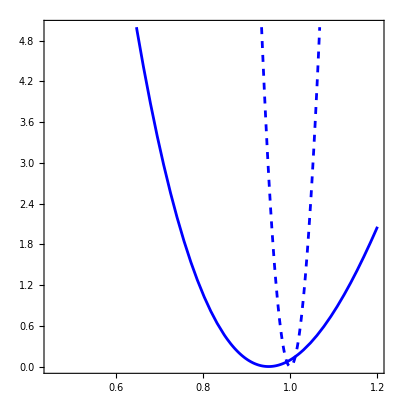

```mathematica
(**)
pl = Plot[{χ2gVLLerror[gVLL]-mingVLL[[1]],chi2gVLLproj,,,},{gVLL,0.45,1.2},
PlotRange->{{0.45,1.2},{0,5}},
PlotLegends->Placed[Framed[LineLegend[{Blue,{Blue,Dashed},Red,Green,Black},{"COHERENT" ,"Projection" ,"CHARM-II","KARMEN" ,"SM" }],Background->White],{Left,Top}],
PlotStyle->{{Blue},{Blue,Dashed},{Red},{Green},{Black}},
LabelStyle->18,
(*Axes->False,*)
AxesStyle->Directive[Black,18],
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,18],
RotateLabel->False,
AspectRatio->5/(0.7*7)];
```

```mathematica
currReg=RegionPlot[chi2gVLL<=gSLLsq,{gVLL,0,1.2},{gSLLsq,0,5},
BoundaryStyle->None,
PlotStyle->{LightBlue,Opacity[0.95]},
PlotRange->{{0.45,1.2},{0,5}},
Axes->False,
Frame->{{True,False},{True,False}}];
projReg=RegionPlot[chi2gVLLproj<=gSLLsq,{gVLL,0,1.2},{gSLLsq,0,5},
BoundaryStyle->None,
PlotStyle->{Blue,Opacity[0.4]},
PlotRange->{{0.45,1.2},{0,5}},
Axes->False,
Frame->{{True,False},{True,False}},PlotPoints->500];
```

```mathematica
exReg=RegionPlot[gVLL>=1,{gVLL,0,1.2},{gSLLsq,0,5},
BoundaryStyle->None,
PlotStyle->{Gray,Opacity[0.6]},
PlotRange->{{0.45,1.2},{0,5}},
Axes->False,
Frame->{{True,False},{True,False}},PlotPoints->500];
```

```mathematica
img = Show[lab,(*currReg,projReg,*)pl,exReg,grapKar,grapPDG,grap90CL,grapSM]
```

-Graphics-

```mathematica
χ2gVLLerror[.8036215]-mingVLL[[1]]
```

1.0097

```mathematica
0.9494616346273992-.8036215
```

0.14584

## decay ()

#### Current

```mathematica
chi2xmu=(χ2totalCsInew/.{x1-> xmu,x2-> 1,x3-> 1})+(χ2totalAr/.{x1-> xmu,x2-> 1,x3-> 1});
minxmu  = FindMinimum[chi2xmu,{{xmu,1},{aAr,0},{bAr,0},{cAr,0},{dAr,0},{nuis1Ar,0},{nuis2Ar,0},{nuis3Ar,0},{nuis4Ar,0},{nuis5Ar,0},{aCsI2,0},{bCsI2,0},{cCsI2,0},{dCsI2,0}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{809.161,{xmu→1.41335,aAr→-0.0112397,bAr→0.131817,cAr→-0.848885,dAr→-0.00170438,nuis1Ar→0.0135357,nuis2Ar→-0.932527,nuis3Ar→1.35028,nuis4Ar→0.100903,nuis5Ar→0.049677,aCsI2→-0.0110317,bCsI2→-0.0902069,cCsI2→-0.0197213,dCsI2→-0.0214998}}

```mathematica
varpi = {xmu,aAr,bAr,cAr,dAr,nuis1Ar,nuis2Ar,nuis3Ar,nuis4Ar,nuis5Ar,aCsI2,bCsI2,cCsI2,dCsI2}
varpimin = varpi/.minxmu[[2]]
```

{xmu,aAr,bAr,cAr,dAr,nuis1Ar,nuis2Ar,nuis3Ar,nuis4Ar,nuis5Ar,aCsI2,bCsI2,cCsI2,dCsI2}

{1.41335,-0.0112397,0.131817,-0.848885,-0.00170438,0.0135357,-0.932527,1.35028,0.100903,0.049677,-0.0110317,-0.0902069,-0.0197213,-0.0214998}

```mathematica
chi2xmuGauss = MakeGauss[chi2xmu,varpi];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
tmpGpi=χsqToC0ΔCρ[chi2xmuGauss,varpi];
Off[NumberForm::reqsigz]
cErrpi=tmpGpi[[3]];
ρCorrpi=tmpGpi[[4]];
```

```mathematica
displayNowpi=(Log[10,Abs[varpimin/cErrpi]]//Ceiling)+2;
Print[varpi[[1]]," = ",NumberForm[varpimin[[1]],displayNowpi[[1]]]," +/- ",NumberForm[cErrpi[[1]],2]]
Print["χ^2(min) = ", Round[minxmu[[1]],0.1]]
χsqQsqArgonCOHERENTgaussian3Dpi=MakeChi2[varpi[[;;1]],varpimin[[;;1]],cErrpi[[;;1]],ρCorrpi[[;;1,;;1]]]
```

xmu = 1.41 +/- 0.32

χ^2(min) = 809.2

19.593-27.7258 xmu+9.80856 xmu^2

#### Projected

```mathematica
chi2xmup=(chi2Arproj/.{x1-> xmu,x2-> 1,x3-> 1,aAr->0,bAr->0,cAr->0,dAr->0,nuis1Ar->0,nuis2Ar->0,nuis3Ar->0,nuis4Ar->0,nuis5Ar->0,aCsI2->0,bCsI2->0,cCsI2->0,dCsI2->0});
minxmup = FindMinimum[chi2xmup,{xmu,1}]
```

{9.49329×10^-13,{xmu→1.}}

```mathematica
xmumin = xmu/.minxmup[[2]]
```

1.

```mathematica
chi2xmuGauss = MakeGauss[chi2xmup,{xmu}];
```

```mathematica
tmpGpip=χsqToC0ΔCρ[chi2xmuGauss,{xmu}];
Off[NumberForm::reqsigz]
cErrpip=tmpGpip[[3]];
ρCorrpip=tmpGpip[[4]];
```

```mathematica
displayNowpip=(Log[10,Abs[xmumin/cErrpip]]//Ceiling)+2;
Print["xmu"," = ",NumberForm[xmumin,displayNowpip[[1]]]," +/- ",NumberForm[cErrpip[[1]],2]]
Print["χ^2(min) = ", Round[minxmu[[1]],0.1]]
χsqQsqArgonCOHERENTgaussian3Dpip=MakeChi2[xmu,xmumin,cErrpip[[;;1]],ρCorrpip[[;;1,;;1]]]
```

xmu = 1. +/- 0.051

χ^2(min) = 809.2

Inverse::matsq: Argument {} at position 1 is not a non-empty square matrix.

(-1.+xmu).Inverse[{}].(-1.+xmu)

```mathematica
mpi=13957039/100000;
mmu=1056583745/10000000;
mu=216/100;
md=467/100;
```

#### Current

```mathematica
chi2eps=(χ2totalCsInew/.{x1-> 1-eps^2*mpi^4/(mmu^2* (mu+md)^2),x2-> 1,x3-> 1})+(χ2totalAr/.{x1-> 1-eps^2*mpi^4/(mmu^2* (mu+md)^2),x2-> 1,x3-> 1});
mineps = FindMinimum[chi2eps,{{eps,0},{aAr,0},{bAr,0},{cAr,0},{dAr,0},{nuis1Ar,0},{nuis2Ar,0},{nuis3Ar,0},{nuis4Ar,0},{nuis5Ar,0},{aCsI2,0},{bCsI2,0},{cCsI2,0},{dCsI2,0}}]
```

{811.09,{eps→0.,aAr→0.00465189,bAr→0.15515,cAr→-0.855465,dAr→-0.00157368,nuis1Ar→0.00292872,nuis2Ar→-0.981402,nuis3Ar→1.34039,nuis4Ar→0.0489549,nuis5Ar→0.027781,aCsI2→0.0390095,bCsI2→-0.0656318,cCsI2→-0.021774,dCsI2→-0.021983}}

```mathematica
vareps = {eps,aAr,bAr,cAr,dAr,nuis1Ar,nuis2Ar,nuis3Ar,nuis4Ar,nuis5Ar,aCsI2,bCsI2,cCsI2,dCsI2}
varepsmin = vareps/.mineps[[2]]
```

{eps,aAr,bAr,cAr,dAr,nuis1Ar,nuis2Ar,nuis3Ar,nuis4Ar,nuis5Ar,aCsI2,bCsI2,cCsI2,dCsI2}

{0.,0.00465189,0.15515,-0.855465,-0.00157368,0.00292872,-0.981402,1.34039,0.0489549,0.027781,0.0390095,-0.0656318,-0.021774,-0.021983}

```mathematica
chi2epsGauss = chi2xmuGauss/.xmu-> 1-eps^2*mpi^4/(mmu^2* (mu+md)^2)(*MakeGauss[chi2eps,vareps]*)//Expand//Simplify
MakeGauss[chi2eps,vareps]//Expand//Simplify
chi2xmuGauss
```

822.701+70.3098 aAr^2+192.732 aCsI2^2+13.4952 bAr+113.734 bAr^2+3.08485 bCsI2+17.131 bCsI2^2+9.53474×10^-7 cAr+2.91746 cAr^2+0.215721 cCsI2+0.168789 bCsI2 cCsI2+8.18839 cCsI2^2+33.3188 dAr+310.071 bAr dAr+35.8339 cAr dAr+17466.4 dAr^2+38.6134 dCsI2+20.6997 bCsI2 dCsI2+8.21622 cCsI2 dCsI2+3314.79 dCsI2^2-19731.7 eps^2-9833.42 bAr eps^2-2247.8 bCsI2 eps^2-3.08601×10^-6 cAr eps^2-157.187 cCsI2 eps^2-24278. dAr eps^2-28136. dCsI2 eps^2+7.18885×10^6 eps^4+aCsI2 (48.7563+11.5629 bCsI2+2.66502 cCsI2+416.797 dCsI2-35526.7 eps^2)-0.0916069 nuis1Ar-0.624377 bAr nuis1Ar-0.81877 dAr nuis1Ar+66.7505 eps^2 nuis1Ar+1.00195 nuis1Ar^2-0.312228 nuis2Ar+0.267545 bAr nuis2Ar+6.68936 dAr nuis2Ar+227.507 eps^2 nuis2Ar+0.0203845 nuis1Ar nuis2Ar+1.60861 nuis2Ar^2+1.09255 nuis3Ar+18.304 bAr nuis3Ar+4.25133 dAr nuis3Ar-796.093 eps^2 nuis3Ar-0.0855692 nuis1Ar nuis3Ar-1.36755 nuis2Ar nuis3Ar+3.1647 nuis3Ar^2-0.294102 nuis4Ar+0.0416473 bAr nuis4Ar+0.0192409 cAr nuis4Ar-0.209888 dAr nuis4Ar+214.299 eps^2 nuis4Ar+0.00150123 nuis1Ar nuis4Ar+0.0165086 nuis2Ar nuis4Ar+0.0243075 nuis3Ar nuis4Ar+1.00946 nuis4Ar^2+aAr (8.57884+39.3391 bAr+2.18813 cAr+193.969 dAr-6251.04 eps^2-0.193652 nuis1Ar+0.279822 nuis2Ar+2.30508 nuis3Ar-0.166812 nuis4Ar-0.068335 nuis5Ar)-0.11739 nuis5Ar+0.088058 bAr nuis5Ar+0.0021968 cAr nuis5Ar+0.150757 dAr nuis5Ar+85.537 eps^2 nuis5Ar+0.000948944 nuis1Ar nuis5Ar-0.00491589 nuis2Ar nuis5Ar+0.0233802 nuis3Ar nuis5Ar+0.0067332 nuis4Ar nuis5Ar+1.00172 nuis5Ar^2

811.09+67.6915 aAr^2+178.393 aCsI2^2-1.68484×10^-10 bAr+113.408 bAr^2-5.15749×10^-11 bCsI2+17.16 bCsI2^2+2.72659×10^-9 cAr+2.91664 cAr^2+1.15208×10^-10 cCsI2+0.172748 bCsI2 cCsI2+8.18809 cCsI2^2-1.00954×10^-10 dAr+311.097 bAr dAr+35.8102 cAr dAr+17468.8 dAr^2-1.62714×10^-12 dCsI2+21.2526 bCsI2 dCsI2+8.13378 cCsI2 dCsI2+3309.79 dCsI2^2+aCsI2 (5.02737×10^-12+11.1429 bCsI2+2.57895 cCsI2+404.119 dCsI2)+7294.93 eps^2+3.63843×10^-9 nuis1Ar-0.633764 bAr nuis1Ar-0.842251 dAr nuis1Ar+1.00201 nuis1Ar^2-3.67972×10^-11 nuis2Ar+0.240986 bAr nuis2Ar+6.51673 dAr nuis2Ar+0.0203982 nuis1Ar nuis2Ar+1.60216 nuis2Ar^2+1.75263×10^-9 nuis3Ar+18.1798 bAr nuis3Ar+4.36394 dAr nuis3Ar-0.0858997 nuis1Ar nuis3Ar-1.35181 nuis2Ar nuis3Ar+3.14177 nuis3Ar^2-2.31715×10^-9 nuis4Ar+0.0822286 bAr nuis4Ar+0.019211 cAr nuis4Ar+0.185421 dAr nuis4Ar+0.00115997 nuis1Ar nuis4Ar+0.015035 nuis2Ar nuis4Ar+0.0203626 nuis3Ar nuis4Ar+1.00594 nuis4Ar^2+aAr (-3.52429×10^-11+34.358 bAr+2.1857 cAr+181.58 dAr-0.162215 nuis1Ar+0.386285 nuis2Ar+1.90789 nuis3Ar-0.0494297 nuis4Ar-0.0236842 nuis5Ar)+7.85835×10^-10 nuis5Ar+0.0929836 bAr nuis5Ar+0.00218836 cAr nuis5Ar+0.246092 dAr nuis5Ar+0.000725925 nuis1Ar nuis5Ar-0.0046435 nuis2Ar nuis5Ar+0.0216962 nuis3Ar nuis5Ar+0.00453585 nuis4Ar nuis5Ar+1.00126 nuis5Ar^2

```mathematica
tmpGeps=χsqToC0ΔCρ[chi2epsGauss,vareps];
Off[NumberForm::reqsigz]
cErreps=tmpGeps[[3]];
ρCorreps=tmpGeps[[4]];
```

```mathematica
displayNoweps=(Log[10,Abs[varepsmin/cErreps]]//Ceiling)+2;
Print[vareps[[1]]," = ",NumberForm[varepsmin[[1]],displayNoweps[[1]]]," +/- ",NumberForm[cErreps[[1]],2]]
Print["χ^2(min) = ", Round[minxmu[[1]],0.1]]
χsqQsqArgonCOHERENTgaussian3Deps=MakeChi2[vareps[[;;1]],varepsmin[[;;1]],cErreps[[;;1]],ρCorreps[[;;1,;;1]]]
```

NumberForm::iprf: Formatting specification Indeterminate should be a positive integer or a pair of positive integers.

eps = 0. +/- (1.0×10^1078) √(1/(-2.1×10^2160-(6.6×10^2159) aAr-(3.8×10^2160) aCsI2-(1.0×10^2160) bAr-(2.4×10^2159) bCsI2-(3.3×10^2150) cAr-(1.7×10^2158) cCsI2-(2.6×10^2160) dAr-(3.0×10^2160) dCsI2+(3.7×10^2163) eps^2+(7.0×10^2157) nuis1Ar+(2.4×10^2158) nuis2Ar-(8.4×10^2158) nuis3Ar+(2.3×10^2158) nuis4Ar+(9.0×10^2157) nuis5Ar))

χ^2(min) = 809.2

0.-19731.7332 eps^2-6251.04229 aAr eps^2-35526.6641 aCsI2 eps^2-9833.4208 bAr eps^2-2247.80027 bCsI2 eps^2-3.08600778×10^-6 cAr eps^2-157.18729 cCsI2 eps^2-24278.0457 dAr eps^2-28136.003 dCsI2 eps^2+3.52088252×10^7 eps^4+66.7504986 eps^2 nuis1Ar+227.507339 eps^2 nuis2Ar-796.092609 eps^2 nuis3Ar+214.29916 eps^2 nuis4Ar+85.5370167 eps^2 nuis5Ar

#### Projections

```mathematica
chi2epsp=(chi2Arproj/.{x1-> 1-eps^2*mpi^4/(mmu^2* (mu+md)^2),x2-> 1,x3-> 1,aAr->0,bAr->0,cAr->0,dAr->0,nuis1Ar->0,nuis2Ar->0,nuis3Ar->0,nuis4Ar->0,nuis5Ar->0,aCsI2->0,bCsI2->0,cCsI2->0,dCsI2->0});
minepsp = FindMinimum[chi2epsp,{eps,0}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{9.49329×10^-13,{eps→0.}}

```mathematica
D[D[chi2epsp,eps],eps]/2/.eps->0
```

0.

```mathematica
epsmin = eps/.minepsp[[2]]
```

0.

```mathematica
Normal[Series[chi2epsp/.eps->epsmin+ϵ* x,{ϵ,0,8}]]
```

1.13687×10^-12+2.02897×10^8 x^4 ϵ^4+5.33203×10^10 x^6 ϵ^6+1.61752×10^13 x^8 ϵ^8

```mathematica
chi2epspGauss = MakeGauss[chi2epsp,{eps}];
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

```mathematica
chi2epspGauss
```

9.09495×10^-13-2.32831×10^-10 eps^2

```mathematica
tmpGepsp=χsqToC0ΔCρ[chi2epspGauss,{eps}];
Off[NumberForm::reqsigz]
cErrepsp=tmpGepsp[[3]];
ρCorrepsp=tmpGepsp[[4]];
```

```mathematica
displayNowepsp=(Log[10,Abs[epsmin/cErrepsp]]//Ceiling)+2;
Print["eps"," = ",NumberForm[epsmin,displayNowepsp[[1]]]," +/- ",NumberForm[cErrepsp[[1]],2]]
Print["χ^2(min) = ", Round[minepsp[[1]],0.1]]
χsqQsqArgonCOHERENTgaussian3Depsp=MakeChi2[eps,epsmin,cErrepsp[[;;1]],ρCorrepsp[[;;1,;;1]]]
```

NumberForm::iprf: Formatting specification Indeterminate should be a positive integer or a pair of positive integers.

eps = 0. +/- 0.+66000. ⅈ

χ^2(min) = 0.

Inverse::matsq: Argument {} at position 1 is not a non-empty square matrix.

(0.+eps).Inverse[{}].(0.+eps)